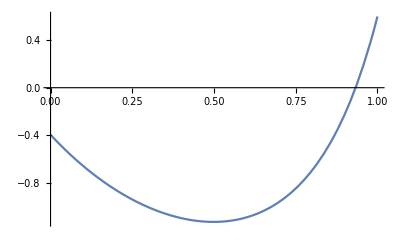

```mathematica
R1[x_] :=
Cosh[(3 * x^3 + 2 * x^2-4 * x +5)/3];
R2[x_] := Tanh[(x^3- 3 * Sqrt[2]*x^2-2)/(2*x + Sqrt[2])];
foo [x_] := R1[x] + R2[x] -2.25;
Plot[foo[x],{x,0,1}]
```

```mathematica
dih[a_, b_,eps_] := Module[{x1, x2, temp1,temp2, res, k,n, list},
x1 = a;
list = {};
x2 = b;
k = 0;
n = 0;
While[Abs[x1-x2] > eps,
++k;
res = (x1 + x2)/2;
Append[list,{res, foo[res]}];
temp1 = res - eps /2;
temp2  = res + eps /2;

If[foo[temp1] > foo[temp2],
x1 =  temp2;
,
x2 = temp1;
];
n += 2;
];
{res,foo[res],k, n, list}
]
```

```mathematica
tau = 1/2(1+Sqrt[5])//N;
test = {};
mzs[a_,b_,eps_]:= Module[{xk1,xk2, ak,bk, fk1, fk2,res, k, n, lk},
k = 1;
test = {};
ak = a;
bk = b;
xk1 = ak + (1 - 1/tau)bk//N;
xk2 = ak + 1/tau bk//N;
fk1 = foo[xk1];
fk2 = foo[xk2];
n = 2;
AppendTo[test, {ak, bk}];
lk = ak -bk//N;
While[Abs[ak -bk]>= eps,
++k;
If[fk1 < fk2,
bk = xk2;
xk2 = xk1;
xk1 = ak + bk - xk2;
fk2 = fk1;
fk1 = foo[xk1];
++n;
,
ak = xk1;
xk1 = xk2;
xk2 = ak + bk - xk1;
fk1 = fk2;
fk2 =  foo[xk2];
++n;
];
AppendTo[test, {ak, bk}];
];

res = (ak + bk)/2;
{res,foo[res],k, n}
]
```

{0.484219,-1.13094,6.,12.,{}}

{0.497488,-1.13164,11.,12.}

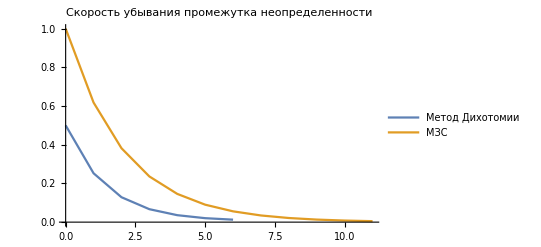

```mathematica
eps = 0.01;
result1 = dih[0,1,eps] //N
result2 = mzs[0, 1, eps]//N
k1 = result1[[3]];
k2 = result2[[3]];

l1 = {};
l2 = {};
For[i = 0, i <= k1, ++i,
AppendTo[l1,{i, (1 - 2*eps/2)/2^(i+1)+eps/2}]
]
For[i = 0, i <= k2, ++i,
AppendTo[l2, {i,1/tau^i}]
]
ListPlot[{l1,l2} ,Joined->True, PlotLegends->{"Метод Дихотомии", "МЗС"}, PlotLabel-> "Скорость убывания промежутка неопределенности"]

(* 
Формат результата:
{точка минимума, значении ф-ии в точке кол-во итераций, кол-во вычислений}
*)
```

{0.498602,-1.13164,19.,38.,{}}

{0.498601,-1.13164,30.,31.}

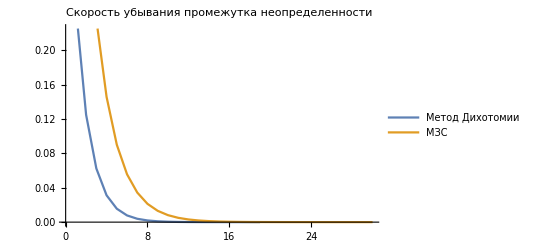

```mathematica
eps = 0.000001;
result1 = dih[0,1,eps] //N
result2 = mzs[0, 1, eps]//N
k1 = result1[[3]];
k2 = result2[[3]];

l1 = {};
l2 = {};
For[i = 0, i <= k1, ++i,
AppendTo[l1,{i, (1 - 2*eps/2)/2^(i+1)+eps/2}]
];
For[i = 0, i <= k2, ++i,
AppendTo[l2, {i,1/tau^i}]
];
ListPlot[{l1,l2} ,Joined->True, PlotLegends->{"Метод Дихотомии", "МЗС"},PlotLabel-> "Скорость убывания промежутка неопределенности"]
(* 
Формат результата:
{точка минимума, значении ф-ии в точке кол-во итераций, кол-во вычислений}
*)
```

{0.498577,-1.13164,33.,66.,{}}

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::munfl: 1/(6.99789×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(1.13228×10^308) is too small to represent as a normalized machine number; precision may be lost.

$Aborted

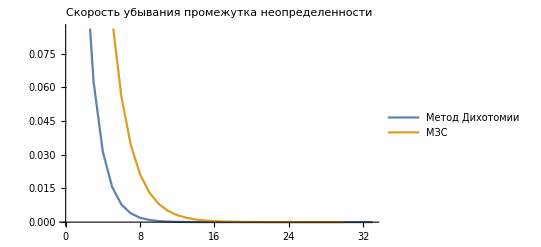

```mathematica
eps = 10^-10;
result1 = dih[0,1,eps] //N
result2 = mzs[0, 1, eps]//N
k1 = result1[[3]];
k2 = result2[[3]];

l1 = {};
l2 = {};
For[i = 0, i <= k1, ++i,
AppendTo[l1,{i, (1 - 2*eps/2)/2^(i+1)+eps/2}]
];
For[i = 0, i <= k2, ++i,
AppendTo[l2, {i,1/tau^i}]
];
ListPlot[{l1,l2} ,Joined->True, PlotLegends->{"Метод Дихотомии", "МЗС"},PlotLabel-> "Скорость убывания промежутка неопределенности"]
(* 
Формат результата:
{точка минимума, значении ф-ии в точке кол-во итераций, кол-во вычислений}
*)
```

{8.87779×10^-18,-0.396703,56.,112.,{}}

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::munfl: 1/(6.99789×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(1.13228×10^308) is too small to represent as a normalized machine number; precision may be lost.

$Aborted

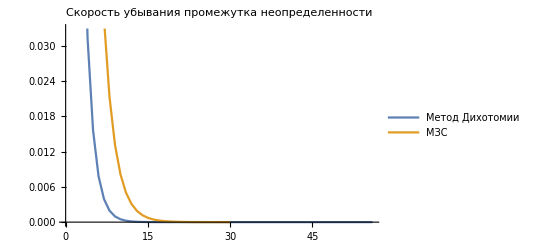

{30.,5.3749×10^-7}

```mathematica
eps = 10^-17//N;

result1 = dih[0,1,eps] //N
result2 = mzs[0, 1, eps]//N
k1 = result1[[3]];
k2 = result2[[3]];

l1 = {};
l2 = {};
For[i = 0, i <= k1, ++i,
AppendTo[l1,{i, (1 - 2*eps/2)/2^(i+1)+eps/2}]
];
For[i = 0, i <= k2, ++i,
AppendTo[l2, {i,1/tau^i}]
];
ListPlot[{l1,l2} ,Joined->True, PlotLegends->{"Метод Дихотомии", "МЗС"},PlotLabel-> "Скорость убывания промежутка неопределенности"]
l2[[Length@l2]]//N

(* 
Формат результата:
{точка минимума, значении ф-ии в точке кол-во итераций, кол-во вычислений}
*)

(*
методы не валидны при такой точности, т.к. в данном случае eps меньше машинного нуля => ответ будет не верным или вылетит ошибка
*)
```

```mathematica
(* comparison with WM function*)
FindMinimum[foo[x], {x,0,1}]
```

{-1.13164,{x→0.498601}}

```mathematica
(*
Для большей точности более выгоден метод золотого сечения т.к. производиться
меньше вычислений за одну итерацию.

Так же по графикам зависимости (отрезка неопределенности от итерации) видно, что отрезок неопределеннсти быстрее уменьшается в случае метода дихотомии.
*)
```

```mathematica
$MachineEpsilon
```

2.22045×10^-16

```mathematica
test//MatrixForm
```

(1)
 |  |  |  |

```mathematica
N[test,2*MachinePrecision]//MatrixForm
```

$Aborted[]

```mathematica
r = {}
For[i = 1, i <= Length[test], ++i,
AppendTo[r, Abs[test[[i]][[1]] - test[[i]][[2]]]]]
```

{}

```mathematica
N[r, 2*MachinePrecision]//MatrixForm
```

(1.
0.618034
0.381966
0.236068
0.145898
0.0901699
0.0557281
0.0344419
0.0212862
0.0131556
0.00813062
0.005025
0.00310562
0.00191938
0.00118624
0.000733137
0.000453104
0.000280034
0.00017307
0.000106963
0.000066107
0.0000408563
0.0000252506
0.0000156057
9.64488×10^-6
5.96086×10^-6
3.68402×10^-6
2.27684×10^-6
1.40719×10^-6
8.69649×10^-7
5.37538×10^-7
3.32111×10^-7
2.05427×10^-7
1.26684×10^-7
7.87422×10^-8
4.79423×10^-8
3.07999×10^-8
1.71424×10^-8
1.36575×10^-8
3.4849×10^-9
1.01726×10^-8
6.6877×10^-9
1.68603×10^-8
2.3548×10^-8
4.04083×10^-8
6.39563×10^-8
1.04365×10^-7
1.68321×10^-7
2.72685×10^-7
4.41006×10^-7
7.13691×10^-7
1.1547×10^-6
1.86839×10^-6
3.02309×10^-6
4.89148×10^-6
7.91456×10^-6
0.000012806
0.0000207206
0.0000335266
0.0000542472
0.0000877739
0.000142021
0.000229795
0.000371816
0.000601611
0.000973427
0.00157504
0.00254847
0.0041235
0.00667197
0.0107955
0.0174674
0.0282629
0.0457304
0.0739933
0.119724
0.193717
0.313441
0.507157
0.820598
1.32776
2.14835
3.47611
5.62446
9.10057
14.725
23.8256
38.5506
62.3762
100.927
163.303
264.23
427.533
691.763
1119.3
1811.06
2930.36
4741.42
7671.77
12413.2
20085.
32498.1
52583.1
85081.2
137664.
222746.
360410.
583155.
943565.
1.52672×10^6
2.47029×10^6
3.99701×10^6
6.46729×10^6
1.04643×10^7
1.69316×10^7
2.73959×10^7
4.43275×10^7
7.17234×10^7
1.16051×10^8
1.87774×10^8
3.03825×10^8
4.91599×10^8
7.95425×10^8
1.28702×10^9
2.08245×10^9
3.36947×10^9
5.45192×10^9
8.82139×10^9
1.42733×10^10
2.30947×10^10
3.7368×10^10
6.04627×10^10
9.78307×10^10
1.58293×10^11
2.56124×10^11
4.14418×10^11
6.70542×10^11
1.08496×10^12
1.7555×10^12
2.84046×10^12
4.59596×10^12
7.43642×10^12
1.20324×10^13
1.94688×10^13
3.15012×10^13
5.097×10^13
8.24712×10^13
1.33441×10^14
2.15912×10^14
3.49354×10^14
5.65266×10^14
9.1462×10^14
1.47989×10^15
2.39451×10^15
3.87439×10^15
6.2689×10^15
1.01433×10^16
1.64122×10^16
2.65555×10^16
4.29677×10^16
6.95231×10^16
1.12491×10^17
1.82014×10^17
2.94505×10^17
4.76519×10^17
7.71023×10^17
1.24754×10^18
2.01857×10^18
3.26611×10^18
5.28467×10^18
8.55078×10^18
1.38355×10^19
2.23862×10^19
3.62217×10^19
5.86079×10^19
9.48296×10^19
1.53438×10^20
2.48267×10^20
4.01705×10^20
6.49972×10^20
1.05168×10^21
1.70165×10^21
2.75332×10^21
4.45497×10^21
7.2083×10^21
1.16633×10^22
1.88716×10^22
3.05348×10^22
4.94064×10^22
7.99412×10^22
1.29348×10^23
2.09289×10^23
3.38637×10^23
5.47925×10^23
8.86562×10^23
1.43449×10^24
2.32105×10^24
3.75554×10^24
6.07659×10^24
9.83212×10^24
1.59087×10^25
2.57408×10^25
4.16495×10^25
6.73904×10^25
1.0904×10^26
1.7643×10^26
2.8547×10^26
4.619×10^26
7.47371×10^26
1.20927×10^27
1.95664×10^27
3.16591×10^27
5.12255×10^27
8.28847×10^27
1.3411×10^28
2.16995×10^28
3.51105×10^28
5.681×10^28
9.19205×10^28
1.48731×10^29
2.40651×10^29
3.89382×10^29
6.30033×10^29
1.01941×10^30
1.64945×10^30
2.66886×10^30
4.31831×10^30
6.98717×10^30
1.13055×10^31
1.82926×10^31
2.95981×10^31
4.78908×10^31
7.74889×10^31
1.2538×10^32
2.02869×10^32
3.28248×10^32
5.31117×10^32
8.59365×10^32
1.39048×10^33
2.24985×10^33
3.64033×10^33
5.89017×10^33
9.5305×10^33
1.54207×10^34
2.49512×10^34
4.03719×10^34
6.5323×10^34
1.05695×10^35
1.71018×10^35
2.76713×10^35
4.47731×10^35
7.24444×10^35
1.17217×10^36
1.89662×10^36
3.06879×10^36
4.96541×10^36
8.0342×10^36
1.29996×10^37
2.10338×10^37
3.40334×10^37
5.50672×10^37
8.91007×10^37
1.44168×10^38
2.33269×10^38
3.77436×10^38
6.10705×10^38
9.88142×10^38
1.59885×10^39
2.58699×10^39
4.18583×10^39
6.77282×10^39
1.09587×10^40
1.77315×10^40
2.86901×10^40
4.64216×10^40
7.51118×10^40
1.21533×10^41
1.96645×10^41
3.18179×10^41
5.14824×10^41
8.33002×10^41
1.34783×10^42
2.18083×10^42
3.52865×10^42
5.70948×10^42
9.23814×10^42
1.49476×10^43
2.41858×10^43
3.91334×10^43
6.33191×10^43
1.02452×10^44
1.65772×10^44
2.68224×10^44
4.33996×10^44
7.0222×10^44
1.13622×10^45
1.83844×10^45
2.97465×10^45
4.81309×10^45
7.78774×10^45
1.26008×10^46
2.03886×10^46
3.29894×10^46
5.33779×10^46
8.63673×10^46
1.39745×10^47
2.26113×10^47
3.65858×10^47
5.91971×10^47
9.57828×10^47
1.5498×10^48
2.50763×10^48
4.05743×10^48
6.56505×10^48
1.06225×10^49
1.71875×10^49
2.781×10^49
4.49975×10^49
7.28076×10^49
1.17805×10^50
1.90613×10^50
3.08418×10^50
4.9903×10^50
8.07448×10^50
1.30648×10^51
2.11393×10^51
3.42041×10^51
5.53433×10^51
8.95474×10^51
1.44891×10^52
2.34438×10^52
3.79329×10^52
6.13767×10^52
9.93096×10^52
1.60686×10^53
2.59996×10^53
4.20682×10^53
6.80678×10^53
1.10136×10^54
1.78204×10^54
2.8834×10^54
4.66544×10^54
7.54883×10^54
1.22143×10^55
1.97631×10^55
3.19774×10^55
5.17405×10^55
8.37178×10^55
1.35458×10^56
2.19176×10^56
3.54634×10^56
5.73811×10^56
9.28445×10^56
1.50226×10^57
2.4307×10^57
3.93296×10^57
6.36366×10^57
1.02966×10^58
1.66603×10^58
2.69569×10^58
4.36172×10^58
7.0574×10^58
1.14191×10^59
1.84765×10^59
2.98956×10^59
4.83722×10^59
7.82678×10^59
1.2664×10^60
2.04908×10^60
3.31548×10^60
5.36456×10^60
8.68003×10^60
1.40446×10^61
2.27246×10^61
3.67692×10^61
5.94938×10^61
9.6263×10^61
1.55757×10^62
2.5202×10^62
4.07777×10^62
6.59797×10^62
1.06757×10^63
1.72737×10^63
2.79494×10^63
4.52231×10^63
7.31726×10^63
1.18396×10^64
1.91568×10^64
3.09964×10^64
5.01532×10^64
8.11496×10^64
1.31303×10^65
2.12453×10^65
3.43755×10^65
5.56208×10^65
8.99963×10^65
1.45617×10^66
2.35613×10^66
3.81231×10^66
6.16844×10^66
9.98075×10^66
1.61492×10^67
2.61299×10^67
4.22791×10^67
6.8409×10^67
1.10688×10^68
1.79097×10^68
2.89785×10^68
4.68883×10^68
7.58668×10^68
1.22755×10^69
1.98622×10^69
3.21377×10^69
5.19999×10^69
8.41376×10^69
1.36137×10^70
2.20275×10^70
3.56412×10^70
5.76687×10^70
9.331×10^70
1.50979×10^71
2.44289×10^71
3.95267×10^71
6.39556×10^71
1.03482×10^72
1.67438×10^72
2.7092×10^72
4.38358×10^72
7.09279×10^72
1.14764×10^73
1.85692×10^73
3.00455×10^73
4.86147×10^73
7.86602×10^73
1.27275×10^74
2.05935×10^74
3.3321×10^74
5.39145×10^74
8.72355×10^74
1.4115×10^75
2.28386×10^75
3.69536×10^75
5.97921×10^75
9.67457×10^75
1.56538×10^76
2.53283×10^76
4.09821×10^76
6.63105×10^76
1.07293×10^77
1.73603×10^77
2.80896×10^77
4.54499×10^77
7.35394×10^77
1.18989×10^78
1.92529×10^78
3.11518×10^78
5.04047×10^78
8.15565×10^78
1.31961×10^79
2.13518×10^79
3.45479×10^79
5.58996×10^79
9.04475×10^79
1.46347×10^80
2.36795×10^80
3.83142×10^80
6.19937×10^80
1.00308×10^81
1.62301×10^81
2.62609×10^81
4.24911×10^81
6.8752×10^81
1.11243×10^82
1.79995×10^82
2.91238×10^82
4.71233×10^82
7.62472×10^82
1.2337×10^83
1.99618×10^83
3.22988×10^83
5.22606×10^83
8.45594×10^83
1.3682×10^84
2.21379×10^84
3.58199×10^84
5.79579×10^84
9.37778×10^84
1.51736×10^85
2.45513×10^85
3.97249×10^85
6.42763×10^85
1.04001×10^86
1.68277×10^86
2.72279×10^86
4.40556×10^86
7.12835×10^86
1.15339×10^87
1.86623×10^87
3.01962×10^87
4.88584×10^87
7.90546×10^87
1.27913×10^88
2.06968×10^88
3.34881×10^88
5.41848×10^88
8.76729×10^88
1.41858×10^89
2.29531×10^89
3.71388×10^89
6.00919×10^89
9.72307×10^89
1.57323×10^90
2.54553×10^90
4.11876×10^90
6.66429×10^90
1.0783×10^91
1.74473×10^91
2.82304×10^91
4.56777×10^91
7.39081×10^91
1.19586×10^92
1.93494×10^92
3.1308×10^92
5.06574×10^92
8.19654×10^92
1.32623×10^93
2.14588×10^93
3.47211×10^93
5.61799×10^93
9.0901×10^93
1.47081×10^94
2.37982×10^94
3.85063×10^94
6.23045×10^94
1.00811×10^95
1.63115×10^95
2.63926×10^95
4.27041×10^95
6.90967×10^95
1.11801×10^96
1.80898×10^96
2.92698×10^96
4.73596×10^96
7.66294×10^96
1.23989×10^97
2.00618×10^97
3.24607×10^97
5.25226×10^97
8.49833×10^97
1.37506×10^98
2.22489×10^98
3.59995×10^98
5.82484×10^98
9.4248×10^98
1.52496×10^99
2.46744×10^99
3.99241×10^99
6.45985×10^99
1.04523×10^100
1.69121×10^100
2.73644×10^100
4.42765×10^100
7.16408×10^100
1.15917×10^101
1.87558×10^101
3.03475×10^101
4.91034×10^101
7.94509×10^101
1.28554×10^102
2.08005×10^102
3.36559×10^102
5.44565×10^102
8.81124×10^102
1.42569×10^103
2.30681×10^103
3.7325×10^103
6.03931×10^103
9.77182×10^103
1.58111×10^104
2.55829×10^104
4.13941×10^104
6.6977×10^104
1.08371×10^105
1.75348×10^105
2.83719×10^105
4.59067×10^105
7.42787×10^105
1.20185×10^106
1.94464×10^106
3.14649×10^106
5.09114×10^106
8.23763×10^106
1.33288×10^107
2.15664×10^107
3.48952×10^107
5.64616×10^107
9.13567×10^107
1.47818×10^108
2.39175×10^108
3.86993×10^108
6.26168×10^108
1.01316×10^109
1.63933×10^109
2.65249×10^109
4.29182×10^109
6.94431×10^109
1.12361×10^110
1.81804×10^110
2.94166×10^110
4.7597×10^110
7.70136×10^110
1.24611×10^111
2.01624×10^111
3.26235×10^111
5.27859×10^111
8.54094×10^111
1.38195×10^112
2.23605×10^112
3.618×10^112
5.85405×10^112
9.47205×10^112
1.53261×10^113
2.47981×10^113
4.01242×10^113
6.49224×10^113
1.05047×10^114
1.69969×10^114
2.75016×10^114
4.44985×10^114
7.2×10^114
1.16498×10^115
1.88498×10^115
3.04997×10^115
4.93495×10^115
7.98492×10^115
1.29199×10^116
2.09048×10^116
3.38247×10^116
5.47295×10^116
8.85542×10^116
1.43284×10^117
2.31838×10^117
3.75121×10^117
6.06959×10^117
9.82081×10^117
1.58904×10^118
2.57112×10^118
4.16016×10^118
6.73128×10^118
1.08914×10^119
1.76227×10^119
2.85142×10^119
4.61369×10^119
7.46511×10^119
1.20788×10^120
1.95439×10^120
3.16227×10^120
5.11666×10^120
8.27893×10^120
1.33956×10^121
2.16745×10^121
3.50701×10^121
5.67446×10^121
9.18147×10^121
1.48559×10^122
2.40374×10^122
3.88933×10^122
6.29308×10^122
1.01824×10^123
1.64755×10^123
2.66579×10^123
4.31334×10^123
6.97913×10^123
1.12925×10^124
1.82716×10^124
2.95641×10^124
4.78356×10^124
7.73997×10^124
1.25235×10^125
2.02635×10^125
3.2787×10^125
5.30505×10^125
8.58376×10^125
1.38888×10^126
2.24726×10^126
3.63614×10^126
5.8834×10^126
9.51953×10^126
1.54029×10^127
2.49225×10^127
4.03254×10^127
6.52479×10^127
1.05573×10^128
1.70821×10^128
2.76394×10^128
4.47215×10^128
7.2361×10^128
1.17083×10^129
1.89444×10^129
3.06526×10^129
4.9597×10^129
8.02496×10^129
1.29847×10^130
2.10096×10^130
3.39943×10^130
5.50039×10^130
8.89981×10^130
1.44002×10^131
2.33×10^131
3.77002×10^131
6.10002×10^131
9.87004×10^131
1.59701×10^132
2.58401×10^132
4.18102×10^132
6.76503×10^132
1.0946×10^133
1.77111×10^133
2.86571×10^133
4.63682×10^133
7.50253×10^133
1.21394×10^134
1.96419×10^134
3.17812×10^134
5.14231×10^134
8.32044×10^134
1.34627×10^135
2.17832×10^135
3.52459×10^135
5.70291×10^135
9.2275×10^135
1.49304×10^136
2.41579×10^136
3.90883×10^136
6.32463×10^136
1.02335×10^137
1.65581×10^137
2.67915×10^137
4.33496×10^137
7.01412×10^137
1.13491×10^138
1.83632×10^138
2.97123×10^138
4.80755×10^138
7.77878×10^138
1.25863×10^139
2.03651×10^139
3.29514×10^139
5.33165×10^139
8.62679×10^139
1.39584×10^140
2.25852×10^140
3.65437×10^140
5.91289×10^140
9.56726×10^140
1.54802×10^141
2.50474×10^141
4.05276×10^141
6.5575×10^141
1.06103×10^142
1.71678×10^142
2.7778×10^142
4.49458×10^142
7.27238×10^142
1.1767×10^143
1.90393×10^143
3.08063×10^143
4.98456×10^143
8.06519×10^143
1.30498×10^144
2.11149×10^144
3.41647×10^144
5.52796×10^144
8.94443×10^144
1.44724×10^145
2.34168×10^145
3.78892×10^145
6.13061×10^145
9.91953×10^145
1.60501×10^146
2.59697×10^146
4.20198×10^146
6.79895×10^146
1.10009×10^147
1.77999×10^147
2.88008×10^147
4.66007×10^147
7.54015×10^147
1.22002×10^148
1.97404×10^148
3.19406×10^148
5.16809×10^148
8.36215×10^148
1.35302×10^149
2.18924×10^149
3.54226×10^149
5.7315×10^149
9.27377×10^149
1.50053×10^150
2.4279×10^150
3.92843×10^150
6.35633×10^150
1.02848×10^151
1.66411×10^151
2.69259×10^151
4.3567×10^151
7.04928×10^151
1.1406×10^152
1.84553×10^152
2.98612×10^152
4.83165×10^152
7.81777×10^152
1.26494×10^153
2.04672×10^153
3.31166×10^153
5.35838×10^153
8.67004×10^153
1.40284×10^154
2.26985×10^154
3.67269×10^154
5.94254×10^154
9.61523×10^154
1.55578×10^155
2.5173×10^155
4.07308×10^155
6.59037×10^155
1.06634×10^156
1.72538×10^156
2.79173×10^156
4.51711×10^156
7.30884×10^156
1.18259×10^157
1.91348×10^157
3.09607×10^157
5.00955×10^157
8.10562×10^157
1.31152×10^158
2.12208×10^158
3.4336×10^158
5.55568×10^158
8.98928×10^158
1.4545×10^159
2.35342×10^159
3.80792×10^159
6.16134×10^159
9.96926×10^159
1.61306×10^160
2.60999×10^160
4.22305×10^160
6.83303×10^160
1.10561×10^161
1.78891×10^161
2.89452×10^161
4.68343×10^161
7.57795×10^161
1.22614×10^162
1.98393×10^162
3.21007×10^162
5.194×10^162
8.40407×10^162
1.35981×10^163
2.20022×10^163
3.56002×10^163
5.76024×10^163
9.32026×10^163
1.50805×10^164
2.44008×10^164
3.94813×10^164
6.3882×10^164
1.03363×10^165
1.67245×10^165
2.70609×10^165
4.37854×10^165
7.08462×10^165
1.14632×10^166
1.85478×10^166
3.00109×10^166
4.85587×10^166
7.85697×10^166
1.27128×10^167
2.05698×10^167
3.32827×10^167
5.38525×10^167
8.71351×10^167
1.40988×10^168
2.28123×10^168
3.6911×10^168
5.97233×10^168
9.66343×10^168
1.56358×10^169
2.52992×10^169
4.0935×10^169
6.62342×10^169
1.07169×10^170
1.73403×10^170
2.80572×10^170
4.53976×10^170
7.34548×10^170
1.18852×10^171
1.92307×10^171
3.1116×10^171
5.03467×10^171
8.14626×10^171
1.31809×10^172
2.13272×10^172
3.45081×10^172
5.58353×10^172
9.03434×10^172
1.46179×10^173
2.36522×10^173
3.82701×10^173
6.19223×10^173
1.00192×10^174
1.62115×10^174
2.62307×10^174
4.24422×10^174
6.86729×10^174
1.11115×10^175
1.79788×10^175
2.90903×10^175
4.70691×10^175
7.61594×10^175
1.23229×10^176
1.99388×10^176
3.22616×10^176
5.22004×10^176
8.44621×10^176
1.36663×10^177
2.21125×10^177
3.57787×10^177
5.78912×10^177
9.36699×10^177
1.51561×10^178
2.45231×10^178
3.96792×10^178
6.42023×10^178
1.03881×10^179
1.68084×10^179
2.71965×10^179
4.40049×10^179
7.12014×10^179
1.15206×10^180
1.86408×10^180
3.01614×10^180
4.88022×10^180
7.89636×10^180
1.27766×10^181
2.06729×10^181
3.34495×10^181
5.41225×10^181
8.7572×10^181
1.41694×10^182
2.29266×10^182
3.70961×10^182
6.00227×10^182
9.71188×10^182
1.57142×10^183
2.5426×10^183
4.11402×10^183
6.65662×10^183
1.07706×10^184
1.74273×10^184
2.81979×10^184
4.56252×10^184
7.38231×10^184
1.19448×10^185
1.93271×10^185
3.1272×10^185
5.05991×10^185
8.1871×10^185
1.3247×10^186
2.14341×10^186
3.46811×10^186
5.61152×10^186
9.07964×10^186
1.46912×10^187
2.37708×10^187
3.8462×10^187
6.22328×10^187
1.00695×10^188
1.62927×10^188
2.63622×10^188
4.2655×10^188
6.90172×10^188
1.11672×10^189
1.80689×10^189
2.92361×10^189
4.73051×10^189
7.65412×10^189
1.23846×10^190
2.00388×10^190
3.24234×10^190
5.24621×10^190
8.48855×10^190
1.37348×10^191
2.22233×10^191
3.59581×10^191
5.81814×10^191
9.41395×10^191
1.52321×10^192
2.4646×10^192
3.98781×10^192
6.45242×10^192
1.04402×10^193
1.68926×10^193
2.73329×10^193
4.42255×10^193
7.15584×10^193
1.15784×10^194
1.87342×10^194
3.03126×10^194
4.90469×10^194
7.93595×10^194
1.28406×10^195
2.07766×10^195
3.36172×10^195
5.43938×10^195
8.8011×10^195
1.42405×10^196
2.30416×10^196
3.72821×10^196
6.03236×10^196
9.76057×10^196
1.57929×10^197
2.55535×10^197
4.13464×10^197
6.68999×10^197
1.08246×10^198
1.75146×10^198
2.83393×10^198
4.58539×10^198
7.41932×10^198
1.20047×10^199
1.9424×10^199
3.14287×10^199
5.08528×10^199
8.22815×10^199
1.33134×10^200
2.15416×10^200
3.4855×10^200
5.63966×10^200
9.12516×10^200
1.47648×10^201
2.389×10^201
3.86548×10^201
6.25448×10^201
1.012×10^202
1.63744×10^202
2.64944×10^202
4.28688×10^202
6.93632×10^202
1.12232×10^203
1.81595×10^203
2.93827×10^203
4.75422×10^203
7.6925×10^203
1.24467×10^204
2.01392×10^204
3.25859×10^204
5.27252×10^204
8.53111×10^204
1.38036×10^205
2.23347×10^205
3.61384×10^205
5.84731×10^205
9.46115×10^205
1.53085×10^206
2.47696×10^206
4.00781×10^206
6.48477×10^206
1.04926×10^207
1.69773×10^207
2.74699×10^207
4.44472×10^207
7.19172×10^207
1.16364×10^208
1.88282×10^208
3.04646×10^208
4.92928×10^208
7.97573×10^208
1.2905×10^209
2.08807×10^209
3.37858×10^209
5.46665×10^209
8.84523×10^209
1.43119×10^210
2.31571×10^210
3.7469×10^210
6.06261×10^210
9.80951×10^210
1.58721×10^211
2.56816×10^211
4.15537×10^211
6.72353×10^211
1.08789×10^212
1.76024×10^212
2.84814×10^212
4.60838×10^212
7.45651×10^212
1.20649×10^213
1.95214×10^213
3.15863×10^213
5.11077×10^213
8.2694×10^213
1.33802×10^214
2.16496×10^214
3.50297×10^214
5.66793×10^214
9.17091×10^214
1.48388×10^215
2.40097×10^215
3.88486×10^215
6.28583×10^215
1.01707×10^216
1.64565×10^216
2.66272×10^216
4.30837×10^216
6.9711×10^216
1.12795×10^217
1.82506×10^217
2.953×10^217
4.77806×10^217
7.73106×10^217
1.25091×10^218
2.02402×10^218
3.27493×10^218
5.29895×10^218
8.57388×10^218
1.38728×10^219
2.24467×10^219
3.63195×10^219
5.87663×10^219
9.50858×10^219
1.53852×10^220
2.48938×10^220
4.0279×10^220
6.51728×10^220
1.05452×10^221
1.70625×10^221
2.76076×10^221
4.46701×10^221
7.22777×10^221
1.16948×10^222
1.89226×10^222
3.06173×10^222
4.95399×10^222
8.01572×10^222
1.29697×10^223
2.09854×10^223
3.39551×10^223
5.49406×10^223
8.88957×10^223
1.43836×10^224
2.32732×10^224
3.76568×10^224
6.093×10^224
9.85869×10^224
1.59517×10^225
2.58104×10^225
4.17621×10^225
6.75724×10^225
1.09334×10^226
1.76907×10^226
2.86241×10^226
4.63148×10^226
7.4939×10^226
1.21254×10^227
1.96193×10^227
3.17447×10^227
5.13639×10^227
8.31086×10^227
1.34473×10^228
2.17581×10^228
3.52054×10^228
5.69635×10^228
9.21688×10^228
1.49132×10^229
2.41301×10^229
3.90434×10^229
6.31735×10^229
1.02217×10^230
1.6539×10^230
2.67607×10^230
4.32997×10^230
7.00605×10^230
1.1336×10^231
1.83421×10^231
2.96781×10^231
4.80201×10^231
7.76982×10^231
1.25718×10^232
2.03417×10^232
3.29135×10^232
5.32552×10^232
8.61687×10^232
1.39424×10^233
2.25592×10^233
3.65016×10^233
5.90609×10^233
9.55625×10^233
1.54623×10^234
2.50186×10^234
4.04809×10^234
6.54995×10^234
1.0598×10^235
1.7148×10^235
2.7746×10^235
4.4894×10^235
7.26401×10^235
1.17534×10^236
1.90174×10^236
3.07708×10^236
4.97882×10^236
8.05591×10^236
1.30347×10^237
2.10906×10^237
3.41254×10^237
5.5216×10^237
8.93414×10^237
1.44557×10^238
2.33899×10^238
3.78456×10^238
6.12355×10^238
9.90811×10^238
1.60317×10^239
2.59398×10^239
4.19714×10^239
6.79112×10^239
1.09883×10^240
1.77794×10^240
2.87676×10^240
4.6547×10^240
7.53147×10^240
1.21862×10^241
1.97176×10^241
3.19038×10^241
5.16215×10^241
8.35253×10^241
1.35147×10^242
2.18672×10^242
3.53819×10^242
5.72491×10^242
9.26309×10^242
1.4988×10^243
2.42511×10^243
3.92391×10^243
6.34902×10^243
1.02729×10^244
1.66219×10^244
2.68949×10^244
4.35168×10^244
7.04117×10^244
1.13929×10^245
1.8434×10^245
2.98269×10^245
4.82609×10^245
7.80878×10^245
1.26349×10^246
2.04436×10^246
3.30785×10^246
5.35222×10^246
8.66007×10^246
1.40123×10^247
2.26723×10^247
3.66846×10^247
5.9357×10^247
9.60416×10^247
1.55399×10^248
2.5144×10^248
4.06839×10^248
6.58279×10^248
1.06512×10^249
1.7234×10^249
2.78851×10^249
4.51191×10^249
7.30043×10^249
1.18123×10^250
1.91128×10^250
3.09251×10^250
5.00379×10^250
8.0963×10^250
1.31001×10^251
2.11964×10^251
3.42965×10^251
5.54928×10^251
8.97893×10^251
1.45282×10^252
2.35071×10^252
3.80354×10^252
6.15425×10^252
9.95779×10^252
1.6112×10^253
2.60698×10^253
4.21819×10^253
6.82517×10^253
1.10434×10^254
1.78685×10^254
2.89119×10^254
4.67804×10^254
7.56923×10^254
1.22473×10^255
1.98165×10^255
3.20638×10^255
5.18803×10^255
8.3944×10^255
1.35824×10^256
2.19768×10^256
3.55593×10^256
5.75361×10^256
9.30953×10^256
1.50631×10^257
2.43727×10^257
3.94358×10^257
6.38085×10^257
1.03244×10^258
1.67053×10^258
2.70297×10^258
4.3735×10^258
7.07647×10^258
1.145×10^259
1.85264×10^259
2.99764×10^259
4.85029×10^259
7.84793×10^259
1.26982×10^260
2.05461×10^260
3.32443×10^260
5.37905×10^260
8.70348×10^260
1.40825×10^261
2.2786×10^261
3.68685×10^261
5.96546×10^261
9.65231×10^261
1.56178×10^262
2.52701×10^262
4.08878×10^262
6.61579×10^262
1.07046×10^263
1.73204×10^263
2.80249×10^263
4.53453×10^263
7.33703×10^263
1.18716×10^264
1.92086×10^264
3.10801×10^264
5.02887×10^264
8.13689×10^264
1.31658×10^265
2.13026×10^265
3.44684×10^265
5.57711×10^265
9.02395×10^265
1.46011×10^266
2.3625×10^266
3.8226×10^266
6.1851×10^266
1.00077×10^267
1.61928×10^267
2.62005×10^267
4.23933×10^267
6.85939×10^267
1.10987×10^268
1.79581×10^268
2.90568×10^268
4.70149×10^268
7.60718×10^268
1.23087×10^269
1.99158×10^269
3.22245×10^269
5.21404×10^269
8.43649×10^269
1.36505×10^270
2.2087×10^270
3.57375×10^270
5.78245×10^270
9.35621×10^270
1.51387×10^271
2.44949×10^271
3.96335×10^271
6.41284×10^271
1.03762×10^272
1.6789×10^272
2.71652×10^272
4.39543×10^272
7.11195×10^272
1.15074×10^273
1.86193×10^273
3.01267×10^273
4.8746×10^273
7.88727×10^273
1.27619×10^274
2.06491×10^274
3.3411×10^274
5.40602×10^274
8.74712×10^274
1.41531×10^275
2.29003×10^275
3.70534×10^275
5.99536×10^275
9.7007×10^275
1.56961×10^276
2.53968×10^276
4.10928×10^276
6.64896×10^276
1.07582×10^277
1.74072×10^277
2.81655×10^277
4.55727×10^277
7.37381×10^277
1.19311×10^278
1.93049×10^278
3.1236×10^278
5.05408×10^278
8.17768×10^278
1.32318×10^279
2.14094×10^279
3.46412×10^279
5.60507×10^279
9.06919×10^279
1.46743×10^280
2.37434×10^280
3.84177×10^280
6.21611×10^280
1.00579×10^281
1.6274×10^281
2.63319×10^281
4.26059×10^281
6.89378×10^281
1.11544×10^282
1.80481×10^282
2.92025×10^282
4.72506×10^282
7.64531×10^282
1.23704×10^283
2.00157×10^283
3.23861×10^283
5.24018×10^283
8.47878×10^283
1.3719×10^284
2.21977×10^284
3.59167×10^284
5.81144×10^284
9.40312×10^284
1.52146×10^285
2.46177×10^285
3.98322×10^285
6.44499×10^285
1.04282×10^286
1.68732×10^286
2.73014×10^286
4.41746×10^286
7.1476×10^286
1.15651×10^287
1.87127×10^287
3.02777×10^287
4.89904×10^287
7.92681×10^287
1.28259×10^288
2.07527×10^288
3.35785×10^288
5.43312×10^288
8.79097×10^288
1.42241×10^289
2.30151×10^289
3.72392×10^289
6.02542×10^289
9.74934×10^289
1.57748×10^290
2.55241×10^290
4.12989×10^290
6.6823×10^290
1.08122×10^291
1.74945×10^291
2.83067×10^291
4.58011×10^291
7.41078×10^291
1.19909×10^292
1.94017×10^292
3.13926×10^292
5.07942×10^292
8.21868×10^292
1.32981×10^293
2.15168×10^293
3.48149×10^293
5.63317×10^293
9.11466×10^293
1.47478×10^294
2.38625×10^294
3.86103×10^294
6.24728×10^294
1.01083×10^295
1.63556×10^295
2.64639×10^295
4.28195×10^295
6.92834×10^295
1.12103×10^296
1.81386×10^296
2.93489×10^296
4.74875×10^296
7.68364×10^296
1.24324×10^297
2.0116×10^297
3.25484×10^297
5.26645×10^297
8.52129×10^297
1.37877×10^298
2.2309×10^298
3.60968×10^298
5.84058×10^298
9.45026×10^298
1.52908×10^299
2.47411×10^299
4.00319×10^299
6.4773×10^299
1.04805×10^300
1.69578×10^300
2.74383×10^300
4.43961×10^300
7.18344×10^300
1.1623×10^301
1.88065×10^301
3.04295×10^301
4.9236×10^301
7.96656×10^301
1.28902×10^302
2.08567×10^302
3.37469×10^302
5.46036×10^302
8.83505×10^302
1.42954×10^303
2.31305×10^303
3.74259×10^303
6.05563×10^303
9.79822×10^303
1.58538×10^304
2.56521×10^304
4.15059×10^304
6.7158×10^304
1.08664×10^305
1.75822×10^305
2.84486×10^305
4.60308×10^305
7.44793×10^305
1.2051×10^306
1.94989×10^306
3.155×10^306
5.10489×10^306
8.25988×10^306
1.33648×10^307
2.16247×10^307
3.49894×10^307
5.66141×10^307
9.16035×10^307
1.48217613682435×10^308
2.39821136669582×10^308
3.88038750352017×10^308
6.27859887021599×10^308
1.01589863737362×10^309
1.64375852439522×10^309
2.65965716176883×10^309
4.30341568616405×10^309
6.96307284793288×10^309
1.12664885340969×10^310
1.82295613820298×10^310
2.94960499161267×10^310
4.77256112981566×10^310
7.72216612142833×10^310
1.2494727251244×10^311
2.02168933726723×10^311
3.27116206239163×10^311
5.29285139965886×10^311
8.56401346205049×10^311
1.38568648617094×10^312
2.24208783237598×10^312
3.62777431854692×10^312
5.86986215092291×10^312
9.49763646946983×10^312
1.53674986203927×10^313
2.48651350898626×10^313
4.02326337102553×10^313
6.50977688001178×10^313
1.05330402510373×10^314
1.70428171310491×10^314
2.75758573820864×10^314
4.46186745131355×10^314
7.21945318952219×10^314
1.16813206408357×10^315
1.89007738303579×10^315
3.05820944711937×10^315
4.94828683015516×10^315
8.00649627727453×10^315
1.29547831074297×10^316
2.09612793847042×10^316
3.39160624921339×10^316
5.48773418768381×10^316
8.8793404368972×10^316
1.4367074624581×10^317
2.32464150614782×10^317
3.76134896860592×10^317
6.08599047475375×10^317
9.84733944335967×10^317
1.59333299181134×10^318
2.57806693614731×10^318
4.17139992795865×10^318
6.74946686410596×10^318
1.09208667920646×10^319
1.76703336561706×10^319
2.85912004482352×10^319
4.62615341044057×10^319
7.48527345526409×10^319
1.21114268657047×10^320
1.95967003209688×10^320
3.17081271866734×10^320
5.13048275076422×10^320
8.30129546943156×10^320
1.34317782201958×10^321
2.17330736896273×10^321
3.51648519098231×10^321
5.68979255994505×10^321
9.20627775092736×10^321
1.48960703108724×10^322
2.41023480617998×10^322
3.89984183726722×10^322
6.31007664344719×10^322
1.02099184807144×10^323
1.65199951241616×10^323
2.6729913604876×10^323
4.32499087290376×10^323
6.99798223339136×10^323
1.13229731062951×10^324
1.83209553396865×10^324
2.96439284459816×10^324
4.79648837856681×10^324
7.76088122316497×10^324
1.25573696017318×10^325
2.03182508248967×10^325
3.28756204266285×10^325
5.31938712515253×10^325
8.60694916781538×10^325
1.39263362929679×10^326
2.25332854607833×10^326
3.64596217537512×10^326
5.89929072145345×10^326
9.54525289682857×10^326
1.5444543618282×10^327
2.49897965151106×10^327
4.04343401333926×10^327
6.54241366485032×10^327
1.05858476781896×10^328
1.71282613430399×10^328
2.77141090212295×10^328
4.48423703642694×10^328
7.25564793854989×10^328
1.17398849749768×10^329
1.89955329135267×10^329
3.07354178885035×10^329
4.97309508020302×10^329
8.04663686905338×10^329
1.30197319492564×10^330
2.10663688183098×10^330
3.40861007675662×10^330
5.5152469585876×10^330
8.92385703534421×10^330
1.44391039939318×10^331
2.3362961029276×10^331
3.78020650232078×10^331
6.11650260524839×10^331
9.89670910756917×10^331
1.60132117128176×10^332
2.59099208203867×10^332
4.19231325332043×10^332
6.7833053353591×10^332
1.09756185886795×10^333
1.77589239240386×10^333
2.87345425127182×10^333
4.64934664367568×10^333
7.52280089494749×10^333
1.21721475386232×10^334
1.96949484335707×10^334
3.18670959721938×10^334
5.15620444057645×10^334
8.34291403779583×10^334
1.34991184783723×10^335
2.18420325161681×10^335
3.53411509945404×10^335
5.71831835107085×10^335
9.25243345052489×10^335
1.49707518015957×10^336
2.42231852521206×10^336
3.91939370537164×10^336
6.3417122305837×10^336
1.02611059359553×10^337
1.6602818166539×10^337
2.68639241024944×10^337
4.34667422690334×10^337
7.03306663715278×10^337
1.13797408640561×10^338
1.84128075012089×10^338
2.9792548365265×10^338
4.82053558664739×10^338
7.7997904231739×10^338
1.26203260098213×10^339
2.04201164329952×10^339
3.30404424428165×10^339
5.34605588758117×10^339
8.65010013186281×10^339
1.3996156019444×10^340
2.26462561513068×10^340
3.66424121707508×10^340
5.92886683220576×10^340
9.59310804928083×10^340
1.55219748814866×10^341
2.51150829307674×10^341
4.0637057812254×10^341
6.57521407430214×10^341
1.06389198555275×10^342
1.72141339298297×10^342
2.78530537853572×10^342
4.50671877151869×10^342
7.29202415005442×10^342
1.17987429215731×10^343
1.90907670716275×10^343
3.08895099932006×10^343
4.99802770648282×10^343
8.08697870580288×10^343
1.30850064122857×10^344
2.11719851180886×10^344
3.42569915303743×10^344
5.54289766484628×10^344
8.96859681788371×10^344
1.451149448273×10^345
2.34800913006137×10^345
3.79915857833437×10^345
6.14716770839574×10^345
9.94632628673011×10^345
1.60934939951259×10^346
2.6039820281856×10^346
4.21333142769818×10^346
6.81731345588378×10^346
1.1030644883582×10^347
1.78479583394657×10^347
2.88786032230477×10^347
4.67265615625134×10^347
7.56051647855611×10^347
1.22331726348075×10^348
1.97936891133636×10^348
3.2026861748171×10^348
5.18205508615346×10^348
8.38474126097056×10^348
1.3566796347124×10^349
2.19515376080946×10^349
3.55183339552186×10^349
5.74698715633132×10^349
9.29882055185318×10^349
1.50458077081845×10^350
2.43446282600377×10^350
3.93904359682222×10^350
6.37350642282598×10^350
1.03125500196482×10^351
1.66860564424742×10^351
2.69986064621224×10^351
4.36846629045966×10^351
7.0683269366719×10^351
1.14367932271316×10^352
1.85051201638035×10^352
2.9941913390935×10^352
4.84470335547385×10^352
7.83889469456735×10^352
1.26835980500412×10^353
2.05224927446085×10^353
3.32060907946497×10^353
5.37285835392583×10^353
8.6934674333908×10^353
1.40663257873166×10^354
2.27597932207074×10^354
3.68261190080241×10^354
5.95859122287315×10^354
9.64120312367555×10^354
1.55997943465487×10^355
2.52409974702243×10^355
4.0840791816773×10^355
6.60817892869972×10^355
1.0692258110377×10^356
1.73004370390767×10^356
2.79926951494538×10^356
4.52931321885305×10^356
7.32858273379842×10^356
1.18578959526515×10^357
1.91864786864499×10^357
3.10443746391014×10^357
5.02308533255513×10^357
8.12752279646526×10^357
1.31506081290204×10^358
2.12781309254857×10^358
3.4428739054506×10^358
5.57068699799917×10^358
9.01356090344977×10^358
1.45842479014489×10^359
2.35978088048987×10^359
3.81820567063477×10^359
6.17798655112464×10^359
9.9961922217594×10^359
1.6174178772884×10^360
2.61703709946434×10^360
4.23445497675275×10^360
6.85149207621709×10^360
1.10859470529698×10^361
1.79374391291869×10^361
2.90233861821568×10^361
4.69608253113437×10^361
7.59842114935005×10^361
1.22945036804844×10^362
1.98929248298345×10^362
3.21874285103189×10^362
5.20803533401534×10^362
8.42677818504723×10^362
1.36348135190626×10^363
2.20615917041098×10^363
3.56964052231723×10^363
5.77579969272821×10^363
9.34544021504545×10^363
1.51212399077737×10^364
2.44666801228191×10^364
3.95879200305928×10^364
6.40546001534119×10^364
1.03642520184005×10^365
1.67697120337417×10^365
2.71339640521421×10^365
4.39036760858838×10^365
7.10376401380259×10^365
1.1494131622391×10^366
1.85978956361936×10^366
3.00920272585845×10^366
4.86899228947781×10^366
7.87819501533626×10^366
1.27471873048141×10^367
2.06253823201503×10^367
3.33725696249644×10^367
5.39979519451147×10^367
8.73705215700791×10^367
1.41368473515194×10^368
2.28738995085273×10^368
3.70107468600467×10^368
5.9884646368574×10^368
9.68953932286207×10^368
1.56780039597195×10^369
2.53675432825815×10^369
4.1045547242301×10^369
6.64130905248825×10^369
1.07458637767184×10^370
1.73871728292066×10^370
2.8133036605925×10^370
4.55202094351316×10^370
7.36532460410565×10^370
1.19173455476188×10^371
1.92826701517245×10^371
3.12000156993433×10^371
5.04826858510677×10^371
8.1682701550411×10^371
1.32165387401479×10^372
2.1384808895189×10^372
3.46013476353368×10^372
5.59861565305258×10^372
9.05875041658627×10^372
1.46573660696388×10^373
2.37161164862251×10^373
3.8373482555864×10^373
6.20895990420891×10^373
1.00463081597953×10^374
1.62552680640042×10^374
2.63015762237995×10^374
4.25568442878037×10^374
6.88584205116032×10^374
1.11415264799407×10^375
1.8027368531101×10^375
2.91688950110417×10^375
4.71962635421427×10^375
7.63651585531845×10^375
1.23561422095327×10^376
1.99926580648512×10^376
3.23488002743839×10^376
5.2341458339235×10^376
8.46902586136189×10^376
1.37031716952854×10^377
2.21721975566473×10^377
3.58753692519327×10^377
5.804756680858×10^377
9.39229360605127×10^377
1.51970502869093×10^378
2.45893438929605×10^378
3.97863941798698×10^378
6.43757380728303×10^378
1.041621322527×10^379
1.6853787032553×10^379
2.72700002578231×10^379
4.41237872903761×10^379
7.13937875481992×10^379
1.15517574838575×10^380
1.86911362386774×10^380
3.0242893722535×10^380
4.89340299612124×10^380
7.91769236837474×10^380
1.2811095364496×10^381
2.07287877328707×10^381
3.35398830973667×10^381
5.42686708302374×10^381
8.78085539276041×10^381
1.42077224757842×10^382
2.29885778685446×10^382
3.71963003443287×10^382
6.01848782128733×10^382
9.7381178557202×10^382
1.57566056770075×10^383
2.54947235327277×10^383
4.12513292097353×10^383
6.6746052742463×10^383
1.07997381952198×10^384
1.74743434694661×10^384
2.82740816646859×10^384
4.57484251341521×10^384
7.4022506798838×10^384
1.1977093193299×10^385
1.93793438731828×10^385
3.13564370664818×10^385
5.07357809396646×10^385
8.20922180061464×10^385
1.32827998945811×10^386
2.14920216951958×10^386
3.47748215897769×10^386
5.62668432849726×10^386
9.10416648747495×10^386
1.47308508159722×10^387
2.38350173034472×10^387
3.85658681194194×10^387
6.24008854228665×10^387
1.00966753542286×10^388
1.63367638965152×10^388
2.64334392507438×10^388
4.27702031472591×10^388
6.92036423980029×10^388
1.11973845545262×10^389
1.81177487943265×10^389
2.93151333488527×10^389
4.74328821431792×10^389
7.67480154920318×10^389
1.24180897635211×10^390
2.00928913127243×10^390
3.25109810762454×10^390
5.26038723889697×10^390
8.51148534652151×10^390
1.37718725854185×10^391
2.228335793194×10^391
3.60552305173585×10^391
5.83385884492984×10^391
9.43938189666569×10^391
1.52732407415955×10^392
2.47126226382612×10^392
3.99858633798568×10^392
6.4698486018118×10^392
1.04684349397975×10^393
1.69382835416093×10^393
2.74067184814067×10^393
4.4345002023016×10^393
7.17517205044228×10^393
1.16096722527439×10^394
1.87848443031862×10^394
3.039451655593×10^394
4.91793608591162×10^394
7.95738774150462×10^394
1.28753238274162×10^395
2.08327115689209×10^395
3.37080353963371×10^395
5.4540746965258×10^395
8.82487823615951×10^395
1.42789529326853×10^396
2.31038311688448×10^396
3.73827841015301×10^396
6.04866152703749×10^396
9.7869399371905×10^396
1.5835601464228×10^397
2.56225414014185×10^397
4.14581428656465×10^397
6.7080684267065×10^397
1.08538827132711×10^398
1.75619511399776×10^398
2.84158338532488×10^398
4.59777849932264×10^398
7.43936188464752×10^398
1.20371403839702×10^399
1.94765022686177×10^399
3.15136426525879×10^399
5.09901449212056×10^399
8.25037875737934×10^399
1.33493932494999×10^400
2.15997720068792×10^400
3.49491652563791×10^400
5.65489372632584×10^400
9.14981025196375×10^400
1.48047039782896×10^401
2.39545142302533×10^401
3.87592182085429×10^401
6.27137324387963×10^401
1.01472950647339×10^402
1.64186683086135×10^402
2.65659633733475×10^402
4.2984631681961×10^402
6.95505950553085×10^402
1.12535226737269×10^403
1.82085821792578×10^403
2.94621048529847×10^403
4.76706870322425×10^403
7.71327918852273×10^403
1.2480347891747×10^404
2.01936270802697×10^404
3.26739749720167×10^404
5.28676020522864×10^404
8.55415770243031×10^404
1.38409179076589×10^405
2.23950756100893×10^405
3.62359935177482×10^405
5.86310691278375×10^405
9.48670626455857×10^405
1.53498131773423×10^406
2.48365194419009×10^406
4.01863326192432×10^406
6.50228520611441×10^406
1.05209184680387×10^407
1.70232036741531×10^407
2.75441221421919×10^407
4.4567325816345×10^407
7.21114479585369×10^407
1.16678773774882×10^408
1.88790221733419×10^408
3.05468995508301×10^408
4.94259217241719×10^408
7.9972821275002×10^408
1.29398742999174×10^409
2.09371564274176×10^409
3.3877030727335×10^409
5.48141871547526×10^409
8.86912178820876×10^409
1.4350540503684×10^410
2.32196622918928×10^410
3.75702027955768×10^410
6.07898650874696×10^410
9.83600678830463×10^410
1.59149932970516×10^411
2.57510000853562×10^411
4.16659933824078×10^411
6.7416993467764×10^411
1.09082986850172×10^412
1.76499980317936×10^412
2.85582967168108×10^412
4.62082947486044×10^412
7.47665914654151×10^412
1.20974886214019×10^413
1.95741477679435×10^413
3.16716363893454×10^413
5.12457841572889×10^413
8.29174205466343×10^413
1.34163204703923×10^414
2.17080625250557×10^414
3.51243829954481×10^414
5.68324455205038×10^414
9.19568285159519×10^414
1.48789274036456×10^415
2.40746102552408×10^415
3.89535376588863×10^415
6.30281479141271×10^415
1.01981685573013×10^416
1.6500983348714×10^416
2.66991519060154×10^416
4.32001352547294×10^416
6.98992871607448×10^416
1.13099422415474×10^417
1.82998709576219×10^417
2.96098131991693×10^417
4.79096841567912×10^417
7.75194973559606×10^417
1.25429181512752×10^418
2.02948678868712×10^418
3.28377860381464×10^418
5.31326539250177×10^418
8.59704399631641×10^418
1.39103093888182×10^419
2.25073533851346×10^419
3.64176627739528×10^419
5.89250161590873×10^419
9.53426789330401×10^419
1.54267695092127×10^420
2.49610374025168×10^420
4.03878069117295×10^420
6.53488443142462×10^420
1.05736651225976×10^421
1.71085495540222×10^421
2.76822146766198×10^421
4.4790764230642×10^421
7.24729789072617×10^421
1.17263743137904×10^422
1.89736722045165×10^422
3.07000465183069×10^422
4.96737187228235×10^422
8.03737652411304×10^422
1.30047483963954×10^423
2.10421249205084×10^423
3.40468733169038×10^423
5.50889982374122×10^423
8.9135871554316×10^423
1.44224869791728×10^424
2.33360741346044×10^424
3.77585611137773×10^424
6.10946352483817×10^424
9.88531963621589×10^424
1.59947831610541×10^425
2.588010279727×10^425
4.1874885958324×10^425
6.7754988755594×10^425
1.09629874713918×10^426
1.77384863469512×10^426
2.8701473818343×10^426
4.64399601652942×10^426
7.51414339836372×10^426
1.21581394148931×10^427
1.96722828132569×10^427
3.183042222815×10^427
5.15027050414069×10^427
8.33331272695569×10^427
1.34835832310964×10^428
2.18168959580521×10^428
3.53004791891484×10^428
5.71173751472005×10^428
9.24178543363489×10^428
1.49535229483549×10^429
2.41953083819898×10^429
3.91488313303448×10^429
6.33441397123346×10^429
1.02492971042679×10^430
1.65837110755014×10^430
2.68330081797693×10^430
4.34167192552707×10^430
7.02497274350401×10^430
1.13666446690311×10^431
1.83916174125351×10^431
2.97582620815662×10^431
4.81498794941013×10^431
7.79081415756674×10^431
1.26058021069769×10^432
2.03966162645436×10^432
3.30024183715205×10^432
5.33990346360641×10^432
8.64014530075846×10^432
1.39800487643649×10^433
2.26201940651233×10^433
3.66002428294882×10^433
5.92204368946115×10^433
9.58206797240997×10^433
1.55041116618711×10^434
2.50861796342811×10^434
4.05902912961522×10^434
6.56764709304333×10^434
1.06266762226586×10^435
1.71943233157019×10^435
2.78209995383604×10^435
4.50153228540623×10^435
7.28363223924227×10^435
1.17851645246485×10^436
1.90687967638908×10^436
3.08539612885393×10^436
4.99227580524301×10^436
8.07767193409693×10^436
1.30699477393399×10^437
2.11476196734369×10^437
3.42175674127768×10^437
5.53651870862137×10^437
8.95827544989905×10^437
1.44947941585204×10^438
2.34530696084195×10^438
3.79478637669399×10^438
6.14009333753594×10^438
9.93487971422993×10^438
1.60749730517659×10^439
2.60098527659958×10^439
4.20848258177616×10^439
6.80946785837574×10^439
1.10179504401519×10^440
1.78274182985277×10^440
2.88453687386796×10^440
4.66727870372072×10^440
7.55181557758868×10^440
1.22190942813094×10^441
1.97709098588981×10^441
3.19900041402075×10^441
5.17609139991055×10^441
8.3750918139313×10^441
1.35511832138419×10^442
2.19262750277732×10^442
3.5477458241615×10^442
5.74037332693882×10^442
9.28811915110032×10^442
1.50284924780391×10^443
2.43166116291395×10^443
3.93451041071786×10^443
6.3661715736318×10^443
1.03006819843497×10^444
1.66668535579815×10^444
2.69675355423311×10^444
4.36343891003126×10^444
7.06019246426437×10^444
1.14236313742956×10^445
1.848382383856×10^445
2.99074552128556×10^445
4.83912790514156×10^445
7.82987342642713×10^445
1.26690013315687×10^446
2.04988747579958×10^446
3.31678760895645×10^446
5.36667508475603×10^446
8.68346269371249×10^446
1.40501377784685×10^447
2.2733600472181×10^447
3.67837382506495×10^447
5.95173387228305×10^447
9.63010769734801×10^447
1.55818415696311×10^448
2.52119492669791×10^448
4.07937908366101×10^448
6.60057401035892×10^448
1.06799530940199×10^449
1.72805271043788×10^449
2.79604801983988×10^449
4.52410073027776×10^449
7.32014875011764×10^449
1.18442494803954×10^450
1.9164398230513×10^450
3.10086477109084×10^450
5.01730459414215×10^450
8.11816936523299×10^450
1.31354739593751×10^451
2.12536433246081×10^451
3.43891172839833×10^451
5.56427606085914×10^451
9.00318778925747×10^451
1.45674638501166×10^452
2.35706516393741×10^452
3.81381154894907×10^452
6.17087671288648×10^452
9.98468826183555×10^452
1.6155564974722×10^453
2.61402532365576×10^453
4.22958182112796×10^453
6.84360714478372×10^453
1.10731889659117×10^454
1.79167961106954×10^454
2.89899850766071×10^454
4.69067811873025×10^454
7.58967662639095×10^454
1.22803547451212×10^455
1.98700313715122×10^455
3.21503861166334×10^455
5.20204174881455×10^455
8.41708036047789×10^455
1.36191221092924×10^456
2.20362024697703×10^456
3.56553245790628×10^456
5.76915270488331×10^456
9.33468516278958×10^456
1.51038378676729×10^457
2.44385230304625×10^457
3.95423608981354×10^457
6.39808839285978×10^457
1.03523244826733×10^458
1.67504128755331×10^458
2.71027373582064×10^458
4.38531502337395×10^458
7.0955887591946×10^458
1.14809037825685×10^459
1.85764925417631×10^459
3.00573963243317×10^459
4.86338888660948×10^459
7.86912851904265×10^459
1.27325174056521×10^460
2.06016459246948×10^460
3.33341633303469×10^460
5.39358092550417×10^460
8.72699725853886×10^460
1.4120578184043×10^461
2.28475754425819×10^461
3.69681536266249×10^461
5.98157290692068×10^461
9.67838826958318×10^461
1.56599611765039×10^462
2.5338349446087×10^462
4.09983106225909×10^462
6.63366600686779×10^462
1.07334970691269×10^463
1.73671630759947×10^463
2.81006601451216×10^463
4.54678232211162×10^463
7.35684833662378×10^463
1.19036306587354×10^464
1.92604789953592×10^464
3.11641096540946×10^464
5.04245886494538×10^464
8.15886983035484×10^464
1.32013286953002×10^465
2.1360198525655×10^465
3.45615272209553×10^465
5.59217257466103×10^465
9.04832529675656×10^465
1.46404978714176×10^466
2.36888231681741×10^466
3.83293210395917×10^466
6.20181442077659×10^466
1.00347465247358×10^467
1.62365609455123×10^467
2.62713074702481×10^467
4.25078684157605×10^467
6.87791758860086×10^467
1.11287044301769×10^468
1.80066220187778×10^468
2.91353264489547×10^468
4.71419484677324×10^468
7.62772749166871×10^468
1.2341922338442×10^469
1.99696498301107×10^469
3.23115721685526×10^469
5.22812219986633×10^469
8.45927941672159×10^469
1.36874016165879×10^470
2.21466810333095×10^470
3.58340826498974×10^470
5.79807636832069×10^470
9.38148463331043×10^470
1.51795610016311×10^471
2.45610456349416×10^471
3.97406066365727×10^471
6.43016522715142×10^471
1.04042258908087×10^472
1.68343911179601×10^472
2.72386170087688×10^472
4.40730081267289×10^472
7.13116251354977×10^472
1.15384633262227×10^473
1.86696258397724×10^473
3.02080891659951×10^473
4.88777150057676×10^473
7.90858041717627×10^473
1.2796351917753×10^474
2.07049323349293×10^474
3.35012842526823×10^474
5.42062165876116×10^474
8.77075008402939×10^474
1.41913717427905×10^475
2.29621218268199×10^475
3.71534935696105×10^475
6.01156153964304×10^475
9.72691089660409×10^475
1.57384724362471×10^476
2.54653833328512×10^476
4.12038557690984×10^476
6.66692391019496×10^476
1.07873094871048×10^477
1.74542333972998×10^477
2.82415428844045×10^477
4.56957762817043×10^477
7.39373191661089×10^477
1.19633095447813×10^478
1.93570414613922×10^478
3.13203510061735×10^478
5.06773924675657×10^478
8.19977434737392×10^478
1.32675135941305×10^479
2.14672879415044×10^479
3.47348015356349×10^479
5.62020894771393×10^479
9.09368910127742×10^479
1.47138980489914×10^480
2.38075871502688×10^480
3.85214851992601×10^480
6.23290723495289×10^480
1.00850557548789×10^481
1.63179629898318×10^481
2.64030187447107×10^481
4.27209817345425×10^481
6.91240004792532×10^481
1.11844982213796×10^482
1.80968982693049×10^482
2.92813964906845×10^482
4.73782947599894×10^482
7.66596912506738×10^482
1.24037986010663×10^483
2.00697677261337×10^483
3.24735663272×10^483
5.25433340533337×10^483
8.50169003805337×10^483
1.37560234433867×10^484
2.22577134814401×10^484
3.60137369248269×10^484
5.8271450406267×10^484
9.42851873310938×10^484
1.52556637737361×10^485
2.46841825068455×10^485
3.99398462805815×10^485
6.4624028787427×10^485
1.04563875068009×10^486
1.69187903855436×10^486
2.73751778923444×10^486
4.4293968277888×10^486
7.16691461702324×10^486
1.1596311444812×10^487
1.87632260618353×10^487
3.03595375066473×10^487
4.91227635684826×10^487
7.94823010751299×10^487
1.28605064643612×10^488
2.08087365718742×10^488
3.36692430362355×10^488
5.44779796081097×10^488
8.81472226443452×10^488
1.42625202252455×10^489
2.307724248968×10^489
3.73397627149255×10^489
6.04170052046055×10^489
9.7756767919531×10^489
1.58173773124137×10^490
2.55930541043668×10^490
4.14104314167804×10^490
6.70034855211472×10^490
1.08413916937928×10^491
1.75417402459075×10^491
2.83831319397002×10^491
4.59248721856077×10^491
7.43080041253079×10^491
1.20232876310916×10^492
1.94540880436224×10^492
3.14773756747139×10^492
5.09314637183363×10^492
8.24088393930502×10^492
1.33340303111386×10^493
2.15749142504437×10^493
3.49089445615823×10^493
5.6483858812026×10^493
9.13928033736083×10^493
1.47876662185634×10^494
2.39269465559243×10^494
3.87146127744877×10^494
6.2641559330412×10^494
1.013561721049×10^495
1.63997731435312×10^495
2.65353903540211×10^495
4.29351634975523×10^495
6.94705538515734×10^495
1.12405717349126×10^496
1.81876271200699×10^496
2.94281988549825×10^496
4.76158259750524×10^496
7.70440248300349×10^496
1.24659850805087×10^497
2.01703875635122×10^497
3.26363726440209×10^497
5.28067602075332×10^497
8.54431328515541×10^497
1.38249893059087×10^498
2.23693025910641×10^498
3.61942918969729×10^498
5.8563594488037×10^498
9.47578863850098×10^498
1.53321480873047×10^499
2.48079367258057×10^499
4.01400848131104×10^499
6.4948021538916×10^499
1.05088106352026×10^500
1.70036127890942×10^500
2.75124234242969×10^500
4.45160362133911×10^500
7.2028459637688×10^500
1.16544495851079×10^501
1.88572955488767×10^501
3.05117451339846×10^501
4.93690406828613×10^501
7.9880785816846×10^501
1.29249826499707×10^502
2.09130612316553×10^502
3.38380438816261×10^502
5.47511051132814×10^502
8.85891489949074×10^502
1.43340254108189×10^503
2.31929403103096×10^503
3.75269657211285×10^503
6.07199060314381×10^503
9.82468717525666×10^503
1.58966777784005×10^504
2.57213649536571×10^504
4.16180427320576×10^504
6.73394076857148×10^504
1.08957450417772×10^505
1.76296858103487×10^505
2.85254308521259×10^505
4.61551166624747×10^505
7.46805475146006×10^505
1.20835664177075×10^506
1.95516211691676×10^506
3.16351875868751×10^506
5.11868087560427×10^506
8.28219963429178×10^506
1.34008805098961×10^507
2.16830801441878×10^507
3.50839606540839×10^507
5.67670407982717×10^507
9.18510014523556×10^507
1.48618042250627×10^508
2.40469043702983×10^508
3.8908708595361×10^508
6.29556129656593×10^508
1.0186432156102×10^509
1.6481993452668×10^509
2.666842560877×10^509
4.3150419061438×10^509
6.9818844670208×10^509
1.12969263731646×10^510
1.82788108401854×10^510
2.957573721335×10^510
4.78545480535354×10^510
7.74302852668854×10^510
1.25284833320421×10^511
2.02715118587306×10^511
3.27999951907727×10^511
5.30715070495033×10^511
8.5871502240276×10^511
1.38943009289779×10^512
2.24814511530055×10^512
3.63757520819834×10^512
5.8857203234989×10^512
9.52329553169724×10^512
1.54090158551961×10^513
2.49323113868934×10^513
4.03413272420895×10^513
6.52736386289829×10^513
1.05614965871072×10^514
1.70888604500055×10^514
2.76503570371128×10^514
4.47392174871183×10^514
7.23895745242311×10^514
1.17128792011349×10^515
1.8951836653558×10^515
3.0664715854693×10^515
4.9616552508251×10^515
8.0281268362944×10^515
1.29897820871195×10^516
2.10179089234139×10^516
3.40076910105334×10^516
5.50255999339473×10^516
8.90332909444807×10^516
1.44058890878428×10^517
2.33092181822909×10^517
3.77151072701337×10^517
6.10243254524246×10^517
9.87394327225582×10^517
1.59763758174983×10^518
2.58503190897541×10^518
4.18266949072524×10^518
6.76770139970065×10^518
1.09503708904259×10^519
1.77180722901265×10^519
2.86684431805524×10^519
4.6386515470679×10^519
7.50549586512314×10^519
1.2144147412191×10^520
1.96496432773142×10^520
3.17937906895052×10^520
5.14434339668194×10^520
8.32372246563246×10^520
1.34680658623144×10^521
2.17917883279469×10^521
3.52598541902613×10^521
5.70516425182081×10^521
9.23114967084694×10^521
1.49363139226677×10^522
2.41674635935147×10^522
3.91037775161824×10^522
6.32712411096971×10^522
1.0237501862588×10^523
1.65646259735577×10^523
2.68021278361456×10^523
4.33667538097033×10^523
7.01688816458489×10^523
1.13535635455552×10^524
1.83704517101401×10^524
2.97240152556953×10^524
4.80944669658354×10^524
7.78184822215308×10^524
1.25912949187366×10^525
2.03731431408897×10^525
3.29644380596263×10^525
5.3337581200516×10^525
8.63020192601423×10^525
1.39639600460658×10^526
2.25941619720801×10^526
3.65581220181459×10^526
5.9152283990226×10^526
9.57104060083719×10^526
1.54862689998598×10^527
2.5057309600697×10^527
4.05435786005568×10^527
6.56008882012537×10^527
1.0614446680181×10^528
1.71745355003064×10^528
2.77889821804875×10^528
4.49635176807939×10^528
7.27524998612814×10^528
1.17716017542075×10^529
1.90468517403357×10^529
3.08184534945432×10^529
4.98653052348788×10^529
8.0683758729422×10^529
1.30549063964301×10^530
2.11232822693723×10^530
3.41781886658024×10^530
5.53014709351747×10^530
8.94796596009771×10^530
1.44781130536152×10^531
2.34260790137129×10^531
3.79041920673281×10^531
6.13302710810409×10^531
9.9234463148369×10^531
1.6056473422941×10^532
2.59799197377779×10^532
4.20363931607189×10^532
6.80163128984968×10^532
1.10052706059216×10^533
1.78069018957712×10^533
2.88121725016928×10^533
4.6619074397464×10^533
7.54312468991569×10^533
1.22050321296621×10^534
1.97481568195778×10^534
3.19531889492399×10^534
5.17013457688176×10^534
8.36545347180575×10^534
1.35355880486875×10^535
2.19010415204933×10^535
3.54366295691808×10^535
5.7337671089674×10^535
9.27743006588548×10^535
1.50111971748529×10^536
2.42886272407384×10^536
3.92998244155913×10^536
6.35884516563296×10^536
1.02888276071921×10^537
1.66476727728251×10^537
2.69365003800171×10^537
4.35841731528422×10^537
7.05206735328593×10^537
1.14104846685702×10^538
1.84625520218561×10^538
2.98730366904262×10^538
4.83355887122823×10^538
7.82086254027086×10^538
1.26544214114991×10^539
2.04752839517699×10^539
3.3129705363269×10^539
5.3604989315039×10^539
8.6734694678308×10^539
1.40339683993347×10^540
2.27074378671655×10^540
3.67414062665002×10^540
5.94488441336657×10^540
9.61902504001659×10^540
1.55639094533832×10^541
2.51829344933997×10^541
4.07468439467829×10^541
6.59297784401827×10^541
1.06676622386966×10^542
1.72606400827148×10^542
2.79283023214114×10^542
4.51889424041262×10^542
7.31172447255376×10^542
1.18306187129664×10^543
1.91423431855201×10^543
3.09729618984865×10^543
5.01153050840066×10^543
8.10882669824932×10^543
1.312035720665×10^544
2.12291839048993×10^544
3.43495411115493×10^544
5.55787250164486×10^544
8.99282661279979×10^544
1.45506991144446×10^545
2.35435257272444×10^545
3.80942248416891×10^545
6.16377505689335×10^545
9.97319754106226×10^545
1.61369725979556×10^546
2.61101701390179×10^546
4.22471427369735×10^546
6.83573128759913×10^546
1.10604455612965×10^547
1.78961768488956×10^547
2.89566224101921×10^547
4.68527992590877×10^547
7.58094216692798×10^547
1.22662220928368×10^548
1.98471642597647×10^548
3.21133863526015×10^548
5.19605506123662×10^548
8.40739369649677×10^548
1.36034487577334×10^549
2.20108424542302×10^549
3.56142912119636×10^549
5.76251336661937×10^549
9.32394248781573×10^549
1.50864558544351×10^550
2.44103983422508×10^550
3.94968541966859×10^550
6.39072525389367×10^550
1.03404106735623×10^551
1.67311359274559×10^551
2.70715466010182×10^551
4.38026825284742×10^551
7.08742291294924×10^551
1.14676911657967×10^552
1.85551140787459×10^552
3.00228052445425×10^552
4.85779193232884×10^552
7.8600724567831×10^552
1.27178643891119×10^553
2.0577936845895×10^553
3.3295801235007×10^553
5.3873738080902×10^553
8.7169539315909×10^553
1.41043277396811×10^554
2.2821281671272×10^554
3.69256094109531×10^554
5.97468910822251×10^554
9.66725004931782×10^554
1.56419391575403×10^555
2.53091892068581×10^555
4.09511283643985×10^555
6.62603175712566×10^555
1.07211445935655×10^556
1.73471763506912×10^556
2.80683209442567×10^556
4.54154972949479×10^556
7.34838182392045×10^556
1.18899315534152×10^557
1.92383133773357×10^557
3.11282449307509×10^557
5.03665583080866×10^557
8.14948032388376×10^557
1.31861361546924×10^558
2.13356164785762×10^558
3.45217526332686×10^558
5.58573691118448×10^558
9.03791217451134×10^558
1.46236490856958×10^559
2.36615612602071×10^559
3.8285210345903×10^559
6.19467716061101×10^559
1.00231981952013×10^560
1.62178753558123×10^560
2.62410735510136×10^560
4.24589489068259×10^560
6.87000224578396×10^560
1.11158971364666×10^561
1.79858993822505×10^561
2.91017965187171×10^561
4.70876959009676×10^561
7.61894924196846×10^561
1.23277188320652×10^562
1.99466680740337×10^562
3.22743869060989×10^562
5.22210549801326×10^562
8.44954418862315×10^562
1.36716496866364×10^563
2.21211938752596×10^563
3.5792843561896×10^563
5.79140374371555×10^563
9.37068809990515×10^563
1.51620918436207×10^564
2.45327799435258×10^564
3.96948717871465×10^564
6.42276517306724×10^564
1.03922523517819×10^565
1.68150175248491×10^565
2.7207269876631×10^565
4.40222874014802×10^565
7.12295572781112×10^565
1.15251844679591×10^566
1.86481401957703×10^566
3.01733246637294×10^566
4.88214648594996×10^566
7.8994789523229×10^566
1.27816254382729×10^567
2.06811043905958×10^567
3.34627298288686×10^567
5.41438342194644×10^567
8.7606564048333×10^567
1.41750398267797×10^568
2.29356962316131×10^568
3.71107360583928×10^568
6.00464322900058×10^568
9.71571683483986×10^568
1.57203600638404×10^569
2.54360768986803×10^569
4.11564369625208×10^569
6.65925138612011×10^569
1.07748950823722×10^570
1.74341464684923×10^570
2.82090415508645×10^570
4.56431880193568×10^570
7.38522295702212×10^570
1.19495417589578×10^571
1.93347647159799×10^571
3.12843064749377×10^571
5.06190711909177×10^571
8.19033776658554×10^571
1.32522448856773×10^572
2.14425826522628×10^572
3.46948275379401×10^572
5.6137410190203×10^572
9.08322377281431×10^572
1.46969647918346×10^573
2.37801885646489×10^573
3.84771533564835×10^573
6.22573419211325×10^573
1.00734495277616×10^574
1.62991837198748×10^574
2.63726332476364×10^574
4.26718169675113×10^574
6.90444502151477×10^574
1.11716267182659×10^575
1.80760717397807×10^575
2.92476984580466×10^575
4.73237701978273×10^575
7.65714686558738×10^575
1.23895238853701×10^576
2.00466707509575×10^576
3.24361946363276×10^576
5.24828653872851×10^576
8.49190600236127×10^576
1.37401925410898×10^577
2.2232098543451×10^577
3.59722910845408×10^577
5.82043896279919×10^577
9.41766807125327×10^577
1.52381070340525×10^578
2.46557751053057×10^578
3.98938821393582×10^578
6.45496572446639×10^578
1.04443539384022×10^579
1.68993196628686×10^579
2.73436736012708×10^579
4.42429932641394×10^579
7.15866668654102×10^579
1.1582966012955×10^580
1.8741632699496×10^580
3.03245987124509×10^580
4.90662314119469×10^580
7.93908301243979×10^580
1.28457061536345×10^581
2.07847891660743×10^581
3.36304953197088×10^581
5.4415284485783×10^581
8.80457798054918×10^581
1.42461064291275×10^582
2.30506844096767×10^582
3.72967908388041×10^582
6.03474752484808×10^582
9.76442660872849×10^582
1.57991741335766×10^583
2.55636007423051×10^583
4.13627748758816×10^583
6.69263756181867×10^583
1.08289150494068×10^584
1.75215526112255×10^584
2.83504676606323×10^584
4.58720202718578×10^584
7.42224879324902×10^584
1.20094508204348×10^585
1.94316996136838×10^585
3.14411504341186×10^585
5.08728500478024×10^585
8.23140004819211×10^585
1.33186850529724×10^586
2.15500851011645×10^586
3.48687701541368×10^586
5.64188552553013×10^586
9.12876254094381×10^586
1.47706480664739×10^587
2.38994106074177×10^587
3.86700586738917×10^587
6.25694692813094×10^587
1.01239527955201×10^588
1.63808997236511×10^588
2.65048525191712×10^588
4.28857522428222×10^588
6.93906047619934×10^588
1.12276357004816×10^589
1.81666961766809×10^589
2.93943318771625×10^589
4.75610280538433×10^589
7.69553599310058×10^589
1.24516387984849×10^590
2.01471747915855×10^590
3.25988135900704×10^590
5.27459883816559×10^590
8.53448019717263×10^590
1.38090790353382×10^591
2.23435592325109×10^591
3.61526382678491×10^591
5.84961975003599×10^591
9.4648835768209×10^591
1.53145033268569×10^592
2.47793869036778×10^592
4.00938902305347×10^592
6.48732771342125×10^592
1.04967167364747×10^593
1.6984044449896×10^593
2.74807611863707×10^593
4.44648056362666×10^593
7.19455668226373×10^593
1.16410372458904×10^594
1.88355939281541×10^594
3.04766311740445×10^594
4.93122251021987×10^594
7.97888562762432×10^594
1.29101081378442×10^595
2.08889937654685×10^595
3.37991019033127×10^595
5.46880956687812×10^595
8.84871975720939×10^595
1.43175293240875×10^596
2.31662490812969×10^596
3.74837784053844×10^596
6.06500274866813×10^596
9.81338058920657×10^596
1.58783833378747×10^597
2.56917639270813×10^597
4.1570147264956×10^597
6.72619111920372×10^597
1.08832058456993×10^598
1.7609396964903×10^598
2.84926028106024×10^598
4.61019997755054×10^598
7.45946025861078×10^598
1.20696602361613×10^599
1.95291204947721×10^599
3.15987807309334×10^599
5.11279012257055×10^599
8.27266819566389×10^599
1.33854583182344×10^600
2.16581265138983×10^600
3.50435848321328×10^600
5.67017113460311×10^600
9.17452961781639×10^600
1.48447007524195×10^601
2.40192303702359×10^601
3.88639311226554×10^601
6.28831614928913×10^601
1.01747092615547×10^602
1.64630254108438×10^602
2.66377346723985×10^602
4.31007600832423×10^602
6.97384947556407×10^602
1.12839254838883×10^603
1.82577749594524×10^603
2.95417004433407×10^603
4.7799475402793×10^603
7.73411758461337×10^603
1.25140651248927×10^604
2.0248182709506×10^604
3.27622478343987×10^604
5.30104305439048×10^604
8.57726783783035×10^604
1.38783108922208×10^605
2.24555787300512×10^605
3.6333889622272×10^605
5.87894683523232×10^605
9.51233579745952×10^605
1.53912826326918×10^606
2.49036184301514×10^606
4.02949010628432×10^606
6.51985194929945×10^606
1.05493420555838×10^607
1.70691940048832×10^607
2.7618536060467×10^607
4.46877300653502×10^607
7.23062661258172×10^607
1.16993996191167×10^608
1.89300262316985×10^608
3.06294258508152×10^608
4.95594520825137×10^608
8.01888779333289×10^608
1.29748330015843×10^609
2.09937207949171×10^609
3.39685537965014×10^609
5.49622745914185×10^609
8.893082838792×10^609
1.43893102979338×10^610
2.32823931367258×10^610
3.76717034346597×10^610
6.09540965713855×10^610
9.86258000060452×10^610
1.59579896577431×10^611
2.58205696583476×10^611
4.17785593160907×10^611
6.75991289744383×10^611
1.09377688290529×10^612
1.76976817264967×10^612
2.86354505555496×10^612
4.63331322820463×10^612
7.4968582837596×10^612
1.21301715119642×10^613
1.96270297957238×10^613
3.17572013076881×10^613
5.13842311034119×10^613
8.31414324110999×10^613
1.34525663514512×10^614
2.17667095925612×10^614
3.52192759440124×10^614
5.69859855365735×10^614
9.22052614805859×10^614
1.49191247017159×10^615
2.41396508497745×10^615
3.90587755514905×10^615
6.3198426401265×10^615
1.02257201952755×10^616
1.6545562835402×10^616
2.67712830306776×10^616
4.33168458660796×10^616
7.00881288967572×10^616
1.13404974762837×10^617
1.83493103659594×10^617
2.96898078422431×10^617
4.80391182082025×10^617
7.77289260504456×10^617
1.25768044258648×10^618
2.03496970309094×10^618
3.29265014567742×10^618
5.32761984876836×10^618
8.62026999444578×10^618
1.39478898432141×10^619
2.25681598376599×10^619
3.6516049680874×10^619
5.90842095185339×10^619
9.5600259199408×10^619
1.54684468717942×10^620
2.5028472791735×10^620
4.04969196635292×10^620
6.55253924552642×10^620
1.06022312118793×10^621
1.71547704574058×10^621
2.77570016692851×10^621
4.49117721266908×10^621
7.26687737959759×10^621
1.17580545922667×10^622
1.90249319718643×10^622
3.07829865641309×10^622
4.98079185359952×10^622
8.05909051001262×10^622
1.30398823636121×10^623
2.10989728736248×10^623
3.41388552372369×10^623
5.52378281108617×10^623
8.93766833480985×10^623
1.4461451145896×10^624
2.33991194807059×10^624
3.78605706266019×10^624
6.12596901073078×10^624
9.91202607339097×10^624
1.60379950841217×10^625
2.59500211575127×10^625
4.19880162416345×10^625
6.79380373991472×10^625
1.09926053640782×10^626
1.77864091039929×10^626
2.8779014468071×10^626
4.65654235720639×10^626
7.5344438040135×10^626
1.21909861612199×10^627
1.97254299652334×10^627
3.19164161264533×10^627
5.16418460916867×10^627
8.35582622181399×10^627
1.35200108309827×10^628
2.18758370527966×10^628
3.53958478837793×10^628
5.7271684936576×10^628
9.26675328203553×10^628
1.49939217756931×10^629
2.42606750577286×10^629
3.92545968334218×10^629
6.35152718911504×10^629
1.02769868724572×10^630
1.66285140615723×10^630
2.69055009340295×10^630
4.35340149956017×10^630
7.04395159296312×10^630
1.13973530925233×10^631
1.84413046854864×10^631
2.98386577780097×10^631
4.82799624634961×10^631
7.81186202415058×10^631
1.26398582705002×10^632
2.04517202946508×10^632
3.3091578565151×10^632
5.35432988598018×10^632
8.66348774249527×10^632
1.40178176284755×10^633
2.26813053709707×10^633
3.66991229994462×10^633
5.93804283704169×10^633
9.60795513698631×10^633
1.5545997974028×10^634
2.51539531110143×10^634
4.06999510850423×10^634
6.58539041960566×10^634
1.06553855281099×10^635
1.72407759477156×10^635
2.78961614758254×10^635
4.5136937423541×10^635
7.30330988993664×10^635
1.18170036322907×10^636
1.91203135222274×10^636
3.09373171545181×10^636
5.00576306767455×10^636
8.09949478312636×10^636
1.31052578508009×10^637
2.12047526339273×10^637
3.43100104847282×10^637
5.55147631186555×10^637
8.98247736033837×10^637
1.45339536722039×10^638
2.35164310325423×10^638
3.80503847047462×10^638
6.15668157372885×10^638
9.96172004420347×10^638
1.61184016179323×10^639
2.60801216621358×10^639
4.21985232800681×10^639
6.82786449422039×10^639
1.10477168222272×10^640
1.78755813164476×10^640
2.89232981386748×10^640
4.67988794551224×10^640
7.57221775937972×10^640
1.2252105704892×10^641
1.98243234642717×10^641
3.20764291691636×10^641
5.19007526334353×10^641
8.39771818025989×10^641
1.35877934436034×10^642
2.19855116238633×10^642
3.55733050674667×10^642
5.755881669133×10^642
9.31321217587968×10^642
1.50690938450127×10^643
2.43823060208924×10^643
3.9451399865905×10^643
6.38337058867974×10^643
1.03285105752702×10^644
1.671188116395×10^644
2.70403917392202×10^644
4.37522729031702×10^644
7.07926646423904×10^644
1.14544937545561×10^645
1.85337602187951×10^645
2.99882539733512×10^645
4.85220141921463×10^645
7.85102681654975×10^645
1.27032282357644×10^646
2.05542550523141×10^646
3.32574832880785×10^646
5.38117383403926×10^646
8.70692216284711×10^646
1.40880959968864×10^647
2.27950181597335×10^647
3.68831141566199×10^647
5.96781323163533×10^647
9.65612464729732×10^647
1.56239378789327×10^648
2.528006252623×10^648
4.09040004051626×10^648
6.61840629313926×10^648
1.07088063336555×10^649
1.73272126267948×10^649
2.80360189604503×10^649
4.53632315872451×10^649
7.33992505476954×10^649
1.1876248213494×10^650
1.92161732682636×10^650
3.10924214817576×10^650
5.03085947500212×10^650
8.14010162317789×10^650
1.317096109818×10^651
2.13110627213579×10^651
3.44820238195379×10^651
5.57930865408958×10^651
9.02751103604337×10^651
1.46068196901329×10^652
2.36343307261763×10^652
3.82411504163093×10^652
6.18754811424856×10^652
1.00116631558795×10^653
1.6199211270128×10^653
2.62108744260075×10^653
4.24100856961356×10^653
6.86209601221431×10^653
1.11031045818279×10^654
1.79652005940422×10^654
2.906830517587×10^654
4.70335057699122×10^654
7.61018109457823×10^654
1.23135316715694×10^655
1.99237127661477×10^655
3.22372444377171×10^655
5.21609572038648×10^655
8.43982016415819×10^655
1.36559158845447×10^656
2.20957360487029×10^656
3.57516519332475×10^656
5.78473879819504×10^656
9.35990399151979×10^656
1.51446427897148×10^657
2.45045467812346×10^657
3.96491895709495×10^657
6.41537363521841×10^657
1.03802925923134×10^658
1.67956662275318×10^658
2.71759588198451×10^658
4.39716250473769×10^658
7.1147583867222×10^658
1.15119208914599×10^659
1.86266792781821×10^659
3.0138600169642×10^659
4.87652794478241×10^659
7.8903879617466×10^659
1.2766915906529×10^660
2.06573038682756×10^660
3.34242197748046×10^660
5.40815236430802×10^660
8.75057434178849×10^660
1.41587267060965×10^661
2.2909301047885×10^661
3.70680277539815×10^661
5.99773288018665×10^661
9.7045356555848×10^661
1.57022685357715×10^662
2.54068041913563×10^662
4.11090727271277×10^662
6.6515876918484×10^662
1.07624949645612×10^663
1.74140826564096×10^663
2.81765776209707×10^663
4.55906602773803×10^663
7.3767237898351×10^663
1.19357898175731×10^664
1.93125136074082×10^664
3.12483034249814×10^664
5.05608170323896×10^664
8.1809120457371×10^664
1.32369937489761×10^665
2.14179057947132×10^665
3.46548995436892×10^665
5.60728053384024×10^665
9.07277048820916×10^665
1.46800510220494×10^666
2.37528215102586×10^666
3.84328725323079×10^666
6.21856940425665×10^666
1.00618566574874×10^667
1.62804260617441×10^667
2.63422827192315×10^667
4.26227087809756×10^667
6.89649915002072×10^667
1.11587700281183×10^668
1.8055269178139×10^668
2.92140392062573×10^668
4.72693083843963×10^668
7.64833475906536×10^668
1.2375265597505×10^669
2.00236003565703×10^669
3.23988659540753×10^669
5.24224663106457×10^669
8.4821332264721×10^669
1.37243798575367×10^670
2.22065130840088×10^670
3.59308929415454×10^670
5.81374060255542×10^670
9.40682989670996×10^670
1.52205704992654×10^671
2.46274003959753×10^671
3.98479708952407×10^671
6.44753712912161×10^671
1.04323342186457×10^672
1.68798713477673×10^672
2.7312205566413×10^672
4.41920769141802×10^672
7.15042824805932×10^672
1.15696359394773×10^673
1.87200641875367×10^673
3.0289700127014×10^673
4.90097643145507×10^673
7.92994644415647×10^673
1.28309228756115×10^674
2.0760869319768×10^674
3.35917921953795×10^674
5.43526615151476×10^674
8.79444537105271×10^674
1.42297115225675×10^675
2.30241568936202×10^675
3.72538684161876×10^675
6.02780253098078×10^675
9.75318937259955×10^675
1.57809919035803×10^676
2.55341812761799×10^676
4.13151731797602×10^676
6.68493544559401×10^676
1.081645276357×10^677
1.7501388209164×10^677
2.83178409727341×10^677
4.58192291818981×10^677
7.41370701546322×10^677
1.1995629933653×10^678
1.94093369491162×10^678
3.14049668827693×10^678
5.08143038318855×10^678
8.22192707146548×10^678
1.3303357454654×10^679
2.15252845261195×10^679
3.48286419807735×10^679
5.6353926506893×10^679
9.11825684876666×10^679
1.4753649499456×10^680
2.38719063482226×10^680
3.86255558476786×10^680
6.24974621959012×10^680
1.0112301804358×10^681
1.63620480239481×10^681
2.64743498283061×10^681
4.28363978522542×10^681
6.93107476805602×10^681
1.12147145532814×10^682
1.81457893213375×10^682
2.93605038746189×10^682
4.75062931959564×10^682
7.68667970705753×10^682
1.24373090266532×10^683
2.01239887337107×10^683
3.25612977603639×10^683
5.26852864940746×10^683
8.52465842544384×10^683
1.37931870748513×10^684
2.23178455002951×10^684
3.61110325751464×10^684
5.84288780754416×10^684
9.4539910650588×10^684
1.5296878872603×10^685
2.47508699376618×10^685
4.00477488102647×10^685
6.47986187479265×10^685
1.04846367558191×10^686
1.69644986306118×10^686
2.74491353864309×10^686
4.44136340170427×10^686
7.18627694034735×10^686
1.16276403420516×10^687
1.8813917282399×10^687
3.04415576244506×10^687
4.92554749068496×10^687
7.96970325313002×10^687
1.2895250743815×10^688
2.0864953996945×10^688
3.376020474076×10^688
5.46251587377049×10^688
8.83853634784649×10^688
1.4301052221617×10^689
2.31395885694635×10^689
3.74406407910805×10^689
6.05802293605439×10^689
9.80208701516244×10^689
1.58601099512168×10^690
2.56621969663793×10^690
4.15223069175961×10^690
6.71845038839754×10^690
1.08706810801571×10^691
1.75891314685547×10^691
2.84598125487118×10^691
4.60489440172665×10^691
7.45087565659784×10^691
1.20557700583245×10^692
1.95066457149223×10^692
3.15624157732468×10^692
5.10690614881691×10^692
8.26314772614159×10^692
1.33700538749585×10^693
2.16332016011001×10^693
3.50032554760586×10^693
5.66364570771587×10^693
9.16397125532173×10^693
1.48276169630376×10^694
2.39915882183593×10^694
3.88192051813969×10^694
6.28107933997563×10^694
1.01629998581153×10^695
1.64440791980909×10^695
2.66070790562063×10^695
4.30511582542972×10^695
6.96582373105035×10^695
1.12709395564801×10^696
1.82367632875304×10^696
2.95077028440105×10^696
4.77444661315409×10^696
7.72521689755514×10^696
1.24996635107092×10^697
2.02248804082644×10^697
3.27245439189736×10^697
5.2949424327238×10^697
8.56739682462116×10^697
1.3862339257345×10^698
2.24297360819661×10^698
3.62920753393111×10^698
5.87218114212772×10^698
9.50138867605883×10^698
1.53735698181865×10^699
2.48749584942454×10^699
4.02485283124319×10^699
6.51234868066773×10^699
1.05372015119109×10^700
1.70495501925786×10^700
2.75867517044896×10^700
4.46363018970682×10^700
7.22230536015578×10^700
1.16859355498626×10^701
1.89082409100184×10^701
3.0594176459881×10^701
4.95024173698994×10^701
8.00965938297803×10^701
1.2959901119968×10^702
2.0969560502946×10^702
3.3929461622914×10^702
5.489902212586×10^702
8.88284837487739×10^702
1.43727505874634×10^703
2.32555989623408×10^703
3.76283495498042×10^703
6.0883948512145×10^703
9.85122980619491×10^703
1.59396246574094×10^704
2.57908544636043×10^704
4.17304791210137×10^704
6.75213335846181×10^704
1.09251812705632×10^705
1.7677314629025×10^705
2.86024958995882×10^705
4.62798105286132×10^705
7.48823064282013×10^705
1.21162116956814×10^706
1.96044423385016×10^706
3.1720654034183×10^706
5.13250963726846×10^706
8.30457504068676×10^706
1.34370846779552×10^707
2.1741659718642×10^707
3.51787443965972×10^707
5.69204041152392×10^707
9.20991485118364×10^707
1.49019552627076×10^708
2.41118701138912×10^708
3.90138253765988×10^708
6.312569549049×10^708
1.02139520867089×10^709
1.65265216357579×10^709
2.67404737224667×10^709
4.32669953582246×10^709
7.00074690806913×10^709
1.13274464438916×10^710
1.83281933519607×10^710
2.96556397958523×10^710
4.79838331478131×10^710
7.76394729436654×10^710
1.25623306091478×10^711
2.03262779035144×10^711
3.28886085126622×10^711
5.32148864161766×10^711
8.61034949288388×10^711
1.39318381345015×10^712
2.25421876273854×10^712
3.6474025761887×10^712
5.90162133892724×10^712
9.54902391511594×10^712
1.54506452540432×10^713
2.49996691691591×10^713
4.04503144232023×10^713
6.54499835923614×10^713
1.05900298015564×10^714
1.71350281607925×10^714
2.77250579623489×10^714
4.48600861231414×10^714
7.25851440854903×10^714
1.17445230208632×10^715
1.90030374294122×10^715
3.07475604502754×10^715
4.97505978796876×10^715
8.04981583299629×10^715
1.3024875620965×10^716
2.10746914539613×10^716
3.40995670749264×10^716
5.51742585288877×10^716
8.92738256038141×10^716
1.44448084132702×10^717
2.33721909736516×10^717
3.78169993869218×10^717
6.11891903605734×10^717
9.90061897474951×10^717
1.60195380108069×10^718
2.59201569855564×10^718
4.19396949963632×10^718
6.78598519819196×10^718
1.09799546978283×10^719
1.77659398960202×10^719
2.87458945938485×10^719
4.65118344898688×10^719
7.52577290837173×10^719
1.21769563573586×10^720
1.97027292657303×10^720
3.18796856230889×10^720
5.15824148888193×10^720
8.34621005119082×10^720
1.35044515400727×10^721
2.18506615912636×10^721
3.53551131313363×10^721
5.72057747225999×10^721
9.25608878539362×10^721
1.49766662576536×10^722
2.42327550430472×10^722
3.92094213007008×10^722
6.34421763437481×10^722
1.02651597644449×10^723
1.66093773988197×10^723
2.68745371632646×10^723
4.34839145620843×10^723
7.03584517253489×10^723
1.13842366287433×10^724
1.84200818012782×10^724
2.98043184300215×10^724
4.82244002312997×10^724
7.80287186613212×10^724
1.26253118892621×10^725
2.04281837553942×10^725
3.30534956446563×10^725
5.34816794000505×10^725
8.65351750447068×10^725
1.40016854444757×10^726
2.26552029489464×10^726
3.66568883934222×10^726
5.93120913423686×10^726
9.59689797357907×10^726
1.55281071078159×10^727
2.5125005081395×10^727
4.06531121892109×10^727
6.57781172706059×10^727
1.06431229459817×10^728
1.72209346730423×10^728
2.7864057619024×10^728
4.50849922920663×10^728
7.29490499110902×10^728
1.18034042203156×10^729
1.90983092114247×10^729
3.09017134317403×10^729
5.0000022643165×10^729
8.09017360749053×10^729
1.3090175871807×10^730
2.11803494792976×10^730
3.42705253511046×10^730
5.54508748304021×10^730
8.97214001815067×10^730
1.45172275011909×10^731
2.34893675193416×10^731
3.80065950205325×10^731
6.1495962539874×10^731
9.95025575604065×10^731
1.6099852010028×10^732
2.60501077660687×10^732
4.21499597760967×10^732
6.82000675421654×10^732
1.10350027318262×10^733
1.78550094860428×10^733
2.8890012217869×10^733
4.67450217039117×10^733
7.56350339217807×10^733
1.22380055625692×10^734
1.98015089547473×10^734
3.20395145173166×10^734
5.18410234720639×10^734
8.38805379893804×10^734
1.35721561461444×10^735
2.19602099450825×10^735
3.55323660912269×10^735
5.74925760363094×10^735
9.30249421275363×10^735
1.50517518163846×10^736
2.43542460291382×10^736
3.94059978455228×10^736
6.3760243874661×10^736
1.03166241720184×10^737
1.66926485594845×10^737
2.70092727315028×10^737
4.37019212909873×10^737
7.07111940224902×10^737
1.14413115313477×10^738
1.85124309335968×10^738
2.99537424649445×10^738
4.84661733985413×10^738
7.84199158634858×10^738
1.26886089262027×10^739
2.05306005125513×10^739
3.3219209438754×10^739
5.37498099513053×10^739
8.69690193900593×10^739
1.40718829341365×10^740
2.27687848731424×10^740
3.68406678072788×10^740
5.96094526804212×10^740
9.64501204877×10^740
1.56059573168121×10^741
2.52509693655821×10^741
4.08569266823943×10^741
6.61078960479764×10^741
1.06964822730371×10^742
1.73072718778347×10^742
2.80037541508718×10^742
4.53110260287065×10^742
7.33147801795782×10^742
1.18625806208285×10^743
1.91940586387863×10^743
3.10566392596148×10^743
5.02506978984011×10^743
8.13073371580158×10^743
1.31558035056417×10^744
2.12865372214433×10^744
3.4442340727085×10^744
5.57288779485282×10^744
9.01712186756132×10^744
1.45900096624141×10^745
2.36071315299755×10^745
3.81971411923896×10^745
6.18042727223651×10^745
1.00001413914755×10^746
1.6180568663712×10^746
2.61807100551874×10^746
4.23612787188994×10^746
6.85419887740869×10^746
1.10903267492986×10^747
1.79445256267073×10^747
2.90348523760059×10^747
4.69793780027132×10^747
7.60142303787192×10^747
1.22993608381432×10^748
1.99007838760152×10^748
3.22001447141584×10^748
5.21009285901736×10^748
8.4301073304332×10^748
1.36402001894506×10^749
2.20703075198838×10^749
3.57105077093343×10^749
5.77808152292181×10^749
9.34913229385524×10^749
1.5127213816777×10^750
2.44763461106323×10^750
3.96035599274093×10^750
6.40799060380416×10^750
1.03683465965451×10^751
1.67763372003493×10^751
2.71446837968943×10^751
4.39210209972436×10^751
7.10657047941379×10^751
1.14986725791382×10^752
1.86052430585519×10^752
3.01039156376901×10^752
4.8709158696242×10^752
7.88130743339322×10^752
1.27522233030174×10^753
2.06335307364106×10^753
3.33857540394281×10^753
5.40192847758387×10^753
8.74050388152667×10^753
1.41424323591105×10^754
2.28829362406372×10^754
3.70253685997478×10^754
5.9908304840385×10^754
9.69336734401327×10^754
1.56841978280518×10^755
2.5377565172065×10^755
4.10617630001168×10^755
6.64393281721819×10^755
1.07501091172299×10^756
1.73940419344481×10^756
2.81441510516779×10^756
4.5538192986126×10^756
7.36823440378039×10^756
1.1922053702393×10^757
1.92902881061734×10^757
3.12123418085664×10^757
5.05026299147397×10^757
8.17149717233061×10^757
1.32217601638046×10^758
2.13932573361352×10^758
3.46150174999398×10^758
5.6008274836075×10^758
9.06232923360148×10^758
1.4663156717209×10^759
2.37254859508104×10^759
3.83886426680194×10^759
6.21141286188299×10^759
1.00502771286849×10^760
1.62616899905679×10^760
2.63119671192528×10^760
4.25736571098208×10^760
6.88856242290736×10^760
1.11459281338894×10^761
1.80344905567968×10^761
2.91804186906862×10^761
4.7214909247483×10^761
7.63953279381693×10^761
1.23610237185652×10^762
2.00005565123822×10^762
3.23615802309474×10^762
5.23621367433295×10^762
8.47237169742769×10^762
1.37085853717606×10^763
2.21809570691883×10^763
3.5889542440949×10^763
5.80704995101373×10^763
9.39600419510863×10^763
1.52030541461224×10^764
2.4599058341231×10^764
3.98021124873534×10^764
6.44011708285844×10^764
1.04203283315938×10^765
1.68604454144522×10^765
2.7280773746046×10^765
4.41412191604982×10^765
7.14219929065442×10^765
1.15563212067042×10^766
1.86985204973587×10^766
3.02548417040629×10^766
4.89533622014215×10^766
7.92082039054844×10^766
1.28161566106906×10^767
2.0736977001239×10^767
3.35531336119296×10^767
5.42901106131687×10^767
8.78432442250983×10^767
1.42133354838267×10^768
2.29976599063365×10^768
3.72109953901632×10^768
6.02086552964998×10^768
9.7419650686663×10^768
1.57628305983163×10^769
2.55047956669826×10^769
4.12676262652988×10^769
6.67724219322814×10^769
1.0804004819758×10^770
1.74812470129862×10^770
2.82852518327442×10^770
4.57664988457304×10^770
7.40517506784746×10^770
1.19818249524205×10^771
1.93870000202679×10^771
3.13688249726884×10^771
5.07558249929564×10^771
8.21246499656448×10^771
1.32880474958601×10^772
2.15005124924246×10^772
3.47885599882847×10^772
5.62890724807093×10^772
9.10776324689941×10^772
1.47366704949703×10^773
2.38444337418697×10^773
3.85811042368401×10^773
6.24255379787098×10^773
1.0100664221555×10^774
1.6343218019426×10^774
2.6443882240981×10^774
4.27871002604069×10^774
6.92309825013879×10^774
1.12018082761795×10^775
1.81249065263183×10^775
2.93267148024978×10^775
4.7451621328816×10^775
7.67783361313138×10^775
1.2422995746013×10^776
2.01008293591444×10^776
3.25238251051573×10^776
5.26246544643017×10^776
8.51484795694591×10^776
1.37773134033761×10^777
2.2292161360322×10^777
3.60694747636981×10^777
5.836163612402×10^777
9.44311108877181×10^777
1.52792747011738×10^778
2.47223857899456×10^778
4.00016604911194×10^778
6.47240462810651×10^778
1.04725706772184×10^779
1.6944975305325×10^779
2.74175459825434×10^779
4.43625212878684×10^779
7.17800672704118×10^779
1.1614258855828×10^780
1.87922655828692×10^780
3.04065244386972×10^780
4.91987900215664×10^780
7.96053144602636×10^780
1.2880410448183×10^781
2.08409418942094×10^781
3.37213523423924×10^781
5.45622942366017×10^781
8.82836465789941×10^781
1.42845940815596×10^782
2.3112958739459×10^782
3.73975528210186×10^782
6.05105115604776×10^782
9.79080643814961×10^782
1.58418575941974×10^783
2.5632664032347×10^783
4.14745216265443×10^783
6.71071856588913×10^783
1.08581707285436×10^784
1.75688892944327×10^784
2.84270600229763×10^784
4.5995949317409×10^784
7.44230093403852×10^784
1.20418958657794×10^785
1.94841967998179×10^785
3.15260926655974×10^785
5.10102894654153×10^785
8.25363821310127×10^785
1.33546671596428×10^786
2.16083053727441×10^786
3.49629725323869×10^786
5.65712779051309×10^786
9.15342504375178×10^786
1.48105528342649×10^787
2.39639778780166×10^787
3.87745307122815×10^787
6.27385085902982×10^787
1.0151303930258×10^788
1.64251547892878×10^788
2.65764587195458×10^788
4.30016135088335×10^788
6.95780722283793×10^788
1.12579685737213×10^789
1.82157757965592×10^789
2.94737443702805×10^789
4.76895201668397×10^789
7.71632645371202×10^789
1.2485278470396×10^790
2.0201604924108×10^790
3.2686883394504×10^790
5.2888488318612×10^790
8.5575371713116×10^790
1.38463860031728×10^791
2.24039231744844×10^791
3.62503091776572×10^791
5.86542323521416×10^791
9.49045415297988×10^791
1.5355877388194×10^792
2.48463315411739×10^792
4.0202208929368×10^792
6.50485404705419×10^792
1.0525074939991×10^793
1.70299289870452×10^793
2.75550039270362×10^793
4.45849329140813×10^793
7.21399368411175×10^793
1.16724869755199×10^794
1.88864806596316×10^794
3.05589676351515×10^794
4.94454482947832×10^794
8.00044159299347×10^794
1.29449864224718×10^795
2.09454280154652×10^795
3.3890414437937×10^795
5.48358424534023×10^795
8.87262568913393×10^795
1.43562099344742×10^796
2.32288356236081×10^796
3.75850455580823×10^796
6.08138811816903×10^796
9.83989267397726×10^796
1.59212807921463×10^797
2.57611734661236×10^797
4.16824542582698×10^797
6.74436277243934×10^797
1.09126081982663×10^798
1.76569709707057×10^798
2.8569579168972×10^798
4.62265501396777×10^798
7.47961293086496×10^798
1.21022679448327×10^799
1.95818808756977×10^799
3.16841488205304×10^799
5.12660296962281×10^799
8.29501785167585×10^799
1.34216208212987×10^800
2.17166386729745×10^800
3.51382594942732×10^800
5.68548981672477×10^800
9.19931576615209×10^800
1.48848055828769×10^801
2.40841213490289×10^801
3.89689269319058×10^801
6.30530482809348×10^801
1.02021975212841×10^802
1.65075023493775×10^802
2.67096998706616×10^802
4.32172022200391×10^802
6.99269020907007×10^802
1.1314410431074×10^803
1.83071006401441×10^803
2.9621511071218×10^803
4.79286117113621×10^803
7.75501227825801×10^803
1.25478734493942×10^804
2.03028857276522×10^804
3.28507591770465×10^804
5.31536449046987×10^804
8.60044040817451×10^804
1.39158048986444×10^805
2.25162453068189×10^805
3.64320502054633×10^805
5.89482955122822×10^805
9.53803457177455×10^805
1.54328641230028×10^806
2.49708986947773×10^806
4.04037628177801×10^806
6.53746615125574×10^806
1.05778424330337×10^807
1.71153085842895×10^807
2.76931510173232×10^807
4.48084596016127×10^807
7.25016106189359×10^807
1.17310070220549×10^808
1.89811680839485×10^808
3.07121751060033×10^808
4.96933431899518×10^808
8.04055182959551×10^808
1.30098861485907×10^809
2.10504379781862×10^809
3.40603241267769×10^809
5.51107621049631×10^809
8.917108623174×10^809
1.44281848336703×10^810
2.33452934568443×10^810
3.77734782905146×10^810
6.11187717473589×10^810
9.88922500378735×10^810
1.60011021785232×10^811
2.58903271823106×10^811
4.18914293608338×10^811
6.77817565431444×10^811
1.09673185903978×10^812
1.77454942447123×10^812
2.87128128351101×10^812
4.64583070798224×10^812
7.51711199149325×10^812
1.21629426994755×10^813
1.96800546909687×10^813
3.18429973904442×10^813
5.1523052081413×10^813
8.33660494718572×10^813
1.3488910155327×10^814
2.18255151025127×10^814
3.53144252578397×10^814
5.71399403603525×10^814
9.24543656181922×10^814
1.49594305978545×10^815
2.42048671596737×10^815
3.91642977575282×10^815
6.33691649172018×10^815
1.0253346267473×10^816
1.65902627591932×10^816
2.68436090266662×10^816
4.34338717858594×10^816
7.02774808125256×10^816
1.13711352598385×10^817
1.8398883341091×10^817
2.97700186009295×10^817
4.81689019420206×10^817
7.79389205429501×10^817
1.26107822484971×10^818
2.04046743027921×10^818
3.30154565512892×10^818
5.34201308540812×10^818
8.64355874053704×10^818
1.39855718259452×10^819
2.26291305664822×10^819
3.66147023924274×10^819
5.92438329589096×10^819
9.58585353513369×10^819
1.55102368310247×10^820
2.50960903661583×10^820
4.0606327197183×10^820
6.57024175633413×10^820
1.06308744760524×10^821
1.72011162323866×10^821
2.7831990708439×10^821
4.50331069408256×10^821
7.28650976492646×10^821
1.1789820459009×10^822
1.90763302239355×10^822
3.08661506829445×10^822
4.994248090688×10^822
8.08086315898244×10^822
1.30751112496704×10^823
2.11559744086529×10^823
3.42310856583233×10^823
5.53870600669762×10^823
8.96181457252995×10^823
1.45005205792276×10^824
2.34623351517575×10^824
3.79628557309851×10^824
6.14251908827426×10^824
9.93880466137277×10^824
1.6081323749647×10^825
2.60201284110198×10^825
4.21014521606668×10^825
6.81215805716867×10^825
1.10223032732353×10^826
1.7834461330404×10^826
2.88567646036394×10^826
4.66912259340434×10^826
7.55479905376827×10^826
1.22239216471726×10^827
1.97787207009409×10^827
3.20026423481135×10^827
5.17813630490544×10^827
8.37840053971679×10^827
1.35565368446222×10^828
2.1934937384339×10^828
3.54914742289612×10^828
5.74264116133003×10^828
9.29178858422615×10^828
1.50344297455562×10^829
2.43262183297823×10^829
3.93606480753385×10^829
6.36868664051208×10^829
1.03047514480459×10^830
1.6673438088558×10^830
2.69781895366039×10^830
4.3651627625162×10^830
7.06298171617659×10^830
1.14281444786928×10^831
1.84911261948694×10^831
2.99192706735622×10^831
4.84103968684315×10^831
7.83296675419937×10^831
1.26740064410425×10^832
2.05069731952419×10^832
3.31809796362844×10^832
5.36879528315263×10^832
8.68689324678107×10^832
1.40556885299337×10^833
2.27425817767148×10^833
3.67982703066485×10^833
5.95408520833633×10^833
9.63391223900118×10^833
1.55879974473375×10^834
2.52219096863387×10^834
4.08099071336762×10^834
6.60318168200149×10^834
1.06841723953691×10^835
1.72873540773706×10^835
2.79715264727397×10^835
4.52588805501103×10^835
7.323040702285×10^835
1.1848928757296×10^836
1.9171969459581×10^836
3.10208982168771×10^836
5.01928676764581×10^836
8.12137658933351×10^836
1.31406633569793×10^837
2.12620399463128×10^837
3.44027033032922×10^837
5.5664743249605×10^837
9.00674465528971×10^837
1.45732189802502×10^838
2.35799636355399×10^838
3.81531826157901×10^838
6.17331462513301×10^838
9.98863288671202×10^838
1.6161947511845×10^839
2.6150580398557×10^839
4.23125279104021×10^839
6.84631083089591×10^839
1.10775636219361×10^840
1.7923874452832×10^840
2.90014380747682×10^840
4.69253125276002×10^840
7.59267506023683×10^840
1.22852063129969×10^841
1.98778813732337×10^841
3.21630876862305×10^841
5.20409690594642×10^841
8.42040567456948×10^841
1.36245025805159×10^842
2.20449082550854×10^842
3.56694108356013×10^842
5.77143190906866×10^842
9.33837299262879×10^842
1.51098049016975×10^843
2.44481778943262×10^843
3.95579827960237×10^843
6.400616069035×10^843
1.03564143486374×10^844
1.67570304176724×10^844
2.71134447663097×10^844
4.38704751839821×10^844
7.09839199502918×10^844
1.14854395134274×10^845
1.85838315084566×10^845
3.0069271021884×10^845
4.86531025303405×10^845
7.87223735522245×10^845
1.27375476082565×10^846
2.0609784963479×10^846
3.33473325717355×10^846
5.39571175352144×10^846
8.73044501069499×10^846
1.41261567642164×10^847
2.28566017749114×10^847
3.69827585391278×10^847
5.98393603140393×10^847
9.68221188531671×10^847
1.56661479167206×10^848
2.53483598020373×10^848
4.1014507718758×10^848
6.63628675207953×10^848
1.07377375239553×10^849
1.73740242760349×10^849
2.81117617999902×10^849
4.54857860760251×10^849
7.35975478760152×10^849
1.1908333395204×10^850
1.92680881828056×10^850
3.11764215780096×10^850
5.04445097608151×10^850
8.16209313388247×10^850
1.3206544109964×10^851
2.13686372438465×10^851
3.45751813538104×10^851
5.59438185976569×10^851
9.05189999514673×10^851
1.46462818549124×10^852
2.36981818500592×10^852
3.83444637049716×10^852
6.20426455550307×10^852
1.00387109260002×10^853
1.62429754815033×10^853
2.62816864075035×10^853
4.25246618890068×10^853
6.88063482965104×10^853
1.11331010185517×10^854
1.80137358482028×10^854
2.91468368667545×10^854
4.71605727149572×10^854
7.63074095817117×10^854
1.23467982296669×10^855
1.99775391878381×10^855
3.2324337417505×10^855
5.2301876605343×10^855
8.4626214022848×10^855
1.36928090628191×10^856
2.21554304651039×10^856
3.5848239527923×10^856
5.80036699930269×10^856
9.38519095209499×10^856
1.51855579513977×10^857
2.45707489034927×10^857
3.97563068548904×10^857
6.4327055758383×10^857
1.04083362613273×10^858
1.68410418371656×10^858
2.7249378098493×10^858
4.40904199356586×10^858
7.13397980341516×10^858
1.1543021796981×10^859
1.86770016003962×10^859
3.02200233973772×10^859
4.88970249977734×10^859
7.91170483951506×10^859
1.28014073392924×10^860
2.07131121788075×10^860
3.35145195180999×10^860
5.42276316969073×10^860
8.77421512150072×10^860
1.41969782911915×10^861
2.29711934126922×10^861
3.71681717038836×10^861
6.01393651165758×10^861
9.73075368204594×10^861
1.57446901937035×10^862
2.54754438757495×10^862
4.1220134069453×10^862
6.66955779452024×10^862
1.07915712014655×10^863
1.74611289959858×10^863
2.82527001974513×10^863
4.57138291934371×10^863
7.39665293908884×10^863
1.19680358584326×10^864
1.93646887975214×10^864
3.1332724655954×10^864
5.06974134534754×10^864
8.20301381094293×10^864
1.32727551562905×10^865
2.14757689672334×10^865
3.47485241235239×10^865
5.62242930907573×10^865
9.09728172142811×10^865
1.47197110305038×10^866
2.3816992751932×10^866
3.85367037824358×10^866
6.23536965343677×10^866
1.00890400316804×10^867
1.63244096851171×10^867
2.64134497167975×10^867
4.27378594019146×10^867
6.91513091187121×10^867
1.11889168520627×10^868
1.81040477639339×10^868
2.92929646159965×10^868
4.73970123799304×10^868
7.6689976995927×10^868
1.24086989375857×10^869
2.00776966371784×10^869
3.24863955747642×10^869
5.25640922119426×10^869
8.50504877867068×10^869
1.37614579998649×10^870
2.22665067785356×10^870
3.60279647784006×10^870
5.82944715569362×10^870
9.43224363353367×10^870
1.52616907892273×10^871
2.4693934422761×10^871
3.99556252119883×10^871
6.46495596347492×10^871
1.04605184846737×10^872
1.69254744481487×10^872
2.73859929328224×10^872
4.43114673809711×10^872
7.16974603137935×10^872
1.16008927694765×10^873
1.87706388008558×10^873
3.03715315703323×10^873
4.91421703711881×10^873
7.95137019415204×10^873
1.28655872312708×10^874
2.08169574254229×10^874
3.36825446566937×10^874
5.44995020821166×10^874
8.81820467388103×10^874
1.42681548820927×10^875
2.30863595559737×10^875
3.73545144380664×10^875
6.04408739940401×10^875
9.77953884321066×10^875
1.58236262426147×10^876
2.56031650858253×10^876
4.142679132844×10^876
6.70299564142653×10^876
1.08456747742705×10^877
1.75486704156971×10^877
2.83943451899676×10^877
4.59430156056647×10^877
7.43373607956323×10^877
1.20280376401297×10^878
1.94617737196929×10^878
3.14898113598226×10^878
5.09515850795155×10^878
8.24413964393381×10^878
1.33392981518854×10^879
2.15834377958192×10^879
3.49227359477045×10^879
5.65061737435237×10^879
9.14289096912283×10^879
1.47935083434752×10^880
2.3936399312598×10^880
3.87299076560732×10^880
6.26663069686713×10^880
1.01396214624744×10^881
1.64062521593416×10^881
2.6545873621816×10^881
4.29521257811576×10^881
6.94979994029736×10^881
1.12450125184131×10^882
1.81948124587105×10^882
2.94398249771236×10^882
4.76346374358341×10^882
7.70744624129577×10^882
1.24709099848792×10^883
2.01783562261749×10^883
3.26492662110541×10^883
5.28276224372291×10^883
8.54768886482832×10^883
1.38304511085512×10^884
2.23781399733795×10^884
3.62085910819308×10^884
5.85867310553103×10^884
9.47953221372411×10^884
1.53382053192551×10^885
2.48177375329793×10^885
4.01559428522344×10^885
6.49736803852136×10^885
1.05129623237448×10^886
1.70103303622662×10^886
2.7523292686011×10^886
4.45336230482771×10^886
7.20569157342881×10^886
1.16590538782565×10^887
1.88647454516853×10^887
3.05237993299419×10^887
4.93885447816272×10^887
7.99123441115691×10^887
1.29300888893196×10^888
2.09213233004765×10^888
3.38514121897962×10^888
5.47727354902727×10^888
8.86241476800688×10^888
1.43396883170342×10^889
2.3202103085041×10^889
3.75417914020752×10^889
6.07438944871162×10^889
9.82856858891914×10^889
1.59029580376308×10^890
2.57315266265499×10^890
4.16344846641807×10^890
6.73660112907306×10^890
1.09000495954911×10^891
1.76366507245642×10^891
2.85367003200553×10^891
4.61733510446195×10^891
7.47100513646748×10^891
1.20883402409294×10^892
1.95593453773969×10^892
3.16476856183263×10^892
5.12070309957232×10^892
8.28547166140496×10^892
1.34061747609773×10^893
2.16916464223822×10^893
3.50978211833595×10^893
5.67894676057418×10^893
9.18872887891013×10^893
1.48676756394843×10^894
2.40564045183944×10^894
3.89240801578787×10^894
6.29804846762732×10^894
1.01904564834152×10^895
1.64885049510425×10^895
2.66789614344577×10^895
4.31674663855002×10^895
6.98464278199579×10^895
1.13013894205458×10^896
1.82860322025416×10^896
2.95874216230874×10^896
4.7873453825629×10^896
7.74608754487164×10^896
1.25334329274345×10^897
2.02795204723062×10^897
3.28129533997407×10^897
5.30924738720469×10^897
8.59054272717877×10^897
1.38997901143835×10^898
2.24903328415622×10^898
3.63901229559457×10^898
5.88804557975079×10^898
9.52705787534536×10^898
1.54151034550961×10^899
2.49421613304415×10^899
4.03572647855377×10^899
6.52994261159792×10^899
1.05656690901517×10^900
1.70956117017496×10^900
2.76612807919013×10^900
4.47568924936509×10^900
7.24181732855522×10^900
1.17175065779203×10^901
1.89593239064755×10^901
3.06768304843958×10^901
4.96361543908713×10^901
8.03129848752672×10^901
1.29949139266139×10^902
2.10262124141406×10^902
3.40211263407544×10^902
5.5047338754895×10^902
8.90684650956494×10^902
1.44115803850544×10^903
2.33184268946194×10^903
3.77300072796738×10^903
6.10484341742932×10^903
9.8778441453967×10^903
1.5982687562826×10^904
2.58605317082227×10^904
4.18432192710487×10^904
6.77037509792715×10^904
1.0954697025032×10^905
1.77250721229592×10^905
2.86797691479912×10^905
4.64048412709504×10^905
7.50846104189415×10^905
1.21489451689892×10^906
1.96574062108833×10^906
3.18063513798725×10^906
5.14637575907559×10^906
8.32701089706284×10^906
1.34733866561384×10^907
2.18003975532013×10^907
3.52737842093397×10^907
5.7074181762541×10^907
9.23479659718807×10^907
1.49422147734422×10^908
2.41770113706302×10^908
3.91192261440724×10^908
6.32962375147026×10^908
1.02415463658775×10^909
1.65711701173478×10^909
2.68127164832253×10^909
4.3383886600573×10^909
7.01966030837983×10^909
1.13580489684371×10^910
1.8377709276817×10^910
2.97357582452541×10^910
4.81134675220711×10^910
7.78492257673252×10^910
1.25962693289396×10^911
2.03811919056721×10^911
3.29774612346118×10^911
5.33586531402839×10^911
8.63361143748957×10^911
1.3969476751518×10^912
2.26030881890075×10^912
3.65725649405255×10^912
5.9175653129533×10^912
9.57482180700585×10^912
1.54923871199591×10^913
2.5067208926965×10^913
4.05595960469241×10^913
6.56268049738891×10^913
1.06186401020813×10^914
1.71813205994702×10^914
2.77999607015516×10^914
4.49812813010218×10^914
7.27812420025734×10^914
1.17762523303595×10^915
1.90543765306169×10^915
3.08306288609764×10^915
4.98850053915932×10^915
8.07156342525696×10^915
1.30600639644163×10^916
2.11316273896732×10^916
3.41916913540895×10^916
5.53233187437628×10^916
8.95150100978523×10^916
1.44838328841615×10^917
2.34353338939467×10^917
3.79191667781082×10^917
6.1354500672055×10^917
9.92736674501632×10^917
1.60628168122218×10^918
2.59901835572381×10^918
4.205300036946×10^918
6.80431839266981×10^918
1.10096184296158×10^919
1.78139368222856×10^919
2.88235552519014×10^919
4.6637492074187×10^919
7.54610473260885×10^919
1.22098539400276×10^920
1.97559586726364×10^920
3.1965812612664×10^920
5.17217712853003×10^920
8.36875838979643×10^920
1.35409355183265×10^921
2.19096939081229×10^921
3.54506294264494×10^921
5.73603233345723×10^921
9.28109527610216×10^921
1.50171276095594×10^922
2.42982228856615×10^922
3.93153504952209×10^922
6.36135733808825×10^922
1.02928923876103×10^923
1.66542497256986×10^923
2.69471421133089×10^923
4.36013918390075×10^923
7.05485339523165×10^923
1.14149925791324×10^924
1.8469845974364×10^924
2.98848385534964×10^924
4.83546845278605×10^924
7.82395230813569×10^924
1.26594207609217×10^925
2.04833730690574×10^925
3.31427938299792×10^925
5.36261668990366×10^925
8.67689607290158×10^925
1.40395127628052×10^926
2.27164088357068×10^926
3.67559215985121×10^926
5.94723304342189×10^926
9.62282520327309×10^926
1.5570058246695×10^927
2.51928834499681×10^927
4.07629416966631×10^927
6.59558251466311×10^927
1.06718766843294×10^928
1.72674591989925×10^928
2.79393358833219×10^928
4.52067950823145×10^928
7.31461309656364×10^928
1.18352926047951×10^929
1.91499057013587×10^929
3.09851983061538×10^929
5.01351040075126×10^929
8.11203023136664×10^929
1.31255406321179×10^930
2.12375708634845×10^930
3.43631114956024×10^930
5.5600682359087×10^930
8.99637938546894×10^930
1.45564476213776×10^931
2.35528270068466×10^931
3.81092746282242×10^931
6.16621016350708×10^931
9.9771376263295×10^931
1.61433477898366×10^932
2.61204854161661×10^932
4.22638332060027×10^932
6.83843186221687×10^932
1.10648151828171×10^933
1.7903247045034×10^933
2.89680622278511×10^933
4.68713092728852×10^933
7.58393715007363×10^933
1.22710680773621×10^934
1.98550052274358×10^934
3.21260733047979×10^934
5.19810785322337×10^934
8.41071518370316×10^934
1.36088230369265×10^935
2.20195382206297×10^935
3.56283612575562×10^935
5.76478994781859×10^935
9.32762607357422×10^935
1.50924160213928×10^936
2.4420042094967×10^936
3.95124581163598×10^936
6.39325002113269×10^936
1.03444958327687×10^937
1.67377458539014×10^937
2.708224168667×10^937
4.38199875405714×10^937
7.09022292272414×10^937
1.14722216767813×10^938
1.85624445995054×10^938
3.00346662762867×10^938
4.85971108757921×10^938
7.86317771520788×10^938
1.27228888027871×10^939
2.0586066517995×10^939
3.33089553207821×10^939
5.3895021838777×10^939
8.72039771595591×10^939
1.41098998998336×10^940
2.28302976157895×10^940
3.69401975156231×10^940
5.97704951314127×10^940
9.67106926470358×10^940
1.56481187778448×10^941
2.53191880425484×10^941
4.09673068203933×10^941
6.62864948629417×10^941
1.07253801683335×10^942
1.73540296546277×10^942
2.80794098229612×10^942
4.54334394775888×10^942
7.351284930055×10^942
1.18946288778139×10^943
1.92459138078689×10^943
3.11405426856828×10^943
5.03864564935516×10^943
8.15269991792344×10^943
1.31913455672786×10^944
2.1344045485202×10^944
3.45353910524807×10^944
5.58794365376827×10^944
9.04148275901633×10^944
1.46294264127846×10^945
2.36709091718009×10^945
3.83003355845855×10^945
6.19712447563865×10^945
1.00271580340972×10^946
1.62242825097359×10^946
2.62514405438331×10^946
4.24757230535689×10^946
6.8727163597402×10^946
1.11202886650971×10^947
1.79930050248373×10^947
2.91132936899344×10^947
4.71062987147717×10^947
7.6219592404706×10^947
1.23325891119478×10^948
1.99545483524184×10^948
3.22871374643661×10^948
5.22416858167845×10^948
8.45288232811506×10^948
1.36770509097935×10^949
2.21299332379086×10^949
3.58069841477021×10^949
5.79369173856107×10^949
9.37439015333128×10^949
1.51680818918923×10^950
2.45424720452236×10^950
3.9710553937116×10^950
6.42530259823396×10^950
1.03963579919456×10^951
1.68216605901795×10^951
2.72180185821251×10^951
4.40396791723046×10^951
7.12576977544297×10^951
1.15297376926734×10^952
1.86555074681164×10^952
3.01852451607898×10^952
4.88407526289062×10^952
7.9025997789696×10^952
1.27866750418602×10^953
2.06892748208298×10^953
3.347594986269×10^953
5.41652246835199×10^953
8.76411745462099×10^953
1.4180639922973×10^954
2.2944757377594×10^954
3.71253973005669×10^954
6.00701546781609×10^954
9.71955519787279×10^954
1.57265706656889×10^955
2.54461258635617×10^955
4.11726965292505×10^955
6.66188223928122×10^955
1.07791518922063×10^956
1.74410341314875×10^956
2.82201860236938×10^956
4.56612201551813×10^956
7.3881406178875×10^956
1.19542626334056×10^957
1.93424032512931×10^957
3.12966658846988×10^957
5.06390691359919×10^957
8.19357350206907×10^957
1.32574804156683×10^958
2.14510539177373×10^958
3.47085343334056×10^958
5.61595882511429×10^958
9.08681225845485×10^958
1.47027710835691×10^959
2.3789583342024×10^959
3.84923544255931×10^959
6.22819377676171×10^959
1.0077429219321×10^960
1.63056229960827×10^960
2.63830522154038×10^960
4.26886752114865×10^960
6.90717274268902×10^960
1.11760402638377×10^961
1.80832130065267×10^961
2.92592532703644×10^961
4.73424662768911×10^961
7.66017195472554×10^961
1.23944185824147×10^962
2.00545905371402×10^962
3.24490091195548×10^962
5.2503599656695×10^962
8.49526087762499×10^962
1.37456208432945×10^963
2.22408817209195×10^963
3.5986502564214×10^963
5.82273842851335×10^963
9.42138868493474×10^963
1.52441271134481×10^964
2.46655157983828×10^964
3.99096429118309×10^964
6.45751587102138×10^964
1.04484801622045×10^965
1.69059960332258×10^965
2.73544761954303×10^965
4.42604722286562×10^965
7.16149484240865×10^965
1.15875420652743×10^966
1.87490369076829×10^966
3.03365789729572×10^966
4.90856158806401×10^966
7.94221948535972×10^966
1.28507810734237×10^967
2.07930005587835×10^967
3.36437816322072×10^967
5.44367821909906×10^967
8.80805638231978×10^967
1.42517346014188×10^968
2.30597909837386×10^968
3.73115255851575×10^968
6.03713165688961×10^968
9.76828421540536×10^968
1.5805415872295×10^969
2.55737000877003×10^969
4.13791159599953×10^969
6.69528160476956×10^969
1.08331932007691×10^970
1.75284748055387×10^970
2.83616680063077×10^970
4.58901428118464×10^970
7.42518108181542×10^970
1.20141953630001×10^971
1.94393764448155×10^971
3.14535718078155×10^971
5.0892948252631×10^971
8.23465200604465×10^971
1.33239468313078×10^972
2.15585988373524×10^972
3.48825456686602×10^972
5.64411445060126×10^972
9.13236901746727×10^972
1.47764834680685×10^973
2.39088524855358×10^973
3.86853359536043×10^973
6.25941884391401×10^973
1.01279524392744×10^974
1.63873712831885×10^974
2.65153237224629×10^974
4.29026950056514×10^974
6.94180187281143×10^974
1.12320713733766×10^975
1.8173873246188×10^975
2.94059446195646×10^975
4.75798178657525×10^975
7.69857624853171×10^975
1.2456558035107×10^976
2.01551342836387×10^976
3.26116923187456×10^976
5.27668266023843×10^976
8.53785189211299×10^976
1.38145345523514×10^977
2.23523864444644×10^977
3.61669209968158×10^977
5.85193074412803×10^977
9.46862284380961×10^977
1.53205535879376×10^978
2.47891764317472×10^978
4.01097300196849×10^978
6.48989064514321×10^978
1.05008636471117×10^979
1.69907542922549×10^979
2.74916179393666×10^979
4.44823722316215×10^979
7.19739901709882×10^979
1.1645636240261×10^980
1.88430352573598×10^980
3.04886714976208×10^980
4.93317067549805×10^980
7.98203782526013×10^980
1.29152085007582×10^981
2.08972463260183×10^981
3.38124548267765×10^981
5.47097011527948×10^981
8.85221559795713×10^981
1.43231857132366×10^982
2.31754013111937×10^982
3.74985870244304×10^982
6.06739883356241×10^982
9.81725753600544×10^982
1.58846563695679×10^983
2.57019139055733×10^983
4.15865702751412×10^983
6.72884841807144×10^983
1.08875054455856×10^984
1.7616353863657×10^984
2.85038593092426×10^984
4.61202131728996×10^984
7.46240724821421×10^984
1.20744285655042×10^985
1.95368358137184×10^985
3.16112643792226×10^985
5.11481001929409×10^985
8.27593645721635×10^985
1.33907464765104×10^986
2.16666829337268×10^986
3.50574294102372×10^986
5.6724112343964×10^986
9.17815417542013×10^986
1.48505654098165×10^987
2.40287195852367×10^987
3.88792849950532×10^987
6.29080045802898×10^987
1.01787289575343×10^988
1.64695294155633×10^988
2.66482583730976×10^988
4.31177877886609×10^988
6.97660461617585×10^988
1.12883833950419×10^989
1.82649880112178×10^989
2.95533714062597×10^989
4.78183594174775×10^989
7.73717308237372×10^989
1.25190090241215×10^990
2.02561821064952×10^990
3.27751911306167×10^990
5.30313732371119×10^990
8.58065643677285×10^990
1.3883793760484×10^991
2.24644501972569×10^991
3.63482439577409×10^991
5.88126941549978×10^991
9.51609381127387×10^991
1.53973632267737×10^992
2.49134570380475×10^992
4.03108202648212×10^992
6.52242773028687×10^992
1.0553509756769×10^993
1.70759374870559×10^993
2.76294472438249×10^993
4.47053847308807×10^993
7.23348319747056×10^993
1.17040216705586×10^994
1.89375048680292×10^994
3.06415265385878×10^994
4.9579031406617×10^994
8.02205579452048×10^994
1.29799589351822×10^995
2.10020147297027×10^995
3.39819736648848×10^995
5.49839883945875×10^995
8.89659620594723×10^995
1.4394995045406×10^996
2.32915912513532×10^996
3.76865862967592×10^996
6.09781775481124×10^996
9.86647638448716×10^996
1.59642941392984×10^997
2.58307705237856×10^997
4.1795064663084×10^997
6.76258351868695×10^997
1.09420899849954×10^998
1.77046735036823×10^998
2.86467634886777×10^998
4.635143699236×10^998
7.49982004810376×10^998
1.21349637473398×10^999
1.96347837954435×10^999
3.17697475427833×10^999
5.14045313382268×10^999
8.31742788810101×10^999
1.34578810219237×10^1000
2.17753089100247×10^1000
3.52331899319484×10^1000
5.70084988419731×10^1000
9.22416887739215×10^1000
1.49250187615895×10^1001
2.41491876389816×10^1001
3.90742064005711×10^1001
6.32233940395527×10^1001
1.02297600440124×10^1002
1.65520994479676×10^1002
2.678185949198×10^1002
4.33339589399476×10^1002
7.01158184319276×10^1002
1.13449777371875×10^1003
1.83565595803803×10^1003
2.97015373175678×10^1003
4.80580968979481×10^1003
7.77596342155159×10^1003
1.25817731113464×10^1004
2.0357736532898×10^1004
3.29395096442444×10^1004
5.32972461771424×10^1004
8.62367558213868×10^1004
1.39534001998529×10^1005
2.25770757819916×10^1005
3.65304759818445×10^1005
5.91075517638361×10^1005
9.56380277456806×10^1005
1.54745579509517×10^1006
2.50383607255197×10^1006
4.05129186764714×10^1006
6.55512794019912×10^1006
1.06064198078463×10^1007
1.71615477480454×10^1007
2.77679675558916×10^1007
4.4929515303937×10^1007
7.26974828598286×10^1007
1.17626998163766×10^1008
1.90324481023594×10^1008
3.0795147918736×10^1008
4.98275960210954×10^1008
8.06227439398314×10^1008
1.30450339960927×10^1009
2.11073083900758×10^1009
3.41523423861685×10^1009
5.52596507762443×10^1009
8.94119931624128×10^1009
1.44671643938657×10^1010
2.3408363710107×10^1010
3.78755281039727×10^1010
6.12838918140797×10^1010
9.91594199180524×10^1010
1.60443311732132×10^1011
2.59602731650185×10^1011
4.20046043382317×10^1011
6.79648775032501×10^1011
1.09969481841482×10^1012
1.77934359344732×10^1012
2.87903841186214×10^1012
4.65838200530946×10^1012
7.53742041717159×10^1012
1.21958024224811×10^1013
1.97332228396526×10^1013
3.19290252621337×10^1013
5.16622481017863×10^1013
8.359127336392×10^1013
1.35253521465706×10^1014
2.18844794829626×10^1014
3.54098316295333×10^1014
5.72943111124959×10^1014
9.27041427420292×10^1014
1.49998453854525×10^1015
2.42702596596554×10^1015
3.92701050451079×10^1015
6.35403647047634×10^1015
1.02810469749871×10^1016
1.66350834454635×10^1016
2.69161304204506×10^1016
4.35512138659141×10^1016
7.04673442863647×10^1016
1.14018558152279×10^1017
1.84485902438643×10^1017
2.98504460590922×10^1017
4.82990363029566×10^1017
7.81494823620488×10^1017
1.26448518665005×10^1018
2.04598001027054×10^1018
3.31046519692059×10^1018
5.35644520719114×10^1018
8.66691040411173×10^1018
1.40233556113029×10^1019
2.26902660154146×10^1019
3.67136216267175×10^1019
5.94038876421321×10^1019
9.61175092688495×10^1019
1.55521396910982×10^1020
2.51638906179831×10^1020
4.07160303090813×10^1020
6.58799209270644×10^1020
1.06595951236146×10^1021
1.7247587216321×10^1021
2.79071823399356×10^1021
4.51547695562566×10^1021
7.30619518961921×10^1021
1.18216721452449×10^1022
1.91278673348641×10^1022
3.0949539480109×10^1022
5.0077406814973×10^1022
8.1026946295082×10^1022
1.31104353110055×10^1023
2.12131299405137×10^1023
3.43235652515192×10^1023
5.55366951920329×10^1023
8.98602604435521×10^1023
1.45396955635585×10^1024
2.35257216079137×10^1024
3.80654171714722×10^1024
6.15911387793859×10^1024
9.96565559508582×10^1024
1.61247694730244×10^1025
2.60904250681102×10^1025
4.22151945411346×10^1025
6.83056196092449×10^1025
1.10520814150379×10^1026
1.78826433759624×10^1026
2.89347247910004×10^1026
4.68173681669628×10^1026
7.57520929579632×10^1026
1.22569461124926×10^1027
1.98321554082889×10^1027
3.20891015207815×10^1027
5.19212569290704×10^1027
8.4010358449852×10^1027
1.35931615378922×10^1028
2.19941973828774×10^1028
3.55873589207697×10^1028
5.75815563036471×10^1028
9.31689152244168×10^1028
1.50750471528064×10^1029
2.43919386752481×10^1029
3.94669858280545×10^1029
6.38589245033025×10^1029
1.03325910331357×10^1030
1.6718483483466×10^1030
2.70510745166017×10^1030
4.37695580000676×10^1030
7.08206325166693×10^1030
1.14590190516737×10^1031
1.85410823033406×10^1031
3.00001013550143×10^1031
4.85411836583549×10^1031
7.85412850133692×10^1031
1.27082468671724×10^1032
2.05623753685093×10^1032
3.32706222356817×10^1032
5.38329976041911×10^1032
8.71036198398728×10^1032
1.40936617444064×10^1033
2.28040237283937×10^1033
3.68976854728001×10^1033
5.97017092011937×10^1033
9.65993946739938×10^1033
1.56301103875188×10^1034
2.52900498549181×10^1034
4.09201602424369×10^1034
6.6210210097355×10^1034
1.07130370339792×10^1035
1.73340580437147×10^1035
2.80470950776939×10^1035
4.53811531214086×10^1035
7.34282481991025×10^1035
1.18809401320511×10^1036
1.92237649519613×10^1036
3.11047050840125×10^1036
5.03284700359738×10^1036
8.14331751199863×10^1036
1.3176164515596×10^1037
2.13194820275946×10^1037
3.44956465431906×10^1037
5.58151285707853×10^1037
9.03107751139759×10^1037
1.46125903684761×10^1038
2.36436678798737×10^1038
3.82562582483498×10^1038
6.18999261282235×10^1038
1.00156184376573×10^1039
1.62056110504797×10^1039
2.6221229488137×10^1039
4.24268405386167×10^1039
6.86480700267537×10^1039
1.1107491056537×10^1040
1.79722980592124×10^1040
2.90797891157495×10^1040
4.70520871749619×10^1040
7.61318762907113×10^1040
1.23183963465673×10^1041
1.99315839756385×10^1041
3.22499803222058×10^1041
5.21815642978442×10^1041
8.443154462005×10^1041
1.36613108917894×10^1042
2.21044653537944×10^1042
3.57657762455839×10^1042
5.78702415993783×10^1042
9.36360178449621×10^1042
1.5150625944434×10^1043
2.45142277289303×10^1043
3.96648536733643×10^1043
6.41790814022946×10^1043
1.03843935075659×10^1044
1.68023016477953×10^1044
2.71866951553612×10^1044
4.39889968031566×10^1044
7.11756919585178×10^1044
1.15164688761674×10^1045
1.86340380720192×10^1045
3.01505069481867×10^1045
4.87845450202059×10^1045
7.89350519683925×10^1045
1.27719596988598×10^1046
2.06654648956991×10^1046
3.34374245945589×10^1046
5.4102889490258×10^1046
8.75403140848169×10^1046
1.41643203575075×10^1047
2.29183517659892×10^1047
3.70826721234967×10^1047
6.00010238894859×10^1047
9.70836960129826×10^1047
1.57084719902468×10^1048
2.54168415915451×10^1048
4.11253135817919×10^1048
6.6542155173337×10^1048
1.07667468755129×10^1049
1.74209623928466×10^1049
2.81877092683595×10^1049
4.56086716612061×10^1049
7.37963809295656×10^1049
1.19405052590772×10^1050
1.93201433520337×10^1050
3.12606486111109×10^1050
5.05807919631446×10^1050
8.18414405742555×10^1050
1.324222325374×10^1051
2.14263673111656×10^1051
3.46685905649056×10^1051
5.60949578760712×10^1051
9.07635484409767×10^1051
1.46858506317048×10^1052
2.37622054758025×10^1052
3.84480561075073×10^1052
6.22102615833097×10^1052
1.00658317690817×10^1053
1.62868579274127×10^1053
2.63526896964944×10^1053
4.2639547623907×10^1053
6.89922373204014×10^1053
1.11631784944308×10^1054
1.8062402226471×10^1054
2.92255807209018×10^1054
4.72879829473728×10^1054
7.65135636682746×10^1054
1.23801546615647×10^1055
2.00315110283922×10^1055
3.2411665689957×10^1055
5.24431767183492×10^1055
8.48548424083061×10^1055
1.37298019126655×10^1056
2.22152861534961×10^1056
3.59450880661617×10^1056
5.81603742196578×10^1056
9.41054622858195×10^1056
1.52265836505477×10^1057
2.46371298791297×10^1057
3.98637135296774×10^1057
6.45008434088071×10^1057
1.04364556938484×10^1058
1.68865400347292×10^1058
2.73229957285776×10^1058
4.42095357633068×10^1058
7.15325314918844×10^1058
1.15742067255191×10^1059
1.87274598747076×10^1059
3.03016666002267×10^1059
4.90291264749342×10^1059
7.93307930751609×10^1059
1.28359919550095×10^1060
2.07690712625256×10^1060
3.36050632175351×10^1060
5.43741344800607×10^1060
8.79791976975958×10^1060
1.42353332177657×10^1061
2.30332529875252×10^1061
3.72685862052909×10^1061
6.03018391928161×10^1061
9.7570425398107×10^1061
1.57872264590923×10^1062
2.5544268998903×10^1062
4.13314954579953×10^1062
6.68757644568983×10^1062
1.08207259914894×10^1063
1.75083024371792×10^1063
2.83290284286686×10^1063
4.58373308658478×10^1063
7.41663592945163×10^1063
1.20003690160364×10^1064
1.9417004945488×10^1064
3.14173739615245×10^1064
5.08343789070125×10^1064
8.22517528685369×10^1064
1.33086131775549×10^1065
2.15337884644086×10^1065
3.48424016419636×10^1065
5.63761901063722×10^1065
9.12185917483358×10^1065
1.47594781854708×10^1066
2.38813373603044×10^1066
3.86408155457752×10^1066
6.25221529060796×10^1066
1.01162968451855×10^1067
1.63685121357934×10^1067
2.64848089809789×10^1067
4.28533211167723×10^1067
6.93381300977512×10^1067
1.12191451214524×10^1068
1.81529581312275×10^1068
2.93721032526798×10^1068
4.75250613839073×10^1068
7.68971646365872×10^1068
1.24422226020494×10^1069
2.01319390657082×10^1069
3.25741616677576×10^1069
5.27061007334658×10^1069
8.52802624012234×10^1069
1.37986363134689×10^1070
2.23266625535913×10^1070
3.61252988670602×10^1070
5.84519614206514×10^1070
9.45772602877116×10^1070
1.53029221708363×10^1071
2.47606481996075×10^1071
4.00635703704438×10^1071
6.48242185700512×10^1071
1.04887788940495×10^1072
1.69712007510546×10^1072
2.74599796451041×10^1072
4.44311803961587×10^1072
7.18911600412629×10^1072
1.16322340437422×10^1073
1.88213500478684×10^1073
3.04535840916106×10^1073
4.92749341394791×10^1073
7.97285182310897×10^1073
1.29003452370569×10^1074
2.08731970601658×10^1074
3.37735422972227×10^1074
5.46467393573886×10^1074
8.84202816546113×10^1074
1.43067021012×10^1075
2.31487302666611×10^1075
3.74554323678611×10^1075
6.06041626345222×10^1075
9.80595950023833×10^1075
1.58663757636905×10^1076
2.56723352639289×10^1076
4.15387110276194×10^1076
6.72110462915483×10^1076
1.08749757319168×10^1077
1.75960803610716×10^1077
2.84710560929884×10^1077
4.606713645406×10^1077
7.45381925470484×10^1077
1.20605329001108×10^1078
1.95143521548157×10^1078
3.15748850549265×10^1078
5.10892372097422×10^1078
8.26641222646687×10^1078
1.33753359474411×10^1079
2.1641748173908×10^1079
3.5017084121349×10^1079
5.6658832295257×10^1079
9.1675916416606×10^1079
1.48334748711863×10^1080
2.40010665128469×10^1080
3.88345413840332×10^1080
6.28356078968801×10^1080
1.01670149280913×10^1081
1.64505757177793×10^1081
2.66175906458707×10^1081
4.306816636365×10^1081
6.96857570095207×10^1081
1.12753923373171×10^1082
1.82439680382691×10^1082
2.95193603755862×10^1082
4.77633284138554×10^1082
7.72826887894416×10^1082
1.25046017203297×10^1083
2.02328705992738×10^1083
3.27374723196035×10^1083
5.29703429188774×10^1083
8.57078152384809×10^1083
1.38678158157358×10^1084
2.24385973395839×10^1084
3.63064131553198×10^1084
5.87450104949037×10^1084
9.50514236502234×10^1084
1.53796434145127×10^1085
2.48847857795351×10^1085
4.02644291940478×10^1085
6.51492149735828×10^1085
1.05413644167631×10^1086
1.70562859141213×10^1086
2.75976503308844×10^1086
4.46539362450057×10^1086
7.22515865758901×10^1086
1.16905522820896×10^1087
1.89157109396786×10^1087
3.06062632217682×10^1087
4.95219741614468×10^1087
8.0128237383215×10^1087
1.29650211544662×10^1088
2.09778448927877×10^1088
3.39428660472539×10^1088
5.49207109400415×10^1088
8.88635769872954×10^1088
1.43784287927337×10^1089
2.32647864914632×10^1089
3.76432152841969×10^1089
6.09080017756601×10^1089
9.85512170598571×10^1089
1.59459218835517×10^1090
2.58010435895374×10^1090
4.17469654730892×10^1090
6.75480090626266×10^1090
1.09294974535716×10^1091
1.76842983598342×10^1091
2.86137958134058×10^1091
4.629809417324×10^1091
7.49118899866458×10^1091
1.21209984159886×10^1092
1.96121874146532×10^1092
3.17331858306418×10^1092
5.13453732452949×10^1092
8.30785590759367×10^1092
1.34423932321232×10^1093
2.17502491397168×10^1093
3.519264237184×10^1093
5.69428915115568×10^1093
9.21355338833968×10^1093
1.49078425394954×10^1094
2.4121395927835×10^1094
3.90292384673304×10^1094
6.31506343951655×10^1094
1.02179872862496×10^1095
1.65330507257661×10^1095
2.67510380120157×10^1095
4.32840887377819×10^1095
7.00351267497976×10^1095
1.13319215487579×10^1096
1.83354342237377×10^1096
2.96673557724956×10^1096
4.80027899962333×10^1096
7.7670145768729×10^1096
1.25672935764962×10^1097
2.03343081533691×10^1097
3.29016017298654×10^1097
5.32359098832345×10^1097
8.61375116130999×10^1097
1.39373421496334×10^1098
2.25510933109434×10^1098
3.64884354605769×10^1098
5.90395287715203×10^1098
9.55279642320971×10^1098
1.54567493003617×10^1099
2.50095457235715×10^1099
4.04662950239332×10^1099
6.54758407475046×10^1099
1.05942135771438×10^1100
1.71417976518942×10^1100
2.7736011229038×10^1100
4.48778088809323×10^1100
7.26138201099703×10^1100
1.17491628990903×10^1101
1.90105449100873×10^1101
3.07597078091776×10^1101
4.97702527192648×10^1101
8.05299605284424×10^1101
1.30300213247707×10^1102
2.1083017377615×10^1102
3.41130387023857×10^1102
5.51960560800006×10^1102
8.93090947823863×10^1102
1.44505150862387×10^1103
2.33814245644773×10^1103
3.7831939650716×10^1103
6.12133642151934×10^1103
9.90453038659094×10^1103
1.60258668081103×10^1104
2.59303971947012×10^1104
4.19562640028115×10^1104
6.78866611975127×10^1104
1.09842925200324×10^1105
1.77729586397837×10^1105
2.87572511598161×10^1105
4.65302097995998×10^1105
7.52874609594159×10^1105
1.21817670759016×10^1106
1.97105131718432×10^1106
3.18922802477447×10^1106
5.16027934195879×10^1106
8.34950736673326×10^1106
1.35097867086921×10^1107
2.18592940754253×10^1107
3.53690807841174×10^1107
5.72283748595427×10^1107
9.259745564366×10^1107
1.49825830503203×10^1108
2.42423286146863×10^1108
3.92249116650066×10^1108
6.34672402796928×10^1108
1.02692151944699×10^1109
1.66159392224392×10^1109
2.68851544169092×10^1109
4.35010936393484×10^1109
7.03862480562575×10^1109
1.13887341695606×10^1110
1.84273589751863×10^1110
2.98160931447469×10^1110
4.82434521199333×10^1110
7.80595452646802×10^1110
1.26302997384614×10^1111
2.04362542649294×10^1111
3.30665540033907×10^1111
5.35028082683201×10^1111
8.65693622717108×10^1111
1.40072170540031×10^1112
2.26641532811742×10^1112
3.66713703351773×10^1112
5.93355236163514×10^1112
9.60068939515287×10^1112
1.5534241756788×10^1113
2.51349311519409×10^1113
4.06691729087289×10^1113
6.58041040606698×10^1113
1.06473276969399×10^1114
1.72277381030068×10^1114
2.78750657999467×10^1114
4.51028039029536×10^1114
7.29778697029003×10^1114
1.18080673605854×10^1115
1.91058543308754×10^1115
3.09139216914608×10^1115
5.00197760223362×10^1115
8.0933697713797×10^1115
1.30953473736133×10^1116
2.1188717144993×10^1116
3.42840645186063×10^1116
5.54727816635994×10^1116
8.97568461822057×10^1116
1.45229627845805×10^1117
2.34986474028011×10^1117
3.80216101873816×10^1117
6.15202575901827×10^1117
9.95418677775642×10^1117
1.61062125367747×10^1118
2.60603993145311×10^1118
4.21666118513058×10^1118
6.82270111658369×10^1118
1.10393623017143×10^1119
1.7862063418298×10^1119
2.89014257200122×10^1119
4.67634891383102×10^1119
7.56649148583224×10^1119
1.22428403996633×10^1120
1.98093318854955×10^1120
3.20521722851588×10^1120
5.18615041706543×10^1120
8.39136764558131×10^1120
1.35775180626467×10^1121
2.1968885708228×10^1121
3.55464037708748×10^1121
5.75152894791028×10^1121
9.30616932499776×10^1121
1.5057698272908×10^1122
2.43638675979058×10^1122
3.94215658708138×10^1122
6.37854334687196×10^1122
1.03206999339533×10^1123
1.66992432808253×10^1123
2.70199432147787×10^1123
4.3719186495604×10^1123
7.07391297103826×10^1123
1.14458316205987×10^1124
1.85197445916369×10^1124
2.99655762122356×10^1124
4.84853208038725×10^1124
7.84508970161081×10^1124
1.26936217819981×10^1125
2.05387114836089×10^1125
3.32323332656069×10^1125
5.37710447492158×10^1125
8.70033780148227×10^1125
1.40774422764039×10^1126
2.27777800778861×10^1126
3.685522235429×10^1126
5.96330024321761×10^1126
9.64882247864661×10^1126
1.56121227218642×10^1127
2.52609452005108×10^1127
4.0873067922375×10^1127
6.61340131228859×10^1127
1.07007081045261×10^1128
1.73141094168147×10^1128
2.80148175213408×10^1128
4.53289269381554×10^1128
7.33437444594962×10^1128
1.18672671397652×10^1129
1.92016415857148×10^1129
3.106890872548×10^1129
5.02705503111947×10^1129
8.13394590366747×10^1129
1.31610009347869×10^1130
2.12949468384544×10^1130
3.44559477732414×10^1130
5.57508946116958×10^1130
9.02068423849371×10^1130
1.45957736996633×10^1131
2.3616457938157×10^1131
3.82122316378203×10^1131
6.18286895759773×10^1131
1.00040921213798×10^1132
1.61869610789775×10^1132
2.61910532003572×10^1132
4.23780142793347×10^1132
6.8569067479692×10^1132
1.10947081759027×10^1133
1.79516149238719×10^1133
2.90463230997745×10^1133
4.69979380236464×10^1133
7.60442611234209×10^1133
1.23042199147067×10^1134
1.99086460270488×10^1134
3.22128659417556×10^1134
5.21215119688044×10^1134
8.433437791056×10^1134
1.36455889879364×10^1135
2.20790267789924×10^1135
3.57246157669289×10^1135
5.78036425459213×10^1135
9.35282583128502×10^1135
1.51331900858771×10^1136
2.44860159171622×10^1136
3.96192060030393×10^1136
6.41052219202015×10^1136
1.03724427923241×10^1137
1.67829649843442×10^1137
2.71554077766683×10^1137
4.39383727610125×10^1137
7.10937805376808×10^1137
1.15032153298693×10^1138
1.86125933836374×10^1138
3.01158087135068×10^1138
4.87284020971442×10^1138
7.88442108106509×10^1138
1.27572612907795×10^1139
2.06416823718446×10^1139
3.33989436626241×10^1139
5.40406260344687×10^1139
8.74395696970928×10^1139
1.41480195731562×10^1140
2.28919765428654×10^1140
3.70399961160216×10^1140
5.9931972658887×10^1140
9.69719687749086×10^1140
1.56903941433796×10^1141
2.53875910208704×10^1141
4.107798516425×10^1141
6.64655761851204×10^1141
1.0754356134937×10^1142
1.74009137534491×10^1142
2.81552698883861×10^1142
4.55561836418352×10^1142
7.37114535302213×10^1142
1.19267637172057×10^1143
1.92979090702278×10^1143
3.12246727874334×10^1143
5.05225818576612×10^1143
8.17472546450947×10^1143
1.32269836502756×10^1144
2.14017091147851×10^1144
3.46286927650606×10^1144
5.60304018798457×10^1144
9.06590946449064×10^1144
1.46689496524752×10^1145
2.37348591169658×10^1145
3.8403808769441×10^1145
6.21386678864069×10^1145
1.00542476655848×10^1146
1.62681144542255×10^1146
2.63223621198103×10^1146
4.25904765740358×10^1146
6.8912838693846×10^1146
1.11503315267882×10^1147
1.80416153961728×10^1147
2.9191946922961×10^1147
4.72335623191337×10^1147
7.64255092420947×10^1147
1.23659071561228×10^1148
2.00084580803323×10^1148
3.23743652364552×10^1148
5.23828233167875×10^1148
8.47571885532426×10^1148
1.3714001187003×10^1149
2.21897200423273×10^1149
3.59037212293303×10^1149
5.80934412716576×10^1149
9.39971625009879×10^1149
1.52090603772645×10^1150
2.46087766273633×10^1150
3.98178370046279×10^1150
6.44266136319912×10^1150
1.04244450636619×10^1151
1.6867106426861×10^1151
2.72915514905229×10^1151
4.4158657917384×10^1151
7.14502094079069×10^1151
1.15608867325291×10^1152
1.87059076733198×10^1152
3.02667944058489×10^1152
4.89727020791686×10^1152
7.92394964850175×10^1152
1.28212198564186×10^1153
2.07451695049204×10^1153
3.3566389361339×10^1153
5.43115588662593×10^1153
8.78779482275983×10^1153
1.42189507093858×10^1154
2.30067455321456×10^1154
3.72256962415314×10^1154
6.0232441773677×10^1154
9.74581380152083×10^1154
1.57690579788885×10^1155
2.55148717804094×10^1155
4.12839297592979×10^1155
6.67988015397072×10^1155
1.08082731299005×10^1156
1.74881532838712×10^1156
2.82964264137718×10^1156
4.5784579697643×10^1156
7.40810061114147×10^1156
1.19865585809058×10^1157
1.93946591920472×10^1157
3.1381217772953×10^1157
5.07758769650003×10^1157
8.21570947379533×10^1157
1.32932971702954×10^1158
2.15090066440907×10^1158
3.4802303814386×10^1158
5.63113104584767×10^1158
9.11136142728628×10^1158
1.47424924731339×10^1159
2.38538539004202×10^1159
3.85963463735542×10^1159
6.24502002739744×10^1159
1.01046546647529×10^1160
1.63496746921503×10^1160
2.64543293569032×10^1160
4.28040040490534×10^1160
6.92583334059566×10^1160
1.1206233745501×10^1161
1.81320670860967×10^1161
2.93383008315977×10^1161
4.74703679176943×10^1161
7.6808668749292×10^1161
1.24279036666986×10^1162
2.01087705416278×10^1162
3.25366742083265×10^1162
5.26454447499543×10^1162
8.51821189582808×10^1162
1.37827563708235×10^1163
2.23009682666516×10^1163
3.60837246374751×10^1163
5.83846929041267×10^1163
9.44684175416018×10^1163
1.52853110445728×10^1164
2.4732152798733×10^1164
4.00174638433059×10^1164
6.47496166420389×10^1164
1.04767080485345×10^1165
1.69516697127384×10^1165
2.74283777612728×10^1165
4.43800474740112×10^1165
7.1808425235284×10^1165
1.16188472709295×10^1166
1.87996897944579×10^1166
3.04185370653875×10^1166
4.92182268598454×10^1166
7.96367639252328×10^1166
1.28854990785078×10^1167
2.08491754710311×10^1167
3.37346745495389×10^1167
5.458385002057×10^1167
8.8318524570109×10^1167
1.42902374590679×10^1168
2.31220899160788×10^1168
3.74123273751467×10^1168
6.05344172912255×10^1168
9.79467446663722×10^1168
1.58481161957598×10^1169
2.5642790662397×10^1169
4.14909068581568×10^1169
6.71336975205537×10^1169
1.0862460437871×10^1170
1.75758301899264×10^1170
2.84382906277975×10^1170
4.60141208177239×10^1170
7.44524114455214×10^1170
1.20466532263245×10^1171
1.94918943708767×10^1171
3.15385475972012×10^1171
5.10304419680779×10^1171
8.2568989565279×10^1171
1.33599431533357×10^1172
2.16168421098636×10^1172
3.49767852631993×10^1172
5.65936273730629×10^1172
9.15704126362622×10^1172
1.48164040009325×10^1173
2.39734452645587×10^1173
3.87898492654912×10^1173
6.27632945300499×10^1173
1.01553143795541×10^1174
1.64316438325591×10^1174
2.65869582121132×10^1174
4.30186020446723×10^1174
6.96055602567856×10^1174
1.12624162301458×10^1175
1.82229722558243×10^1175
2.94853884859701×10^1175
4.77083607417945×10^1175
7.71937492277646×10^1175
1.24902109969559×10^1176
2.02095859197324×10^1176
3.26997969166883×10^1176
5.29093828364207×10^1176
8.56091797531089×10^1176
1.3851856258953×10^1177
2.24127742342639×10^1177
3.62646304932168×10^1177
5.86774047274807×10^1177
9.49420352206975×10^1177
1.53619439948178×10^1178
2.48561475168876×10^1178
4.02180915117054×10^1178
6.50742390285929×10^1178
1.05292330540298×10^1179
1.70366569568891×10^1179
2.7565890010919×10^1179
4.46025469678081×10^1179
7.2168436978727×10^1179
1.16770983946535×10^1180
1.88939420925262×10^1180
3.05710404871797×10^1180
4.94649825797059×10^1180
8.00360230668857×10^1180
1.29501005646592×10^1181
2.09537028713477×10^1181
3.39038034360069×10^1181
5.48575063073546×10^1181
8.87613097433615×10^1181
1.43618816050716×10^1182
2.32380125794078×10^1182
3.75998941844794×10^1182
6.08379067638871×10^1182
9.84378009483665×10^1182
1.59275707712254×10^1183
2.5771350866062×10^1183
4.16989216372874×10^1183
6.74702725033494×10^1183
1.09169194140637×10^1184
1.76639466643986×10^1184
2.85808660784623×10^1184
4.62448127428609×10^1184
7.48256788213232×10^1184
1.21070491564184×10^1185
1.95896170385507×10^1185
3.16966661949691×10^1185
5.12862832335199×10^1185
8.2982949428489×10^1185
1.34269232662009×10^1186
2.17252182090498×10^1186
3.51521414752507×10^1186
5.68773596843005×10^1186
9.20295011595512×10^1186
1.48906860843852×10^1187
2.40936362003403×10^1187
3.89843222847254×10^1187
6.30779584850657×10^1187
1.02062280769791×10^1188
1.65140239254857×10^1188
2.67202520024648×10^1188
4.32342759279505×10^1188
6.99545279304153×10^1188
1.13188803858366×10^1189
1.83143331788781×10^1189
2.96332135647147×10^1189
4.79475467435928×10^1189
7.75807603083075×10^1189
1.255283070519×10^1190
2.03109067360208×10^1190
3.28637374412108×10^1190
5.31746441772316×10^1190
8.60383816184424×10^1190
1.39213025795674×10^1191
2.25251407414116×10^1191
3.6446443320979×10^1191
5.89715840623907×10^1191
9.54180273833697×10^1191
1.5438961144576×10^1192
2.4980763882913×10^1192
4.0419725027489×10^1192
6.54004889104021×10^1192
1.05820213937891×10^1193
1.71220702848293×10^1193
2.77040916786184×10^1193
4.48261619634477×10^1193
7.25302536420662×10^1193
1.17356415605514×10^1194
1.8988666924758×10^1194
3.07243084853094×10^1194
4.97129754100674×10^1194
8.04372838953768×10^1194
1.30150259305444×10^1195
2.10587543200821×10^1195
3.40737802506265×10^1195
5.51325345707086×10^1195
8.92063148213352×10^1195
1.44338849392044×10^1196
2.33545164213379×10^1196
3.77884013605423×10^1196
6.11429177818802×10^1196
9.89313191424224×10^1196
1.60074236924303×10^1197
2.59005556066725×10^1197
4.19079792991028×10^1197
6.78085349057753×10^1197
1.09716514204878×10^1198
1.77525049110653×10^1198
2.87241563315531×10^1198
4.64766612426185×10^1198
7.52008175741716×10^1198
1.2167747881679×10^1199
1.96878296390962×10^1199
3.18555775207752×10^1199
5.15434071598713×10^1199
8.33989846806465×10^1199
1.34942391840518×10^1200
2.18341376521164×10^1200
3.53283768361682×10^1200
5.71625144882847×10^1200
9.24908913244529×10^1200
1.49653405812738×10^1201
2.4214429713719×10^1201
3.91797702949928×10^1201
6.33942000087118×10^1201
1.02573970303705×10^1202
1.65968170312416×10^1202
2.68542140616121×10^1202
4.34510310928538×10^1202
7.03052451544659×10^1202
1.1375627624732×10^1203
1.84061521401785×10^1203
2.97817797649105×10^1203
4.81879319050891×10^1203
7.79697116699996×10^1203
1.26157643575089×10^1204
2.04127355245088×10^1204
3.30284998820177×10^1204
5.34412354065265×10^1204
8.64697352885442×10^1204
1.39910970695071×10^1205
2.26380705983615×10^1205
3.66291676678686×10^1205
5.926723826623×10^1205
9.58964059340986×10^1205
1.55163644200329×10^1206
2.51060050134427×10^1206
4.06223694334756×10^1206
6.57283744469183×10^1206
1.06350743880394×10^1207
1.72079118327312×10^1207
2.78429862207706×10^1207
4.50508980535018×10^1207
7.28938842742724×10^1207
1.17944782327774×10^1208
1.90838666602047×10^1208
3.08783448929821×10^1208
4.99622115531868×10^1208
8.08405564461689×10^1208
1.30802767999356×10^1209
2.11643324445525×10^1209
3.4244609244488×10^1209
5.54089416890405×10^1209
8.96535509335285×10^1209
1.45062492622569×10^1210
2.34716043556097×10^1210
3.79778536178666×10^1210
6.14494579734764×10^1210
9.9427311591343×10^1210
1.60876769564819×10^1211
2.60304081156162×10^1211
4.21180850720982×10^1211
6.81484931877144×10^1211
1.10266578259813×10^1212
1.78415071447527×10^1212
2.8868164970734×10^1212
4.67096721154867×10^1212
7.55778370862206×10^1212
1.22287509201707×10^1213
1.97865346287928×10^1213
3.20152855489635×10^1213
5.18018201777563×10^1213
8.38171057267198×10^1213
1.35618925904476×10^1214
2.19436031631196×10^1214
3.55054957535672×10^1214
5.74490989166868×10^1214
9.2954594670254×10^1214
1.50403693586941×10^1215
2.43358288257195×10^1215
3.93761981844136×10^1215
6.37120270101331×10^1215
1.03088225194547×10^1216
1.6680025220468×10^1216
2.69888477399226×10^1216
4.36688729603906×10^1216
7.06577207003132×10^1216
1.14326593660704×10^1217
1.84984314361017×10^1217
2.99310908021721×10^1217
4.84295222382738×10^1217
7.83606130404459×10^1217
1.2679013527872×10^1218
2.05150748319166×10^1218
3.31940883597885×10^1218
5.37091631917051×10^1218
8.69032515514936×10^1218
1.40612414743199×10^1219
2.27515666294692×10^1219
3.68128081037891×10^1219
5.95643747332583×10^1219
9.63771828370474×10^1219
1.55941557570306×10^1220
2.52318740407353×10^1220
4.08260297977659×10^1220
6.60579038385012×10^1220
1.06883933636267×10^1221
1.72941837474768×10^1221
2.79825771111035×10^1221
4.52767608585804×10^1221
7.32593379696839×10^1221
1.18536098828264×10^1222
1.91795436797948×10^1222
3.10331535626212×10^1222
5.02126972424161×10^1222
8.12458508050373×10^1222
1.31458548047453×10^1223
2.12704398852491×10^1223
3.44162946899944×10^1223
5.56867345752435×10^1223
9.01030292652379×10^1223
1.45789763840481×10^1224
2.35892793105719×10^1224
3.81682556946201×10^1224
6.1757535005192×10^1224
9.99257906998121×10^1224
1.61683325705004×10^1225
2.61609116404816×10^1225
4.2329244210982×10^1225
6.84901558514636×10^1225
1.10819400062446×10^1226
1.79309555913909×10^1226
2.90128955976355×10^1226
4.69438511890264×10^1226
7.59567467866619×10^1226
1.22900597975688×10^1227
1.9885734476235×10^1227
3.21757942738039×10^1227
5.20615287500389×10^1227
8.42373230238427×10^1227
1.36298851773882×10^1228
2.20536174797724×10^1228
3.56835026571606×10^1228
5.7737120136933×10^1228
9.34206227940936×10^1228
1.51157742931027×10^1229
2.4457836572512×10^1229
3.95736108656147×10^1229
6.40314474381267×10^1229
1.03605058303741×10^1230
1.67636505741868×10^1230
2.7124156404561×10^1230
4.38878069787478×10^1230
7.10119633833087×10^1230
1.14899770362056×10^1231
1.85911733745365×10^1231
3.00811504107422×10^1231
4.86723237852787×10^1231
7.87534741960209×10^1231
1.274257979813×10^1232
2.0617927217732×10^1232
3.3360507015862×10^1232
5.3978434233594×10^1232
8.7338941249456×10^1232
1.4131737548305×10^1233
2.28656316732506×10^1233
3.69973692215556×10^1233
5.98630008948062×10^1233
9.68603701163618×10^1233
1.56723371011168×10^1234
2.5358374112753×10^1234
4.10307112138698×10^1234
6.63890853266228×10^1234
1.07419796540493×10^1235
1.73808881867115×10^1235
2.81228678407608×10^1235
4.55037560274723×10^1235
7.36266238682331×10^1235
1.19130379895705×10^1236
1.92757003763939×10^1236
3.11887383659644×10^1236
5.04644387423583×10^1236
8.16531771083227×10^1236
1.32117615850681×10^1237
2.13770792959004×10^1237
3.45888408809685×10^1237
5.59659201768688×10^1237
9.05547610578373×10^1237
1.46520681234706×10^1238
2.37075442292543×10^1238
3.83596123527249×10^1238
6.20671565819793×10^1238
1.00426768934704×10^1239
1.62493925516684×10^1239
2.62920694451388×10^1239
4.25414619968071×10^1239
6.88335314419459×10^1239
1.11374993438753×10^1240
1.80208524880699×10^1240
2.91583518319452×10^1240
4.71792043200151×10^1240
7.63375561519603×10^1240
1.23516760471975×10^1241
1.99854316623936×10^1241
3.23371077095911×10^1241
5.23225393719847×10^1241
8.46596470815758×10^1241
1.3698218645356×10^1242
2.21641833535136×10^1242
3.58624019988697×10^1242
5.80265853523833×10^1242
9.38889873512529×10^1242
1.51915572703636×10^1243
2.45804560054889×10^1243
3.97720132758525×10^1243
6.43524692813415×10^1243
1.04124482557194×10^1244
1.68476951838535×10^1244
2.72601434395729×10^1244
4.41078386234265×10^1244
7.13679820629994×10^1244
1.15475820686426×10^1245
1.86843802749425×10^1245
3.02319623435851×10^1245
4.89163426185277×10^1245
7.91483049621128×10^1245
1.2806464758064×10^1246
2.07212952542753×10^1246
3.35277600123394×10^1246
5.42490552666147×10^1246
8.77768152789541×10^1246
1.42025870545569×10^1247
2.29802685824523×10^1247
3.71828556370092×10^1247
6.01631242194614×10^1247
9.73459798564706×10^1247
1.57509104075932×10^1248
2.54855083932403×10^1248
4.12364188008335×10^1248
6.67219271940737×10^1248
1.07958345994907×10^1249
1.74680273188981×10^1249
2.82638619183888×10^1249
4.57318892372869×10^1249
7.39957511556757×10^1249
1.19727640392963×10^1250
1.93723391548638×10^1250
3.13451031941601×10^1250
5.07174423490239×10^1250
8.2062545543184×10^1250
1.32779987892208×10^1251
2.14842533435392×10^1251
3.476225213276×10^1251
5.62465054762992×10^1251
9.10087576090592×10^1251
1.47255263085358×10^1252
2.38264020694418×10^1252
3.85519283779776×10^1252
6.23783304474194×10^1252
1.00930258825397×10^1253
1.63308589272816×10^1253
2.64238848098213×10^1253
4.2754743737103×10^1253
6.91786285469243×10^1253
1.11933372284027×10^1254
1.81112000830952×10^1254
2.93045373114979×10^1254
4.7415737394593×10^1254
7.67202747060909×10^1254
1.24136012100684×10^1255
2.00856286806775×10^1255
3.24992298907459×10^1255
5.25848585714234×10^1255
8.50840884621692×10^1255
1.37668947033593×10^1256
2.22753035495762×10^1256
3.60421982529354×10^1256
5.83175018025116×10^1256
9.43597000554471×10^1256
1.52677201857959×10^1257
2.47036901913406×10^1257
3.99714103771364×10^1257
6.4675100568477×10^1257
1.04646510945613×10^1258
1.6932161151409×10^1258
2.73968122459704×10^1258
4.43289733973794×10^1258
7.17257856433498×10^1258
1.16054759040729×10^1259
1.87780544684079×10^1259
3.03835303724808×10^1259
4.91615848408888×10^1259
7.95451152133696×10^1259
1.28706700054258×10^1260
2.08251815267628×10^1260
3.36958515321886×10^1260
5.45210330589514×10^1260
8.82168845911401×10^1260
1.42737917650091×10^1261
2.30954802241232×10^1261
3.73692719891323×10^1261
6.04647522132555×10^1261
9.78340242023878×10^1261
1.58298776415643×10^1262
2.56132800618031×10^1262
4.14431577033674×10^1262
6.70564377651705×10^1262
1.08499595468538×10^1263
1.75556033233708×10^1263
2.84055628702246×10^1263
4.59611661935955×10^1263
7.43667290638201×10^1263
1.20327895257416×10^1264
1.94694624321236×10^1264
3.15022519578651×10^1264
5.09717143899887×10^1264
8.24739663478538×10^1264
1.33445680737843×10^1265
2.15919647085696×10^1265
3.49365327823539×10^1265
5.65284974909235×10^1265
9.14650302732774×10^1265
1.47993527764201×10^1266
2.39458558037478×10^1266
3.87452085801679×10^1266
6.26910643839158×10^1266
1.01436272964084×10^1267
1.64127337347999×10^1267
2.65563610312083×10^1267
4.29690947660083×10^1267
6.95254557972166×10^1267
1.12494550563225×10^1268
1.82020006360441×10^1268
2.94514556923666×10^1268
4.76534563284108×10^1268
7.71049120207774×10^1268
1.24758368349188×10^1269
2.01863280369966×10^1269
3.26621648719154×10^1269
5.28484929089119×10^1269
8.55106577808273×10^1269
1.38359150689739×10^1270
2.23869808470567×10^1270
3.62228959160306×10^1270
5.86098767630872×10^1270
9.48327726791178×10^1270
1.53442649442205×10^1271
2.48275422121323×10^1271
4.01718071563528×10^1271
6.49993493684851×10^1271
1.05171156524838×10^1272
1.70170505893323×10^1272
2.75341662418161×10^1272
4.45512168311484×10^1272
7.20853830729645×10^1272
1.16636599904113×10^1273
1.88721982977077×10^1273
3.0535858288119×10^1273
4.94080565858267×10^1273
7.99439148739458×10^1273
1.29351971459772×10^1274
2.09295886333718×10^1274
3.38647857793491×10^1274
5.47943744127209×10^1274
8.865916019207×10^1274
1.43453534604791×10^1275
2.32112694796861×10^1275
3.75566229401652×10^1275
6.07678924198513×10^1275
9.83245153600164×10^1275
1.59092407779868×10^1276
2.57416923139884×10^1276
4.16509330919752×10^1276
6.73926254059636×10^1276
1.09043558497939×10^1277
1.76436183903902×10^1277
2.85479742401841×10^1277
4.61915926305743×10^1277
7.47395668707585×10^1277
1.20931159501333×10^1278
1.95670726372091×10^1278
3.16601885873424×10^1278
5.12272612245515×10^1278
8.28874498118939×10^1278
1.34114711036445×10^1279
2.17002160848339×10^1279
3.51116871884785×10^1279
5.68119032733124×10^1279
9.19235904617909×10^1279
1.48735493735103×10^1280
2.40659084196894×10^1280
3.89394577931998×10^1280
6.30053662128892×10^1280
1.01944824006089×10^1281
1.64950190218978×10^1281
2.66895014225067×10^1281
4.31845204444045×10^1281
6.98740218669112×10^1281
1.13058542311316×10^1282
1.82932564178227×10^1282
2.95991106489543×10^1282
4.7892367066777×10^1282
7.74914777157312×10^1282
1.25383844782508×10^1283
2.02875322498239×10^1283
3.28259167280748×10^1283
5.31134489778987×10^1283
8.59393657059735×10^1283
1.39052814683872×10^1284
2.24992180389846×10^1284
3.64044995073718×10^1284
5.89037175463564×10^1284
9.53082170537281×10^1284
1.54211934600085×10^1285
2.49520151653813×10^1285
4.03732086253897×10^1285
6.5325223790771×10^1285
1.05698432416161×10^1286
1.71023656206932×10^1286
2.76722088623092×10^1286
4.47745744830024×10^1286
7.24467833453116×10^1286
1.17221357828314×10^1287
1.89668141173626×10^1287
3.0688949900194×10^1287
4.96557640175565×10^1287
8.03447139177505×10^1287
1.30000477935307×10^1288
2.10345191853058×10^1288
3.40345669788365×10^1288
5.50690861641422×10^1288
8.91036531429787×10^1288
1.44172739307121×10^1289
2.332763924501×10^1289
3.7744913175722×10^1289
6.1072552420732×10^1289
9.88174655964541×10^1289
1.59890018017186×10^1290
2.5870748361364×10^1290
4.18597501630826×10^1290
6.77304985244466×10^1290
1.09590248687529×10^1291
1.77320747211976×10^1291
2.86910995899505×10^1291
4.64231743111481×10^1291
7.51142739010986×10^1291
1.21537448212247×10^1292
1.96651722113345×10^1292
3.18189170325592×10^1292
5.14840892438937×10^1292
8.33030062764529×10^1292
1.34787095520347×10^1293
2.180901017968×10^1293
3.52877197317146×10^1293
5.70967299113946×10^1293
9.23844496431092×10^1293
1.49481179554504×10^1294
2.41865629197613×10^1294
3.91346808752117×10^1294
6.3321243794973×10^1294
1.02455924670185×10^1295
1.65777168465158×10^1295
2.68233093135342×10^1295
4.340102616005×10^1295
7.02243354735842×10^1295
1.13625361633634×10^1296
1.83849697107218×10^1296
2.97475058740853×10^1296
4.81324755848071×10^1296
7.78799814588924×10^1296
1.260124570437×10^1297
2.03892438502592×10^1297
3.29904895546291×10^1297
5.33797334048883×10^1297
8.63702229595175×10^1297
1.39749956364406×10^1298
2.26120179323923×10^1298
3.65870135688329×10^1298
5.91990315012252×10^1298
9.57860450700581×10^1298
1.54985076571283×10^1299
2.50771121641342×10^1299
4.05756198212625×10^1299
6.56527319853966×10^1299
1.06228351806659×10^1300
1.71881083792056×10^1300
2.78109435598715×10^1300
4.49990519390771×10^1300
7.28099954989486×10^1300
1.17809047438026×10^1301
1.90619042936974×10^1301
3.08428090375×10^1301
4.99047133311974×10^1301
8.07475223686974×10^1301
1.30652235699895×10^1302
2.11399758068592×10^1302
3.42051993768487×10^1302
5.53451751837079×10^1302
8.95503745605566×10^1302
1.44895549744265×10^1303
2.34445924304821×10^1303
3.79341474049086×10^1303
6.13787398353907×10^1303
9.93128872402992×10^1303
1.6069162707569×10^1304
2.60004514315989×10^1304
4.20696141391679×10^1304
6.80700655707668×10^1304
1.10139679709935×10^1305
1.78209745280702×10^1305
2.88349424990636×10^1305
4.66559170271338×10^1305
7.54908595261974×10^1305
1.22146776553331×10^1306
1.97637636079529×10^1306
3.1978441263286×10^1306
5.17422048712388×10^1306
8.37206461345248×10^1306
1.35462851005764×10^1307
2.19183497140288×10^1307
3.54646348146052×10^1307
5.73829845286341×10^1307
9.28476193432393×10^1307
1.50230603871873×10^1308
2.43078223215113×10^1308
3.93308827086986×10^1308
6.36387050302099×10^1308
1.02969587738908×10^1309
1.66608292769118×10^1309
2.69577880508027×10^1309
4.36186173277145×10^1309
7.05764053785172×10^1309
1.14195022706232×10^1310
1.84771428084749×10^1310
2.98966450790981×10^1310
4.83737878875729×10^1310
7.8270432966671×10^1310
1.26644220854244×10^1311
2.04914653820915×10^1311
3.31558874675159×10^1311
5.36473528496074×10^1311
8.68032403171233×10^1311
1.40450593166731×10^1312
2.27253833483854×10^1312
3.67704426650585×10^1312
5.94958260134438×10^1312
9.62662686785023×10^1312
1.55762094691946×10^1313
2.52028363370448×10^1313
4.07790458062395×10^1313
6.59818821432843×10^1313
1.06760927949524×10^1314
1.72742810092808×10^1314
2.79503738042332×10^1314
4.5224654813514×10^1314
7.31750286177472×10^1314
1.18399683431261×10^1315
1.91574712049008×10^1315
3.0997439548027×10^1315
5.01549107529278×10^1315
8.11523503009547×10^1315
1.31307261053883×10^1316
2.12459611354837×10^1316
3.4376687240872×10^1316
5.56226483763557×10^1316
8.99993356172277×10^1316
1.45621983993583×10^1317
2.35621319610811×10^1317
3.81243303604394×10^1317
6.16864623215206×10^1317
9.981079268196×10^1317
1.61497255003481×10^1318
2.61308047685441×10^1318
4.22805302688921×10^1318
6.84113350374362×10^1318
1.10691865306328×10^1319
1.79103200343764×10^1319
2.89795065650093×10^1319
4.68898265993857×10^1319
7.5869333164395×10^1319
1.22759159763781×10^1320
1.98628492928176×10^1320
3.21387652691956×10^1320
5.20016145620132×10^1320
8.41403798312088×10^1320
1.36141994393222×10^1321
2.20282374224431×10^1321
3.56424368617653×10^1321
5.76706742842084×10^1321
9.33131111459737×10^1321
1.50983785430182×10^1322
2.44296896576156×10^1322
3.95280682006338×10^1322
6.39577578582494×10^1322
1.03485826058883×10^1323
1.67443583917132×10^1323
2.70929409976016×10^1323
4.38372993893148×10^1323
7.09302403869164×10^1323
1.14767539776231×10^1324
1.85697780163148×10^1324
3.00465319939379×10^1324
4.86163100102526×10^1324
7.86628420041905×10^1324
1.27279152014443×10^1325
2.05941994018634×10^1325
3.33221146033077×10^1325
5.3916314005171×10^1325
8.72384286084787×10^1325
1.4115474261365×10^1326
2.28393171222128×10^1326
3.69547913835778×10^1326
5.97941085057907×10^1326
9.67488998893685×10^1326
1.56543008395159×10^1327
2.53291908284528×10^1327
4.09834916679687×10^1327
6.63126824964215×10^1327
1.0729617416439×10^1328
1.73608856660812×10^1328
2.80905030825202×10^1328
4.54513887486013×10^1328
7.35418918311215×10^1328
1.18993280579723×10^1329
1.92535172410844×10^1329
3.11528452990567×10^1329
5.04063625401412×10^1329
8.15592078391979×10^1329
1.31965570379339×10^1330
2.13524778218537×10^1330
3.45490348597876×10^1330
5.59015126816413×10^1330
9.04505475414289×10^1330
1.4635206022307×10^1331
2.36802607764499×10^1331
3.83154667987569×10^1331
6.19957275752068×10^1331
1.00311194373964×10^1332
1.62306921949171×10^1332
2.62618116323134×10^1332
4.24925038272305×10^1332
6.87543154595439×10^1332
1.11246819286774×10^1333
1.80001134746318×10^1333
2.91247954033093×10^1333
4.71249088779411×10^1333
7.62497042812504×10^1333
1.23374613159191×10^1334
1.99624317440442×10^1334
3.22998930599633×10^1334
5.22623248040075×10^1334
8.45622178639709×10^1334
1.36824542667978×10^1335
2.21386760531949×10^1335
3.58211303199928×10^1335
5.79598063731877×10^1335
9.37809366931804×10^1335
1.51740743066368×10^1336
2.45521679759549×10^1336
3.97262422825917×10^1336
6.42784102585465×10^1336
1.04004652541138×10^1337
1.68283062799685×10^1337
2.72287715340823×10^1337
4.40570778140508×10^1337
7.12858493481331×10^1337
1.15342927162184×10^1338
1.86628776510317×10^1338
3.01971703672501×10^1338
4.88600480182818×10^1338
7.90572183855318×10^1338
1.27917266403814×10^1339
2.06974484789345×10^1339
3.34891751193159×10^1339
5.41866235982504×10^1339
8.76757987175663×10^1339
1.41862422315817×10^1340
2.29538221033383×10^1340
3.714006433492×10^1340
6.00938864382583×10^1340
9.72339507731783×10^1340
1.57327837211437×10^1341
2.54561787984615×10^1341
4.11889625196051×10^1341
6.66451413180666×10^1341
1.07834103837672×10^1342
1.74479245155738×10^1342
2.8231334899341×10^1342
4.56792594149149×10^1342
7.39105943142559×10^1342
1.19589853729171×10^1343
1.93500448043427×10^1343
3.13090301772597×10^1343
5.06590749816024×10^1343
8.19681051588621×10^1343
1.32627180140465×10^1344
2.14595285299327×10^1344
3.47222465439791×10^1344
5.61817750739118×10^1344
9.09040216178909×10^1344
1.47085796691803×10^1345
2.37989818309694×10^1345
3.85075615001496×10^1345
6.2306543331119×10^1345
1.00814104831269×10^1346
1.63120648162388×10^1346
2.63934752993656×10^1346
4.27055401156044×10^1346
6.909901541497×10^1346
1.11804555530574×10^1347
1.80903570945544×10^1347
2.92708126476119×10^1347
4.73611697421663×10^1347
7.66319823897782×10^1347
1.23993152131945×10^1348
2.00625134521723×10^1348
3.24618286653667×10^1348
5.2524342117539×10^1348
8.49861707829057×10^1348
1.37510512900445×10^1349
2.2249668368335×10^1349
3.60007196583795×10^1349
5.82503880267146×10^1349
9.42511076850941×10^1349
1.52501495711809×10^1350
2.46752603396903×10^1350
3.99254099108711×10^1350
6.46006702505614×10^1350
1.04526080161433×10^1351
1.69126750411994×10^1351
2.73652830573426×10^1351
4.4277958098542×10^1351
7.16432411558847×10^1351
1.15921199254427×10^1352
1.87564440410311×10^1352
3.03485639664738×10^1352
4.9105008007505×10^1352
7.94535719739788×10^1352
1.28558579981484×10^1353
2.08012151955462×10^1353
3.36570731936946×10^1353
5.44582883892409×10^1353
8.81153615829355×10^1353
1.42573649972176×10^1354
2.30689011555112×10^1354
3.73262661527288×10^1354
6.039516730824×10^1354
9.77214334609688×10^1354
1.58116600769209×10^1355
2.55838034230178×10^1355
4.13954634999387×10^1355
6.69792669229564×10^1355
1.08374730422895×10^1356
1.75353997345851×10^1356
2.83728727768747×10^1356
4.59082725114598×10^1356
7.42811452883345×10^1356
1.20189417799794×10^1357
1.94470563088129×10^1357
3.14659980887923×10^1357
5.09130543976052×10^1357
8.23790524863975×10^1357
1.33292106884003×10^1358
2.156711593704×10^1358
3.48963266254403×10^1358
5.64634425624803×10^1358
9.13597691879206×10^1358
1.47823211750401×10^1359
2.39182980938321×10^1359
3.87006192688722×10^1359
6.26189173627044×10^1359
1.01319536631577×10^1360
1.63938453994281×10^1360
2.65257990625858×10^1360
4.29196444620139×10^1360
6.94454435245996×10^1360
1.12365087986613×10^1361
1.81810531511213×10^1361
2.94175619497827×10^1361
4.7598615100904×10^1361
7.70161770506866×10^1361
1.24614792151591×10^1362
2.01630969202277×10^1362
3.26245761353868×10^1362
5.27876730556145×10^1362
8.54122491910013×10^1362
1.38199922246616×10^1363
2.23612171437617×10^1363
3.61812093684233×10^1363
5.8542426512185×10^1363
9.47236358806083×10^1363
1.53266062392793×10^1364
2.47989698273402×10^1364
4.01255760666195×10^1364
6.49245458939596×10^1364
1.05050121960579×10^1365
1.69974667854539×10^1365
2.75024789815118×10^1365
4.44999457669657×10^1365
7.20024247484774×10^1365
1.16502370515443×10^1366
1.88504795263921×10^1366
3.05007165779364×10^1366
4.93511961043284×10^1366
7.98519126822648×10^1366
1.29203108786593×10^1367
2.09055021468858×10^1367
3.38258130255451×10^1367
5.47313151724309×10^1367
8.8557128197976×10^1367
1.43288443370407×10^1368
2.31845571568383×10^1368
3.7513401493879×10^1368
6.06979586507173×10^1368
9.82113601445963×10^1368
1.58909318795314×10^1369
2.5712067893991×10^1369
4.16029997735223×10^1369
6.73150676675133×10^1369
1.08918067441036×10^1370
1.76233135108549×10^1370
2.85151202549585×10^1370
4.61384337658134×10^1370
7.46535540207718×10^1370
1.20791987786585×10^1371
1.95445541807357×10^1371
3.16237529593942×10^1371
5.11683071401299×10^1371
8.27920600995241×10^1371
1.33960367239654×10^1372
2.16752427339178×10^1372
3.50712794578832×10^1372
5.67465221918011×10^1372
9.18178016496843×10^1372
1.48564323841485×10^1373
2.4038212549117×10^1373
3.88946449332655×10^1373
6.29328574823825×10^1373
1.01827502415648×10^1374
1.6476035989803×10^1374
2.66587862313678×10^1374
4.31348222211709×10^1374
6.97936084525387×10^1374
1.1292843067371×10^1375
1.82722039126248×10^1375
2.95650469799958×10^1375
4.78372508926206×10^1375
7.74022978726164×10^1375
1.25239548765237×10^1376
2.02641846637853×10^1376
3.2788139540309×10^1376
5.30523242040944×10^1376
8.58404637444034×10^1376
1.38892787948498×10^1377
2.24733251692901×10^1377
3.63626039641399×10^1377
5.883592913343×10^1377
9.51985330975699×10^1377
1.54034462231×10^1378
2.4923299532857×10^1378
4.0326745755957×10^1378
6.5250045288814×10^1378
1.05576791044771×10^1379
1.70826836333585×10^1379
2.76403627378356×10^1379
4.47230463711941×10^1379
7.23634091090297×10^1379
1.17086455480224×10^1380
1.89449864589253×10^1380
3.06536320069477×10^1380
4.95986184658731×10^1380
8.02522504728208×10^1380
1.29850868938694×10^1381
2.10103119411515×10^1381
3.39953988350209×10^1381
5.50057107761723×10^1381
8.90011096111932×10^1381
1.44006820387365×10^1382
2.33007929998559×10^1382
3.77014750385924×10^1382
6.10022680384483×10^1382
9.87037430770407×10^1382
1.59706011115489×10^1383
2.5840975419253×10^1383
4.18115765308019×10^1383
6.76525519500548×10^1383
1.09464128480857×10^1384
1.77116680430912×10^1384
2.86580808911768×10^1384
4.6369748934268×10^1384
7.50278298254448×10^1384
1.21397578759713×10^1385
1.96425408585158×10^1385
3.1782298734487×10^1385
5.14248395930028×10^1385
8.32071383274898×10^1385
1.34631977920493×10^1386
2.17839116247982×10^1386
3.52471094168475×10^1386
5.70310210416457×10^1386
9.22781304584933×10^1386
1.49309151500139×10^1387
2.41587281958632×10^1387
3.90896433458771×10^1387
6.32483715417403×10^1387
1.02338014887617×10^1388
1.65586386429358×10^1388
2.67924401316975×10^1388
4.33510787746333×10^1388
7.01435189063308×10^1388
1.13494597680964×10^1389
1.83638116587295×10^1389
2.97132714268259×10^1389
4.80770830855554×10^1389
7.77903545123813×10^1389
1.25867437597937×10^1390
2.03657792110318×10^1390
3.29525229708255×10^1390
5.33183021818573×10^1390
8.62708251526828×10^1390
1.3958912733454×10^1391
2.25859952487223×10^1391
3.65449079821763×10^1391
5.91309032308986×10^1391
9.56758112130749×10^1391
1.54806714443973×10^1392
2.50482525657048×10^1392
4.05289240101022×10^1392
6.5577176575807×10^1392
1.06106100585909×10^1393
1.71683277161716×10^1393
2.77789377747625×10^1393
4.49472654909342×10^1393
7.27262032656967×10^1393
1.17673468756631×10^1394
1.90399672022328×10^1394
3.08073140778958×10^1394
4.98472812801286×10^1394
8.06545953580244×10^1394
1.30501876638153×10^1395
2.11156471996177×10^1395
3.4165834863433×10^1395
5.52814820630508×10^1395
8.94473169264838×10^1395
1.44728798989535×10^1396
2.34176115916018×10^1396
3.78904914905553×10^1396
6.13081030821572×10^1396
9.91985945727125×10^1396
1.6050669765487×10^1397
2.59705292227582×10^1397
4.20211989882452×10^1397
6.79917282110034×10^1397
1.10012927199249×10^1398
1.78004655410252×10^1398
2.880175826095×10^1398
4.66022238019752×10^1398
7.54039820629253×10^1398
1.22006205864901×10^1399
1.97410187927826×10^1399
3.19416393792726×10^1399
5.16826581720552×10^1399
8.36242975513279×10^1399
1.35306955723383×10^1400
2.18931253274711×10^1400
3.54238208998094×10^1400
5.73169462272805×10^1400
9.27407671270899×10^1400
1.5005771335437×10^1401
2.4279848048146×10^1401
3.92856193835831×10^1401
6.35654674317291×10^1401
1.02851086815312×10^1402
1.66416554247041×10^1402
2.69267641062353×10^1402
4.35684195309395×10^1402
7.04951836371748×10^1402
1.14063603168114×10^1403
1.84558786805289×10^1403
2.98622389973403×10^1403
4.83181176778692×10^1403
7.81803566752096×10^1403
1.26498474353079×10^1404
2.04678831028288×10^1404
3.31177305381367×10^1404
5.35856136409656×10^1404
8.67033441791023×10^1404
1.40288957820068×10^1405
2.2699230199917×10^1405
3.67281259819238×10^1405
5.94273561818408×10^1405
9.61554821637646×10^1405
1.55582838345605×10^1406
2.5173832050937×10^1406
4.07321158854975×10^1406
6.59059479364345×10^1406
1.06638063821932×10^1407
1.72544011758367×10^1407
2.79182075580299×10^1407
4.51726087338665×10^1407
7.30908162918964×10^1407
1.18263425025763×10^1408
1.91354241317659×10^1408
3.09617666343422×10^1408
5.00971907661082×10^1408
8.10589574004504×10^1408
1.31156148166559×10^1409
2.12215105567009×10^1409
3.43371253733568×10^1409
5.55586359300576×10^1409
8.98957613034144×10^1409
1.45454397233472×10^1410
2.35350158536886×10^1410
3.80804555770358×10^1410
6.16154714307245×10^1410
9.96959270077603×10^1410
1.61311398438485×10^1411
2.61007325446245×10^1411
4.2231872388473×10^1411
6.83326049330975×10^1411
1.10564477321571×10^1412
1.78897082254668×10^1412
2.89461559576239×10^1412
4.68358641830907×10^1412
7.57820201407145×10^1412
1.22617884323805×10^1413
1.9839990446452×10^1413
3.21017788788325×10^1413
5.19417693252845×10^1413
8.40435482041169×10^1413
1.35985317529401×10^1414
2.20028865733518×10^1414
3.5601418326292×10^1414
5.76043048996438×10^1414
9.32057232259358×10^1414
1.5081002812558×10^1415
2.44015751351515×10^1415
3.94825779477095×10^1415
6.3884153082861×10^1415
1.03366731030571×10^1416
1.67250884113432×10^1416
2.70617615144002×10^1416
4.37868499257434×10^1416
7.08486114401436×10^1416
1.14635461365887×10^1417
1.85484072806031×10^1417
3.00119534171917×10^1417
4.85603606977948×10^1417
7.85723141149865×10^1417
1.27132674812781×10^1418
2.05704988927768×10^1418
3.32837663740549×10^1418
5.38542652668317×10^1418
8.71380316408866×10^1418
1.40992296907718×10^1419
2.28130328548605×10^1419
3.69122625456323×10^1419
5.97252954004928×10^1419
9.66375579461252×10^1419
1.56362853346618×10^1420
2.53000411292743×10^1420
4.09363264639361×10^1420
6.62363675932104×10^1420
1.07172694057147×10^1421
1.73409061650357×10^1421
2.80581755707504×10^1421
4.5399081735786×10^1421
7.34572573065364×10^1421
1.18856339042322×10^1422
1.92313596348859×10^1422
3.11169935391181×10^1422
5.0348353174004×10^1422
8.14653467131221×10^1422
1.31813699887126×10^1423
2.13279046600248×10^1423
3.45092746487374×10^1423
5.58371793087623×10^1423
9.03464539574997×10^1423
1.46183633266262×10^1424
2.36530087223762×10^1424
3.82713720490024×10^1424
6.19243807713785×10^1424
1.00195752820381×10^1425
1.62120133591759×10^1425
2.6231588641214×10^1425
4.244360200039×10^1425
6.8675190641604×10^1425
1.11118792641994×10^1426
1.79793983283598×10^1426
2.90912775925592×10^1426
4.7070675920919×10^1426
7.61619535134782×10^1426
1.23232629434397×10^1427
1.99394582947875×10^1427
3.22627212382273×10^1427
5.22021795330148×10^1427
8.44649007712421×10^1427
1.36667080304257×10^1428
2.21131981075499×10^1428
3.57799061379756×10^1428
5.78931042455255×10^1428
9.36730103835011×10^1428
1.51566114629027×10^1429
2.45239125012528×10^1429
3.96805239641554×10^1429
6.42044364654082×10^1429
1.03884960429564×10^1430
1.68089396894972×10^1430
2.71974357324535×10^1430
4.40063754219507×10^1430
7.12038111544042×10^1430
1.15210186576355×10^1431
1.86413997730759×10^1431
3.01624184307114×10^1431
4.88038182037873×10^1431
7.89662366344988×10^1431
1.27770054838286×10^1432
2.06736291472785×10^1432
3.34506346311071×10^1432
5.41242637783856×10^1432
8.75748984094927×10^1432
1.41699162187878×10^1433
2.29274060597371×10^1433
3.70973222785249×10^1433
6.0024728338262×10^1433
9.71220506167869×10^1433
1.57146778955049×10^1434
2.54268829571836×10^1434
4.11415608526885×10^1434
6.65684438098721×10^1434
1.07710004662561×10^1435
1.74278448472433×10^1435
2.81988453134993×10^1435
4.56266901607426×10^1435
7.38255354742419×10^1435
1.19452225634984×10^1436
1.93277761109226×10^1436
3.12729986744211×10^1436
5.06007747853437×10^1436
8.18737734597648×10^1436
1.32474548245109×10^1437
2.14348321704873×10^1437
3.46822869949982×10^1437
5.61171191654855×10^1437
9.07994061604837×10^1437
1.46916525325969×10^1438
2.37715931486453×10^1438
3.84632456812422×10^1438
6.22348388298875×10^1438
1.0069808451113×10^1439
1.62932923341017×10^1439
2.63631007852147×10^1439
4.26563931193164×10^1439
6.90194939045311×10^1439
1.11675887023848×10^1440
1.80695380928379×10^1440
2.92371267952226×10^1440
4.73066648880605×10^1440
7.65437916832831×10^1440
1.23850456571344×10^1441
2.00394248254627×10^1441
3.2424470482597×10^1441
5.24638953080597×10^1441
8.48883657906567×10^1441
1.37352261098716×10^1442
2.22240626889373×10^1442
3.5959288798809×10^1442
5.81833514877463×10^1442
9.41426402865552×10^1442
1.52325991774301×10^1443
2.46468632060857×10^1443
3.98794623835158×10^1443
6.45263255896015×10^1443
1.04405787973117×10^1444
1.68932113562719×10^1444
2.73337901535836×10^1444
4.42270015098555×10^1444
7.15607916634391×10^1444
1.15787793173295×10^1445
1.87348584836734×10^1445
3.03136378010028×10^1445
4.90484962846762×10^1445
7.9362134085679×10^1445
1.28410630370355×10^1446
2.07772764456034×10^1446
3.36183394826389×10^1446
5.43956159282424×10^1446
8.80139554108813×10^1446
1.42409571339124×10^1447
2.30423526750005×10^1447
3.72833098089129×10^1447
6.03256624839134×10^1447
9.76089722928262×10^1447
1.5793463477674×10^1448
2.55543607069566×10^1448
4.13478241846305×10^1448
6.69021848915871×10^1448
1.08250009076218×10^1449
1.75152193967805×10^1449
2.83402203044022×10^1449
4.58554397011827×10^1449
7.4195660005585×10^1449
1.20051099706768×10^1450
1.94246759712353×10^1450
3.1429785941912×10^1450
5.08544619131473×10^1450
8.22842478550594×10^1450
1.33138709768207×10^1451
2.15422957623266×10^1451
3.48561667391473×10^1451
5.63984625014739×10^1451
9.12546292406211×10^1451
1.47653091742095×10^1452
2.38907720982716×10^1452
3.86560812724811×10^1452
6.25468533707527×10^1452
1.01202934643234×10^1453
1.63749788013987×10^1453
2.6495272265722×10^1453
4.28702510671207×10^1453
6.93655233328427×10^1453
1.12235774399963×10^1454
1.81601297732806×10^1454
2.9383707213277×10^1454
4.75438369865576×10^1454
7.69275441998345×10^1454
1.24471381186392×10^1455
2.01398925386227×10^1455
3.25870306572619×10^1455
5.27269231958845×10^1455
8.53139538531464×10^1455
1.38040877049031×10^1456
2.23354830902177×10^1456
3.61395707951208×10^1456
5.84750538853386×10^1456
9.46146246804594×10^1456
1.53089678565798×10^1457
2.47704303246257×10^1457
4.00793981812055×10^1457
6.48498285058313×10^1457
1.04929226687037×10^1458
1.69779055192868×10^1458
2.74708281879905×10^1458
4.44487337072773×10^1458
7.19195618952678×10^1458
1.16368295602545×10^1459
1.88287857497813×10^1459
3.04656153100358×10^1459
4.92944010598171×10^1459
7.97600163698529×10^1459
1.2905441742967×10^1460
2.08814433799523×10^1460
3.37868851229193×10^1460
5.46683285028716×10^1460
8.84552136257908×10^1460
1.43123542128662×10^1461
2.31578755754453×10^1461
3.74702297883116×10^1461
6.06281053637569×10^1461
9.80983351520685×10^1461
1.58726440515825×10^1462
2.56824775667894×10^1462
4.15551216183719×10^1462
6.72375991851613×10^1462
1.08792720803533×10^1463
1.76030319988695×10^1463
2.84823040792228×10^1463
4.60853360780922×10^1463
7.4567640157315×10^1463
1.20652976235407×10^1464
1.95220616392722×10^1464
3.15873592628129×10^1464
5.11094209020852×10^1464
8.26967801648981×10^1464
1.33806201066983×10^1465
2.16502981231881×10^1465
3.50309182298865×10^1465
5.66812163530746×10^1465
9.17121345829611×10^1465
1.48393350936036×10^1466
2.40105485518997×10^1466
3.88498836455032×10^1466
6.28604321974029×10^1466
1.01710315842906×10^1467
1.64570748040309×10^1467
2.66281063883215×10^1467
4.30851811923524×10^1467
6.9713287580674×10^1467
1.12798468773026×10^1468
1.825117563537×10^1468
2.95310225126727×10^1468
4.77821981480427×10^1468
7.73132206607154×10^1468
1.25095418808758×10^1469
2.02408639469473×10^1469
3.27504058278232×10^1469
5.29912697747705×10^1469
8.57416756025937×10^1469
1.38732945377364×10^1470
2.24474620979958×10^1470
3.63207566357322×10^1470
5.8768218733728×10^1470
9.50889753694602×10^1470
1.53857194103188×10^1471
2.48946169472648×10^1471
4.02803363575836×10^1471
6.51749533048485×10^1471
1.05455289662432×10^1472
1.70630242967281×10^1472
2.76085532629713×10^1472
4.46715775596993×10^1472
7.22801308226706×10^1472
1.1695170838237×10^1473
1.89231839205041×10^1473
3.06183547587411×10^1473
4.95415386792451×10^1473
8.01598934379862×10^1473
1.29701432117231×10^1474
2.09861325555217×10^1474
3.39562757672449×10^1474
5.49424083227666×10^1474
8.88986840900115×10^1474
1.43841092412778×10^1475
2.3273977650279×10^1475
3.76580868915568×10^1475
6.09320645418357×10^1475
9.85901514333925×10^1475
1.59522215975228×10^1476
2.58112367408621×10^1476
4.17634583383849×10^1476
6.7574695079247×10^1476
1.09338153417632×10^1477
1.76912848496879×10^1477
2.86251001914511×10^1477
4.63163850411389×10^1477
7.494148523259×10^1477
1.21257870273729×10^1478
1.96199355506319×10^1478
3.17457225780048×10^1478
5.13656581286367×10^1478
8.31113807066415×10^1478
1.34477038835278×10^1479
2.1758841954192×10^1479
3.52065458377198×10^1479
5.69653877919117×10^1479
9.21719336296315×10^1479
1.49137321421543×10^1480
2.41309255051175×10^1480
3.90446576472718×10^1480
6.31755831523893×10^1480
1.02220240799661×10^1481
1.6539582395205×10^1481
2.67616064751711×10^1481
4.33011888703762×10^1481
7.00627953455473×10^1481
1.13363984215924×10^1482
1.83426779561471×10^1482
2.96790763777394×10^1482
4.80217543338865×10^1482
7.7700830711626×10^1482
1.25722585045512×10^1483
2.03423415757138×10^1483
3.29146000802651×10^1483
5.32569416559789×10^1483
8.6171541736244×10^1483
1.39428483392223×10^1484
2.25600025128467×10^1484
3.6502850852069×10^1484
5.90628533649157×10^1484
9.55657042169847×10^1484
1.546285575819×10^1485
2.50194261798885×10^1485
4.04822819380785×10^1485
6.55017081179671×10^1485
1.05983990056046×10^1486
1.71485698174013×10^1486
2.77469688230058×10^1486
4.48955386404071×10^1486
7.26425074634129×10^1486
1.1753804610382×10^1487
1.90180553567233×10^1487
3.07718599671053×10^1487
4.97899153238286×10^1487
8.05617752909339×10^1487
1.30351690614762×10^1488
2.10913465905696×10^1488
3.41265156520459×10^1488
5.52178622426155×10^1488
8.93443778946614×10^1488
1.44562240137277×10^1489
2.33906618031938×10^1489
3.78468858169215×10^1489
6.12375476201154×10^1489
9.90844334370369×10^1489
1.60321981057152×10^1490
2.59406414494189×10^1490
4.19728395551341×10^1490
6.7913481004553×10^1490
1.09886320559687×10^1491
1.7779980156424×10^1491
2.87686122123927×10^1491
4.65485923688168×10^1491
7.53172045812095×10^1491
1.21865796950026×10^1492
1.97183001531236×10^1492
3.19048798481262×10^1492
5.16231800012498×10^1492
8.3528059849376×10^1492
1.35151239850626×10^1493
2.18679299700002×10^1493
3.53830539550628×10^1493
5.72509839250629×10^1493
9.26340378801257×10^1493
1.49885021805189×10^1494
2.42519059685314×10^1494
3.92404081490503×10^1494
6.34923141175817×10^1494
1.02732722266632×10^1495
1.66225036384214×10^1495
2.68957758650846×10^1495
4.35182795035059×10^1495
7.04140553685905×10^1495
1.13932334872096×10^1496
1.84346390240687×10^1496
2.98278725112783×10^1496
4.8262511535347×10^1496
7.80903840466254×10^1496
1.26352895581972×10^1497
2.04443279628598×10^1497
3.3079617521057×10^1497
5.35239454839168×10^1497
8.66035630049738×10^1497
1.40127508488891×10^1498
2.26731071493864×10^1498
3.66858579982755×10^1498
5.9358965147662×10^1498
9.60448231459375×10^1498
1.55403788293599×10^1499
2.51448611439537×10^1499
4.06852399733136×10^1499
6.58301011172673×10^1499
1.06515341090581×10^1500
1.72345442207848×10^1500
2.78860783298429×10^1500
4.51206225506278×10^1500
7.30067008804707×10^1500
1.18127323431098×10^1501
1.91134024311569×10^1501
3.09261347742668×10^1501
5.00395372054237×10^1501
8.09656719796904×10^1501
1.31005209185114×10^1502
2.11970881164804×10^1502
3.42976090349919×10^1502
5.54946971514723×10^1502
8.97923061864642×10^1502
1.45287003337936×10^1503
2.35079309524401×10^1503
3.80366312862337×10^1503
6.15445622386738×10^1503
9.95811935249075×10^1503
1.61125755763581×10^1504
2.60706949288489×10^1504
4.2183270505207×10^1504
6.82539654340559×10^1504
1.10437235939263×10^1505
1.78691201373319×10^1505
2.89128437312582×10^1505
4.678196386859×10^1505
7.56948075998482×10^1505
1.22476771468438×10^1506
1.98171579068286×10^1506
3.20648350536725×10^1506
5.18819929605011×10^1506
8.39468280141736×10^1506
1.35828820974675×10^1507
2.19775648988848×10^1507
3.55604469963523×10^1507
5.75380118952371×10^1507
9.30984588915894×10^1507
1.50636470786827×10^1508
2.43734929678416×10^1508
3.94371400465242×10^1508
6.38106330143658×10^1508
1.0324777306089×10^1509
1.67058406075256×10^1509
2.70306179136146×10^1509
4.37364585211402×10^1509
7.07670764347548×10^1509
1.14503534955895×10^1510
1.8527061139065×10^1510
2.99774146346545×10^1510
4.85044757737195×10^1510
7.84818904083739×10^1510
1.26986366182093×10^1511
2.05468256590467×10^1511
3.32454622772561×10^1511
5.37922879363028×10^1511
8.70377502135589×10^1511
1.40830038149862×10^1512
2.27867788363421×10^1512
3.68697826513282×10^1512
5.96565614876703×10^1512
9.65263441389985×10^1512
1.56182905626669×10^1513
2.52709249765667×10^1513
4.08892155392336×10^1513
6.61601405158003×10^1513
1.07049356055034×10^1514
1.73209496570834×10^1514
2.80258852625868×10^1514
4.53468349196703×10^1514
7.33727201822571×10^1514
1.18719555101927×10^1515
1.92092275284184×10^1515
3.10811830386112×10^1515
5.02904105670296×10^1515
8.13715936056408×10^1515
1.3166200417267×10^1516
2.13033597778311×10^1516
3.44695601950982×10^1516
5.57729199729293×10^1516
9.02424801680274×10^1516
1.46015400140957×10^1517
2.36257880308984×10^1517
3.82273280449941×10^1517
6.18531160758925×10^1517
1.00080444120887×10^1518
1.61933560196779×10^1518
2.62014004317666×10^1518
4.23947564514445×10^1518
6.8596156883211×10^1518
1.10990913334656×10^1519
1.79587070217867×10^1519
2.90577983552522×10^1519
4.70165053770389×10^1519
7.60743037322911×10^1519
1.2309080910933×10^1520
1.99165112841621×10^1520
3.22255921950951×10^1520
5.21421034792572×10^1520
8.43676956743523×10^1520
1.36509799153609×10^1521
2.20877494827962×10^1521
3.57387293981571×10^1521
5.78264788809533×10^1521
9.35652082791104×10^1521
1.51391687160064×10^1522
2.44956895439174×10^1522
3.96348582599238×10^1522
6.41305478038412×10^1522
1.03765406063765×10^1523
1.67895953867606×10^1523
2.71661359931371×10^1523
4.39557313798977×10^1523
7.11218673730349×10^1523
1.15077598752933×10^1524
1.86199466125967×10^1524
3.012770648789×10^1524
4.87476531004868×10^1524
7.88753595883768×10^1524
1.27623012688864×10^1525
2.0649837227724×10^1525
3.34121384966104×10^1525
5.40619757243344×10^1525
8.74741142209448×10^1525
1.41536089945279×10^1526
2.29010204166224×10^1526
3.70546294111503×10^1526
5.99556498277727×10^1526
9.7010279238923×10^1526
1.56965929066696×10^1527
2.53976208305619×10^1527
4.10942137372315×10^1527
6.64918345677933×10^1527
1.07586048305025×10^1528
1.74077882872818×10^1528
2.81663931177843×10^1528
4.55741814050661×10^1528
7.37405745228504×10^1528
1.19314755927916×10^1529
1.93055330450767×10^1529
3.12370086378683×10^1529
5.0542541682945×10^1529
8.17795503208134×10^1529
1.32322092003758×10^1530
2.14101642324572×10^1530
3.4642373432833×10^1530
5.60525376652902×10^1530
9.06949110981232×10^1530
1.46747448763413×10^1531
2.37442359861537×10^1531
3.8418980862495×10^1531
6.21632168486487×10^1531
1.00582197711144×10^1532
1.62745414559792×10^1532
2.63327612270936×10^1532
4.26073026830728×10^1532
6.89400639101664×10^1532
1.11547366593239×10^1533
1.80487430503406×10^1533
2.92034797096645×10^1533
4.72522227600051×10^1533
7.64557024696696×10^1533
1.23707925229675×10^1534
2.00163627699344×10^1534
3.23871552929019×10^1534
5.24035180628363×10^1534
8.47906733557382×10^1534
1.37194191418574×10^1535
2.21984864774313×10^1535
3.59179056192887×10^1535
5.811639209672×10^1535
9.40342977160087×10^1535
1.52150689812729×10^1536
2.46184987528737×10^1536
3.98335677341466×10^1536
6.44520664870203×10^1536
1.04285634221167×10^1537
1.68737700708187×10^1537
2.73023334929354×10^1537
4.41761035637541×10^1537
7.14784370566896×10^1537
1.15654540620444×10^1538
1.87132977677133×10^1538
3.02787518297577×10^1538
4.8992049597471×10^1538
7.92708014272287×10^1538
1.282628510247×10^1539
2.07533652451928×10^1539
3.35796503476628×10^1539
5.43330155928557×10^1539
8.79126659405185×10^1539
1.42245681533374×10^1540
2.30158347473893×10^1540
3.72404029007267×10^1540
6.0256237648116×10^1540
9.74966405488426×10^1540
1.57752878196959×10^1541
2.55249518745801×10^1541
4.1300239694276×10^1541
6.68251915688561×10^1541
1.08125431263132×10^1542
1.74950622831988×10^1542
2.8307605409512×10^1542
4.58026676927108×10^1542
7.41102731022229×10^1542
1.19912940794934×10^1543
1.94023213897157×10^1543
3.1393615469209×10^1543
5.07959368589247×10^1543
8.21895523281337×10^1543
1.32985489187058×10^1544
2.15175041515192×10^1544
3.48160530702251×10^1544
5.63335572217443×10^1544
9.11496102919693×10^1544
1.47483167513714×10^1545
2.38632777805683×10^1545
3.86115945319397×10^1545
6.24748723125079×10^1545
1.01086466844448×10^1546
1.63561339156956×10^1546
2.64647806001403×10^1546
4.28209145158359×10^1546
6.92856951159762×10^1546
1.12106609631812×10^1547
1.81392304747788×10^1547
2.934989143796×10^1547
4.74891219127388×10^1547
7.68390133506989×10^1547
1.24328135263438×10^1548
2.01167148614137×10^1548
3.25495283877574×10^1548
5.26662432491711×10^1548
8.52157716369285×10^1548
1.378820148861×10^1549
2.23097786523028×10^1549
3.60979801409128×10^1549
5.84077587932156×10^1549
9.45057389341284×10^1549
1.52913497727344×10^1550
2.47419236661472×10^1550
4.00332734388816×10^1550
6.47751971050289×10^1550
1.0480847054391×10^1551
1.69583667648939×10^1551
2.7439213819285×10^1551
4.43975805841789×10^1551
7.18367944034639×10^1551
1.16234374987643×10^1552
1.88071169391107×10^1552
3.0430554437875×10^1552
4.92376713769856×10^1552
7.96682258148606×10^1552
1.28905897191846×10^1553
2.08574123006707×10^1553
3.37480020198553×10^1553
5.4605414320526×10^1553
8.83534163403813×10^1553
1.42958830660907×10^1554
2.31312247001289×10^1554
3.74271077662196×10^1554
6.05583324663484×10^1554
9.7985440232568×10^1554
1.58543772698916×10^1555
2.56529212931484×10^1555
4.15072985630401×10^1555
6.71602198561885×10^1555
1.08667518419229×10^1556
1.75827738275417×10^1556
2.84495256694646×10^1556
4.60322994970063×10^1556
7.44818251664709×10^1556
1.20514124663477×10^1557
1.94995949829948×10^1557
3.15510074493425×10^1557
5.10506024323373×10^1557
8.26016098816798×10^1557
1.33652212314017×10^1558
2.16253822195697×10^1558
3.49906034509714×10^1558
5.66159856705411×10^1558
9.16065891215125×10^1558
1.48222574792054×10^1559
2.39829163913566×10^1559
3.8805173870562×10^1559
6.27880902619186×10^1559
1.01593264132481×10^1560
1.64381354394399×10^1560
2.6597461852688×10^1560
4.30355972921279×10^1560
6.96330591448159×10^1560
1.12668656436944×10^1561
1.8230171558176×10^1561
2.94970372018703×10^1561
4.77272087600463×10^1561
7.72242459619167×10^1561
1.24951454721963×10^1562
2.0217570068388×10^1562
3.27127155405843×10^1562
5.29302856089722×10^1562
8.56430011495565×10^1562
1.38573286758529×10^1563
2.24216287908085×10^1563
3.62789574666614×10^1563
5.87005862574699×10^1563
9.49795437241313×10^1563
1.53680129981601×10^1564
2.48659673705732×10^1564
4.02339803687334×10^1564
6.50999477393066×10^1564
1.0533392810804×10^1565
1.70433875847347×10^1565
2.75767803955387×10^1565
4.46201679802733×10^1565
7.2196948375812×10^1565
1.16817116356085×10^1566
1.89014064731897×10^1566
3.05831181087983×10^1566
4.9484524581988×10^1566
8.00676426907862×10^1566
1.29552167272774×10^1567
2.0961980996356×10^1567
3.39171977236335×10^1567
5.48791787199895×10^1567
8.8796376443623×10^1567
1.43675555163612×10^1568
2.32471931607235×10^1568
3.76147486770848×10^1568
6.08619418378083×10^1568
9.84766905148931×10^1568
1.59338632352701×10^1569
2.57815322867595×10^1569
4.17153955220296×10^1569
6.74969278087891×10^1569
1.09212323330819×10^1570
1.76709251139608×10^1570
2.85921574470426×10^1570
4.62630825610034×10^1570
7.48552400080461×10^1570
1.21118322569049×10^1571
1.95973562577096×10^1571
3.17091885146145×10^1571
5.13065447723241×10^1571
8.30157332869386×10^1571
1.34322278059263×10^1572
2.17338011346201×10^1572
3.51660289405464×10^1572
5.68998300751665×10^1572
9.20658590157129×10^1572
1.48965689090879×10^1573
2.41031548106592×10^1573
3.89997237197472×10^1573
6.31028785304064×10^1573
1.02102602250154×10^1574
1.6520548078056×10^1574
2.67308083030714×10^1574
4.32513563811273×10^1574
6.99821646841987×10^1574
1.13233521065326×10^1575
1.83215685749525×10^1575
2.96449206814851×10^1575
4.79664892564376×10^1575
7.76114099379226×10^1575
1.2557789919436×10^1576
2.03189309132283×10^1576
3.28767208326643×10^1576
5.31956517458926×10^1576
8.60723725785569×10^1576
1.39268024324449×10^1577
2.25340396903006×10^1577
3.64608421227456×10^1577
5.89948818130462×10^1577
9.54557239357918×10^1577
1.54450605748838×10^1578
2.4990632968463×10^1578
4.04356935433468×10^1578
6.54263265118098×10^1578
1.05862020055157×10^1579
1.71288346566966×10^1579
2.77150366622123×10^1579
4.48438713189089×10^1579
7.25589079811212×10^1579
1.1740277930003×10^1580
1.89961687281151×10^1580
3.07364466581181×10^1580
4.97326153862333×10^1580
8.04690620443514×10^1580
1.30201677430585×10^1581
2.10670739474936×10^1581
3.40872416905521×10^1581
5.51543156380457×10^1581
8.92415573285978×10^1581
1.44395872966643×10^1582
2.33637430295241×10^1582
3.78033303261885×10^1582
6.11670733557126×10^1582
9.89704036819011×10^1582
1.60137477037614×10^1583
2.59107880719515×10^1583
4.19245357757128×10^1583
6.78353238476643×10^1583
1.09759859623377×10^1584
1.77595183471041×10^1584
2.87355043094419×10^1584
4.6495022656546×10^1584
7.52305269659879×10^1584
1.21725549622534×10^1585
1.96956076588522×10^1585
3.18681626211056×10^1585
5.15637702799577×10^1585
8.34319329010633×10^1585
1.34995703181021×10^1586
2.18427636082084×10^1586
3.53423339263105×10^1586
5.7185097534519×10^1586
9.25274314608295×10^1586
1.49712528995348×10^1587
2.42239960456178×10^1587
3.91952489451526×10^1587
6.34192449907704×10^1587
1.02614493935923×10^1588
1.66033738926694×10^1588
2.68648232862617×10^1588
4.3468197178931×10^1588
7.03330204651927×10^1588
1.13801217644124×10^1589
1.84134238109316×10^1589
2.9793545575344×10^1589
4.82069693862756×10^1589
7.80005149616196×10^1589
1.26207484347895×10^1590
2.04207999309515×10^1590
3.3041548365741×10^1590
5.34623482966925×10^1590
8.65038966624335×10^1590
1.39966244959126×10^1591
2.2647014162156×10^1591
3.66436386580686×10^1591
5.92906528202245×10^1591
9.59342914782931×10^1591
1.55224944298518×10^1592
2.51159235776811×10^1592
4.06384180075328×10^1592
6.57543415852139×10^1592
1.06392759592747×10^1593
1.72147101177961×10^1593
2.78539860770707×10^1593
4.50686961948668×10^1593
7.29226822719375×10^1593
1.17991378466804×10^1594
1.90914060738742×10^1594
3.08905439205546×10^1594
4.99819499944288×10^1594
8.08724939149834×10^1594
1.30854443909412×10^1595
2.11726937824396×10^1595
3.42581381733808×10^1595
5.54308319558204×10^1595
8.96889701292011×10^1595
1.45119802085022×10^1596
2.34808772214223×10^1596
3.79928574299244×10^1596
6.14737346513467×10^1596
9.94665920812711×10^1596
1.60940326732618×10^1597
2.60406918813889×10^1597
4.21347245546507×10^1597
6.81754164360396×10^1597
1.1031014099069×10^1598
1.7848555742673×10^1598
2.8879569841742×10^1598
4.6728125584415×10^1598
7.5607695426157×10^1598
1.22335821010572×10^1599
1.97943516436729×10^1599
3.20279337447301×10^1599
5.1822285388403×10^1599
8.38502191331331×10^1599
1.35672504521536×10^1600
2.19522723654669×10^1600
3.55195228176205×10^1600
5.74717951830874×10^1600
9.29913180007079×10^1600
1.50463113183795×10^1601
2.43454431184503×10^1601
3.93917544368299×10^1601
6.37371975552802×10^1601
1.0312895199211×10^1602
1.6686614954739×10^1602
2.699951015395×10^1602
4.36861251086891×10^1602
7.06856352626391×10^1602
1.14371760371328×10^1603
1.85057395633967×10^1603
2.99429156005295×10^1603
4.84486551639263×10^1603
7.83915707644558×10^1603
1.26840225928382×10^1604
2.05231796692838×10^1604
3.3207202262122×10^1604
5.37303819314058×10^1604
8.69375841935278×10^1604
1.40667966124934×10^1605
2.27605550318461×10^1605
3.68273516443395×10^1605
5.95879066761856×10^1605
9.64152583205251×10^1605
1.56003164996711×10^1606
2.52418423317236×10^1606
4.08421588313947×10^1606
6.60840011631182×10^1606
1.06926159994513×10^1607
1.73010161157631×10^1607
2.79936321152144×10^1607
4.52946482309775×10^1607
7.32882803461919×10^1607
1.18582928577169×10^1608
1.91871208923361×10^1608
3.10454137500531×10^1608
5.02325346423892×10^1608
8.12779483924423×10^1608
1.31510483034832×10^1609
2.12788431427274×10^1609
3.44298914462105×10^1609
5.57087345889379×10^1609
9.01386260351484×10^1609
1.45847360624086×10^1610
2.35985986659235×10^1610
3.81833347283321×10^1610
6.17819333942556×10^1610
9.99652681225877×10^1610
1.61747201516843×10^1611
2.61712469639431×10^1611
4.23459671156274×10^1611
6.85172140795705×10^1611
1.10863181195198×10^1612
1.79380395274769×10^1612
2.90243576469966×10^1612
4.69623971744735×10^1612
7.59867548214701×10^1612
1.22949151995944×10^1613
1.98935906817414×10^1613
3.21885058813357×10^1613
5.20820965630771×10^1613
8.42706024444129×10^1613
1.3635269900749×10^1614
2.20623301451903×10^1614
3.56976000459393×10^1614
5.77599301911296×10^1614
9.34575302370689×10^1614
1.51217460428198×10^1615
2.44674990665267×10^1615
3.95892451093466×10^1615
6.40567441758733×10^1615
1.0364598928522×10^1616
1.67702733461093×10^1616
2.71348722746313×10^1616
4.39051456207406×10^1616
7.10400178953719×10^1616
1.14945163516113×10^1617
1.85985181411484×10^1617
3.00930344927597×10^1617
4.86915526339081×10^1617
7.87845871266679×10^1617
1.27476139760576×10^1618
2.06260726887244×10^1618
3.3373686664782×10^1618
5.39997593535064×10^1618
8.73734460182884×10^1618
1.41373205371795×10^1619
2.28746651390083×10^1619
3.70119856761878×10^1619
5.98866508151961×10^1619
9.68986364913839×10^1619
1.5678528730658×10^1620
2.53683923797964×10^1620
4.10469211104544×10^1620
6.64153134902508×10^1620
1.07462234600705×10^1621
1.73877548090956×10^1621
2.81339782691661×10^1621
4.55217330782617×10^1621
7.36557113474278×10^1621
1.19177444425689×10^1622
1.92833155773117×10^1622
3.12010600198807×10^1622
5.04843755971924×10^1622
8.16854356170731×10^1622
1.32169811214265×10^1623
2.13855246831339×10^1623
3.46025058045604×10^1623
5.59880304876943×10^1623
9.05905362922547×10^1623
1.46578566779949×10^1624
2.37169103072204×10^1624
3.83747669852153×10^1624
6.20916772924356×10^1624
1.00466444277651×10^1625
1.62558121570086×10^1625
2.63024565847737×10^1625
4.25582687417824×10^1625
6.88607253265561×10^1625
1.11418994068339×10^1626
1.80279719394895×10^1626
2.91698713463233×10^1626
4.71978432858128×10^1626
7.63677146321361×10^1626
1.23565557917949×10^1627
1.99933272550085×10^1627
3.23498830468034×10^1627
5.23432103018119×10^1627
8.46930933486153×10^1627
1.37036303650427×10^1628
2.21729396999042×10^1628
3.5876570064947×10^1628
5.80495097648512×10^1628
9.39260798297981×10^1628
1.51975589594649×10^1629
2.45901669424447×10^1629
3.97877259019097×10^1629
6.43778928443544×10^1629
1.04165618746264×10^1630
1.68543511590619×10^1630
2.72709130336883×10^1630
4.41252641927501×10^1630
7.13961772264384×10^1630
1.15521441419189×10^1631
1.86917618645627×10^1631
3.02439060064815×10^1631
4.89356678710442×10^1631
7.91795738775258×10^1631
1.2811524174857×10^1632
2.07294815626096×10^1632
3.35410057374666×10^1632
5.42704873000762×10^1632
8.78114930375427×10^1632
1.42081980337619×10^1633
2.29893473375162×10^1633
3.7197545371278×10^1633
6.01868927087942×10^1633
9.73844380800723×10^1633
1.57571330788866×10^1634
2.54955768868939×10^1634
4.12527099657805×10^1634
6.67482868526744×10^1634
1.08000996818455×10^1635
1.74749283671129×10^1635
2.82750280489584×10^1635
4.57499564160714×10^1635
7.40249844650298×10^1635
1.19774940881101×10^1636
1.93799925346131×10^1636
3.13574866227232×10^1636
5.07374791573363×10^1636
8.20949657800595×10^1636
1.32832444937396×10^1637
2.14927410717455×10^1637
3.47759855654851×10^1637
5.62687266372306×10^1637
9.10447122027157×10^1637
1.47313438839946×10^1638
2.38358151042662×10^1638
3.85671589882608×10^1638
6.24029740925271×10^1638
1.00970133080788×10^1639
1.63373107173315×10^1639
2.64343240254103×10^1639
4.27716347427418×10^1639
6.92059587681521×10^1639
1.11977593510894×10^1640
1.81183552279046×10^1640
2.9316114578994×10^1640
4.74344698068986×10^1640
7.67505843858926×10^1640
1.24185054192791×10^1641
2.00935638578684×10^1641
3.25120692771475×10^1641
5.26056331350158×10^1641
8.51177024121633×10^1641
1.37723335547179×10^1642
2.22841037959343×10^1642
3.60564373506522×10^1642
5.83405411465864×10^1642
9.43969784972386×10^1642
1.52737519643825×10^1643
2.47134498141064×10^1643
3.99872017784889×10^1643
6.47006515925952×10^1643
1.04687853371084×10^1644
1.69388504963679×10^1644
2.74076358334763×10^1644
4.43464863298443×10^1644
7.17541221633206×10^1644
1.16100608493165×10^1645
1.87854730656485×10^1645
3.0395533914965×10^1645
4.91810069806136×10^1645
7.95765408955786×10^1645
1.28757547876192×10^1646
2.08334088771771×10^1646
3.37091636647963×10^1646
5.45425725419734×10^1646
8.82517362067697×10^1646
1.42794308748743×10^1647
2.31046044955513×10^1647
3.73840353704256×10^1647
6.04886398659769×10^1647
9.78726752364024×10^1647
1.58361315102379×10^1648
2.56233990338782×10^1648
4.14595305441161×10^1648
6.70829295779943×10^1648
1.0854246012211×10^1649
1.75625389700105×10^1649
2.84167849822215×10^1649
4.5979323952232×10^1649
7.43961089344535×10^1649
1.20375432886685×10^1650
1.94771541821139×10^1650
3.15146974707824×10^1650
5.09918516528963×10^1650
8.25065491236788×10^1650
1.33498400776575×10^1651
2.16004949900254×10^1651
3.49503350676829×10^1651
5.65508300577083×10^1651
9.15011651253912×10^1651
1.48051995183099×10^1652
2.39553160308491×10^1652
3.8760515549159×10^1652
6.27158315800081×10^1652
1.01476347129167×10^1653
1.64192178709175×10^1653
2.65668525838342×10^1653
4.29860704547517×10^1653
6.9552923038586×10^1653
1.12538993493338×10^1654
1.82091916531924×10^1654
2.94630910025261×10^1654
4.76722826557185×10^1654
7.71353736582446×10^1654
1.24807656313963×10^1655
2.01943029972208×10^1655
3.26750686286171×10^1655
5.28693716258379×10^1655
8.5544440254455×10^1655
1.38413811880293×10^1656
2.23958252134748×10^1656
3.62372064015041×10^1656
5.86330316149788×10^1656
9.48702380164829×10^1656
1.53503269631462×10^1657
2.48373507647945×10^1657
4.01876777279406×10^1657
6.50250284927351×10^1657
1.05212706220676×10^1658
1.70237734713411×10^1658
2.75450440934087×10^1658
4.45688175647497×10^1658
7.21138616581584×10^1658
1.16682679222908×10^1659
1.88796540881067×10^1659
3.05479220103975×10^1659
4.94275760985041×10^1659
7.99754981089016×10^1659
1.29403074207406×10^1660
2.09378572316307×10^1660
3.38781646523713×10^1660
5.4816021884002×10^1660
8.86941865363733×10^1660
1.43510208420375×10^1661
2.32204394956749×10^1661
3.75714603377124×10^1661
6.07918998333873×10^1661
9.83633601710997×10^1661
1.59155260004487×10^1662
2.57518620175587×10^1662
4.16673880180074×10^1662
6.7419250035566×10^1662
1.09086638053573×10^1663
1.76505888089139×10^1663
2.85592526142713×10^1663
4.62098414231852×10^1663
7.47690940374565×10^1663
1.20978935460642×10^1664
1.95748029498098×10^1664
3.1672696495874×10^1664
5.12474994456838×10^1664
8.29201959415578×10^1664
1.34167695387242×10^1665
2.17087891328799×10^1665
3.51255586716041×10^1665
5.68343478044841×10^1665
9.19599064760882×10^1665
1.48794254280572×10^1666
2.4075416075666×10^1666
3.89548415037233×10^1666
6.30302575793893×10^1666
1.01985099083113×10^1667
1.65015356662502×10^1667
2.67000455745614×10^1667
4.32015812408116×10^1667
6.99016268153731×10^1667
1.13103208056185×10^1668
1.83004834871558×10^1668
2.96108042927742×10^1668
4.791128777993×10^1668
7.75220920727043×10^1668
1.25433379852634×10^1669
2.02955471925339×10^1669
3.28388851777973×10^1669
5.31344323703311×10^1669
8.59733175481284×10^1669
1.3910774991846×10^1670
2.25081067466588×10^1670
3.64188817385048×10^1670
5.89269884851636×10^1670
9.53458702236683×10^1670
1.54272858708832×10^1671
2.496187289325×10^1671
4.03891587641332×10^1671
6.53510316573832×10^1671
1.05740190421516×10^1672
1.710912220789×10^1672
2.76831412500416×10^1672
4.47922634579316×10^1672
7.24754047079732×10^1672
1.17267668165905×10^1673
1.89743072873878×10^1673
3.07010741039783×10^1673
4.96753813913661×10^1673
8.03764554953443×10^1673
1.3005183688671×10^1674
2.10428292382055×10^1674
3.40480129268765×10^1674
5.5090842165082×10^1674
8.91388550919585×10^1674
1.4422969725704×10^1675
2.33368552348999×10^1675
3.77598249606039×10^1675
6.10966801955038×10^1675
9.88565051561078×10^1675
1.59953185351612×10^1676
2.58809690507719×10^1676
4.18762875859331×10^1676
6.7757256636705×10^1676
1.09633544222638×10^1677
1.77390800859343×10^1677
2.87024345081981×10^1677
4.64415145941325×10^1677
7.51439491023306×10^1677
1.21585463696463×10^1678
1.96729412798794×10^1678
3.18314876495257×10^1678
5.1504428929405×10^1678
8.33359165789307×10^1678
1.34840345508336×10^1679
2.18176262087266×10^1679
3.53016607595602×10^1679
5.71192869682869×10^1679
9.24209477278471×10^1679
1.49540234696134×10^1680
2.41961182423981×10^1680
3.91501417120115×10^1680
6.33462599544096×10^1680
1.02496401666421×10^1681
1.65842661620831×10^1681
2.68339063287252×10^1681
4.34181724908082×10^1681
7.02520788195334×10^1681
1.13670251310342×10^1682
1.83922330129875×10^1682
2.97592581440217×10^1682
4.81514911570092×10^1682
7.79107493010309×10^1682
1.2606224045804×10^1683
2.03972989759071×10^1683
3.30035230217111×10^1683
5.34008219976182×10^1683
8.64043450193293×10^1683
1.39805167016947×10^1684
2.26209512036277×10^1684
3.66014679053224×10^1684
5.92224191089501×10^1684
9.58238870142725×10^1684
1.55046306123223×10^1685
2.50870193137495×10^1685
4.05916499260718×10^1685
6.56786692398213×10^1685
1.06270319165893×10^1686
1.71948988405714×10^1686
2.78219307571607×10^1686
4.50168295977322×10^1686
7.28387603548929×10^1686
1.17855589952625×10^1687
1.90694350307518×10^1687
3.08549940260143×10^1687
4.99244290567661×10^1687
8.07794230827804×10^1687
1.30703852139547×10^1688
2.11483275222327×10^1688
3.42187127361873×10^1688
5.536704025842×10^1688
8.95857529946074×10^1688
1.44952793253027×10^1689
2.34538546247635×10^1689
3.79491339500662×10^1689
6.14029885748297×10^1689
9.93521225248959×10^1689
1.60755111099726×10^1690
2.60107233624622×10^1690
4.20862344724347×10^1690
6.80969578348969×10^1690
1.10183192307332×10^1691
1.78280150142228×10^1691
2.8846334244956×10^1691
4.66743492591789×10^1691
7.55206835041349×10^1691
1.22195032763314×10^1692
1.97715716267449×10^1692
3.19910749030762×10^1692
5.17626465298211×10^1692
8.37537214328973×10^1692
1.35516367962718×10^1693
2.19270089395616×10^1693
3.54786457358334×10^1693
5.7405654675395×10^1693
9.28843004112284×10^1693
1.50289955086623×10^1694
2.43174255497852×10^1694
3.93464210584475×10^1694
6.36638466082327×10^1694
1.0301026766668×10^1695
1.66674114274913×10^1695
2.69684381941593×10^1695
4.36358496216506×10^1695
7.06042878158099×10^1695
1.14240137437461×10^1696
1.8484442525327×10^1696
2.99084562690731×10^1696
4.83928987944001×10^1696
7.83013550634732×10^1696
1.26694253857873×10^1697
2.04995608921347×10^1697
3.3168986277922×10^1697
5.36685471700567×10^1697
8.68375334479787×10^1697
1.40506080618035×10^1698
2.27343614066014×10^1698
3.67849694684049×10^1698
5.95193308750063×10^1698
9.63043003434113×10^1698
1.55823631218418×10^1699
2.52127931561829×10^1699
4.07951562780246×10^1699
6.60079494342075×10^1699
1.06803105712232×10^1700
1.7281105514644×10^1700
2.79614160858672×10^1700
4.52425216005112×10^1700
7.32039376863783×10^1700
1.18446459286889×10^1701
1.91650396973268×10^1701
3.10096856260157×10^1701
5.01747253233425×10^1701
8.11844109493583×10^1701
1.31359136272701×10^1702
2.12543547222059×10^1702
3.4390268349476×10^1702
5.56446230716819×10^1702
9.00348914211579×10^1702
1.4567951449284×10^1703
2.35714405913998×10^1703
3.81393920406837×10^1703
6.17108326320835×10^1703
9.98502246727672×10^1703
1.61561057304851×10^1704
2.61411281977618×10^1704
4.22972339282469×10^1704
6.84383621260087×10^1704
1.10735596054256×10^1705
1.79173958180264×10^1705
2.8990955423452×10^1705
4.69083512414784×10^1705
7.58993066649304×10^1705
1.22807657906409×10^1706
1.98706964571339×10^1706
3.21514622477748×10^1706
5.20221587049087×10^1706
8.41736209526835×10^1706
1.36195779657592×10^1707
2.20369400610276×10^1707
3.56565180267868×10^1707
5.76934580878144×10^1707
9.33499761146011×10^1707
1.51043434202415×10^1708
2.44393410317017×10^1708
3.95436844519432×10^1708
6.39830254836449×10^1708
1.03526709935588×10^1709
1.67509735419233×10^1709
2.71036445354821×10^1709
4.38546180774054×10^1709
7.09582626128875×10^1709
1.14812880690293×10^1710
1.8577114330318×10^1710
3.00584023993473×10^1710
4.86355167296654×10^1710
7.86939191290127×10^1710
1.27329435858678×10^1711
2.06023354987691×10^1711
3.33352790846369×10^1711
5.3937614583406×10^1711
8.72728936680429×10^1711
1.41210508251449×10^1712
2.28483401919492×10^1712
3.6969391017094×10^1712
5.98177312090432×10^1712
9.67871222261373×10^1712
1.5660485343518×10^1713
2.53391975661318×10^1713
4.09996829096498×10^1713
6.63388804757816×10^1713
1.07338563385431×10^1714
1.73677443861213×10^1714
2.81016007246644×10^1714
4.54693451107857×10^1714
7.35709458354502×10^1714
1.19040290946236×10^1715
1.92611236781686×10^1715
3.11651527727922×10^1715
5.04262764509608×10^1715
8.1591429223753×10^1715
1.32017705674714×10^1716
2.13609134898467×10^1716
3.45626840573181×10^1716
5.59235975471648×10^1716
9.04862816044828×10^1716
1.46409879151648×10^1717
2.3689616075613×10^1717
3.83306039907778×10^1717
6.20202200663908×10^1717
1.00350824057169×10^1718
1.62371044123559×10^1718
2.62721868180728×10^1718
4.25092912304288×10^1718
6.87814780485016×10^1718
1.1129076927893×10^1719
1.80072247327432×10^1719
2.91363016606362×10^1719
4.71435263933794×10^1719
7.62798280540156×10^1719
1.23423354447395×10^1720
1.99703182501411×10^1720
3.23126536948806×10^1720
5.22829719450216×10^1720
8.45956256399022×10^1720
1.36878597584924×10^1721
2.21474223224826×10^1721
3.5835282080975×10^1721
5.79827044034576×10^1721
9.38179864844326×10^1721
1.5180069088789×10^1722
2.45618677372323×10^1722
3.97419368260213×10^1722
6.43038045632536×10^1722
1.04045741389275×10^1723
1.68349545952528×10^1723
2.72395287341803×10^1723
4.40744833294332×10^1723
7.13140120636135×10^1723
1.15388495393047×10^1724
1.8670250745666×10^1724
3.02091002849707×10^1724
4.88793510306367×10^1724
7.90884513156074×10^1724
1.27967802346244×10^1725
2.07056253661852×10^1725
3.35024056008096×10^1725
5.42080309669947×10^1725
8.77104365678043×10^1725
1.41918467534799×10^1726
2.29628904102603×10^1726
3.71547371637402×10^1726
6.01176275740006×10^1726
9.72723647377408×10^1726
1.57389992311741×10^1727
2.54662357049482×10^1727
4.12052349361223×10^1727
6.66714706410706×10^1727
1.07876705577193×10^1728
1.74548176218263×10^1728
2.82424881795456×10^1728
4.5697305801372×10^1728
7.39397939809176×10^1728
1.1963709978229×10^1729
1.93576893763207×10^1729
3.13213993545497×10^1729
5.06790887308704×10^1729
8.20004880854201×10^1729
1.3267957681629×10^1730
2.14680064901711×10^1730
3.47359641718001×10^1730
5.62039706619712×10^1730
9.09399348337713×10^1730
1.47143905495742×10^1731
2.38083840329514×10^1731
3.85227745825256×10^1731
6.2331158615477×10^1731
1.00853933198003×10^1732
1.6318509181348×10^1732
2.64039025011482×10^1732
4.27224116824962×10^1732
6.91263141836444×10^1732
1.11848725866141×10^1733
1.80975040049785×10^1733
2.92823765915926×10^1733
4.7379880596571×10^1733
7.66622571881636×10^1733
1.24042137784735×10^1734
2.00704394972898×10^1734
3.24746532757633×10^1734
5.25450927730531×10^1734
8.50197460488164×10^1734
1.3756483882187×10^1735
2.22584584870686×10^1735
3.60149423692555×10^1735
5.82734008563241×10^1735
9.42883432255797×10^1735
1.52561744081904×10^1736
2.46850087307483×10^1736
3.99411831389387×10^1736
6.46261918696871×10^1736
1.04567375008626×10^1737
1.69193566878313×10^1737
2.73760941886939×10^1737
4.42954508765252×10^1737
7.1671545065219×10^1737
1.15966995941744×10^1738
1.87638541006963×10^1738
3.03605536948707×10^1738
4.91244077955671×10^1738
7.94849614904378×10^1738
1.28609369286005×10^1739
2.08094330776443×10^1739
3.36703700062448×10^1739
5.4479803083889×10^1739
8.81501730901338×10^1739
1.42629976174023×10^1740
2.30780149264157×10^1740
3.73410125438179×10^1740
6.04190274702336×10^1740
9.77600400140515×10^1740
1.58179067484285×10^1741
2.55939107498337×10^1741
4.14118174982622×10^1741
6.70057282480958×10^1741
1.08417545746358×10^1742
1.75423273994454×10^1742
2.83840819740812×10^1742
4.59264093735266×10^1742
7.43104913476078×10^1742
1.20236900721134×10^1743
1.94547392068742×10^1743
3.14784292789876×10^1743
5.09331684858619×10^1743
8.24115977648495×10^1743
1.33344766250711×10^1744
2.15756364015561×10^1744
3.49101130266272×10^1744
5.64857494281833×10^1744
9.13958624548105×10^1744
1.47881611882994×10^1745
2.39277474337804×10^1745
3.87159086220798×10^1745
6.26436560558603×10^1745
1.0135956467794×10^1746
1.640032207338×10^1746
2.6536278541174×10^1746
4.29366006145541×10^1746
6.94728791557281×10^1746
1.12409479770282×10^1747
1.8188235892601×10^1747
2.94291838696292×10^1747
4.76174197622303×10^1747
7.70466036318595×10^1747
1.2466402339409×10^1748
2.01710627025949×10^1748
3.26374650420039×10^1748
5.28085277445988×10^1748
8.54459927866028×10^1748
1.38254520531202×10^1749
2.23700513317804×10^1749
3.61955033849006×10^1749
5.8565554716681×10^1749
9.47610581015816×10^1749
1.53326612818263×10^1750
2.48087670919844×10^1750
4.01414283738107×10^1750
6.49501954657951×10^1750
1.05091623839606×10^1751
1.70041819305401×10^1751
2.75133443145007×10^1751
4.45175262450408×10^1751
7.20308705595414×10^1751
1.16548396804582×10^1752
1.88579267364124×10^1752
3.05127664168706×10^1752
4.9370693153283×10^1752
7.98834595701535×10^1752
1.29254152723437×10^1753
2.0913761229359×10^1753
3.38391765017027×10^1753
5.47529377310617×10^1753
8.85921142327643×10^1753
1.43345051963826×10^1754
2.3193716619659×10^1754
3.75282218160416×10^1754
6.07219384357007×10^1754
9.82501602517423×10^1754
1.58972098687443×10^1755
2.57222258939185×10^1755
4.16194357626628×10^1755
6.73416616565813×10^1755
1.08961097419244×10^1756
1.76302759075825×10^1756
2.8526385649507×10^1756
4.61566615570895×10^1756
7.46830472065965×10^1756
1.20839708763686×10^1757
1.95522755970282×10^1757
3.16362464733968×10^1757
5.11885220704251×10^1757
8.28247685438219×10^1757
1.34013290614247×10^1758
2.16838059158069×10^1758
3.50851349772316×10^1758
5.67689408930385×10^1758
9.18540758702701×10^1758
1.48623016763309×10^1759
2.40477092633579×10^1759
3.89100109396887×10^1759
6.29577202030466×10^1759
1.01867731142735×10^1760
1.64825451345782×10^1760
2.66693182488517×10^1760
4.31518633834299×10^1760
6.98211816322816×10^1760
1.12973045015712×10^1761
1.82794226647993×10^1761
2.95767271663705×10^1761
4.78561498311698×10^1761
7.74328769975403×10^1761
1.2528902682871×10^1762
2.0272190382625×10^1762
3.2801093065496×10^1762
5.30732834481211×10^1762
8.58743765136171×10^1762
1.38947659961738×10^1763
2.24822036475355×10^1763
3.63769696437093×10^1763
5.88591732912449×10^1763
9.52361429349542×10^1763
1.54095316226199×10^1764
2.49331459161153×10^1764
4.03426775387352×10^1764
6.52758234548506×10^1764
1.05618500993586×10^1765
1.70894324448436×10^1765
2.76512825442022×10^1765
4.47407149890459×10^1765
7.23919975332481×10^1765
1.17132712522294×10^1766
1.89524710055542×10^1766
3.06657422577836×10^1766
4.96182132633378×10^1766
8.02839555211214×10^1766
1.29902168784459×10^1767
2.10186124305581×10^1767
3.4008829309004×10^1767
5.5027441739562×10^1767
8.9036271048566×10^1767
1.44063712788128×10^1768
2.33099983836694×10^1768
3.77163696624822×10^1768
6.10263680461516×10^1768
9.87427377086338×10^1768
1.59769105754785×10^1769
2.58511843463419×10^1769
4.18280949218205×10^1769
6.76792792681624×10^1769
1.09507374189983×10^1770
1.77186653458145×10^1770
2.86694027648128×10^1770
4.63880681106273×10^1770
7.50574708754402×10^1770
1.21445538986068×10^1771
1.96503009861508×10^1771
3.17948548847575×10^1771
5.14451558709083×10^1771
8.32400107556658×10^1771
1.34685166626574×10^1772
2.1792517738224×10^1772
3.52610344008814×10^1772
5.70535521391054×10^1772
9.23145865399868×10^1772
1.49368138679092×10^1773
2.41682725219079×10^1773
3.91050863898171×10^1773
6.3273358911725×10^1773
1.02378445301542×10^1774
1.65651804213267×10^1774
2.68030249514809×10^1774
4.33682053728076×10^1774
7.01712303242886×10^1774
1.13539435697096×10^1775
1.83710666021385×10^1775
2.97250101718481×10^1775
4.80960767739866×10^1775
7.78210869458347×10^1775
1.25917163719821×10^1776
2.03738250665656×10^1776
3.29655414385477×10^1776
5.33393665051133×10^1776
8.6304907943661×10^1776
1.39644274448774×10^1777
2.25949182392435×10^1777
3.6559345684121×10^1777
5.91542639233645×10^1777
9.57136096074855×10^1777
1.5486787353085×10^1778
2.50581483138335×10^1778
4.05449356669185×10^1778
6.56030839807521×10^1778
1.06148019647671×10^1779
1.71751103628423×10^1779
2.77899123276093×10^1779
4.49650226904516×10^1779
7.27549350180609×10^1779
1.17719957708513×10^1780
1.90474892726573×10^1780
3.08194850435086×10^1780
4.9866974316166×10^1780
8.06864593596746×10^1780
1.30553433675841×10^1781
2.11239893035515×10^1781
3.41793326711356×10^1781
5.53033219746871×10^1781
8.94826546458226×10^1781
1.4478597662051×10^1782
2.34268631266332×10^1782
3.79054607886842×10^1782
6.13323239153174×10^1782
9.92377847040016×10^1782
1.60570108619319×10^1783
2.59807893323321×10^1783
4.2037800194264×10^1783
6.8018589526596×10^1783
1.1005638972086×10^1784
1.78074979247456×10^1784
2.88131368968316×10^1784
4.66206348215772×10^1784
7.54337717184088×10^1784
1.22054406539986×10^1785
1.97488178258395×10^1785
3.19542584798381×10^1785
5.17030763056776×10^1785
8.36573347855157×10^1785
1.35360411091193×10^1786
2.19017745876709×10^1786
3.54378156967902×10^1786
5.73395902844611×10^1786
9.27774059812513×10^1786
1.50116996265712×10^1787
2.42894402246964×10^1787
3.93011398512676×10^1787
6.3590580075964×10^1787
1.02891719927232×10^1788
1.66482300003196×10^1788
2.69374019930427×10^1788
4.35856319933623×10^1788
7.0523033986405×10^1788
1.14108665979767×10^1789
1.84631699966172×10^1789
2.9874036594594×10^1789
4.83372065912112×10^1789
7.82112431858051×10^1789
1.26548449777016×10^1790
2.04759692962821×10^1790
3.31308142739838×10^1790
5.36067835702659×10^1790
8.67375978442497×10^1790
1.40344381414516×10^1791
2.27081979258765×10^1791
3.67426360673281×10^1791
5.94508339932046×10^1791
9.61934700605327×10^1791
1.55644304053737×10^1792
2.5183777411427×10^1792
4.07482078168007×10^1792
6.59319852282278×10^1792
1.06680193045028×10^1793
1.72612178273256×10^1793
2.79292371318285×10^1793
4.51904549591541×10^1793
7.31196920909826×10^1793
1.18310147050137×10^1794
1.91429839141119×10^1794
3.09739986191256×10^1794
5.01169825332375×10^1794
8.10909811523631×10^1794
1.31207963685601×10^1795
2.12298944837964×10^1795
3.43506908523564×10^1795
5.55805853361528×10^1795
8.99312761885092×10^1795
1.45511861524662×10^1796
2.35443137713171×10^1796
3.80954999237833×10^1796
6.16398136951005×10^1796
9.97353136188838×10^1796
1.61375127313984×10^1797
2.61110440932868×10^1797
4.22485568246852×10^1797
6.8359600917972×10^1797
1.10608157742657×10^1798
1.78967758660629×10^1798
2.89575916403287×10^1798
4.68543675063916×10^1798
7.58119591467202×10^1798
1.22666326653112×10^1799
1.98478285799832×10^1799
3.21144612452944×10^1799
5.19622898252776×10^1799
8.4076751070572×10^1799
1.3603904089585×10^1800
2.20115791966422×10^1800
3.56154832862271×10^1800
5.76270624828693×10^1800
9.32425457690964×10^1800
1.50869608251966×10^1801
2.44112154021062×10^1801
3.94981762273028×10^1801
6.3909391629409×10^1801
1.03407567856712×10^1802
1.67316959486121×10^1802
2.70724527342832×10^1802
4.38041486828953×10^1802
7.08766014171786×10^1802
1.14680750100074×10^1803
1.85557351517252×10^1803
3.00238101617326×10^1803
4.85795453134579×10^1803
7.86033554751905×10^1803
1.27182900788648×10^1804
2.05786256263839×10^1804
3.32969157052487×10^1804
5.38755413316326×10^1804
8.71724570368814×10^1804
1.41047998368514×10^1805
2.28220455405395×10^1805
3.69268453773909×10^1805
5.97488909179305×10^1805
9.66757362953214×10^1805
1.56424627213252×10^1806
2.53100363508573×10^1806
4.09524990721825×10^1806
6.62625354230398×10^1806
1.07215034495222×10^1807
1.73477569918262×10^1807
2.80692604413485×10^1807
4.54170174331747×10^1807
7.34862778745231×10^1807
1.18903295307698×10^1808
1.92389573182221×10^1808
3.11292868489919×10^1808
5.0368244167214×10^1808
8.14975310162058×10^1808
1.3186577518342×10^1809
2.13363306199626×10^1809
3.45229081383045×10^1809
5.58592387582671×10^1809
9.03821468965717×10^1809
1.46241385654839×10^1810
2.3662353255141×10^1810
3.82864918206249×10^1810
6.1948845075766×10^1810
1.00235336896391×10^1811
1.62184181972157×10^1811
2.62419518868548×10^1811
4.24603700840705×10^1811
6.87023219709252×10^1811
1.11162692054996×10^1812
1.79865014025921×10^1812
2.91027706080917×10^1812
4.70892720106837×10^1812
7.61920426187754×10^1812
1.23281314629459×10^1813
1.99473357248235×10^1813
3.22754671877694×10^1813
5.22228029125928×10^1813
8.44982701003622×10^1813
1.36721073012955×10^1814
2.21219343113317×10^1814
3.57940416126272×10^1814
5.79159759239589×10^1814
9.37100175365862×10^1814
1.51625993460545×10^1815
2.45336010997131×10^1815
3.96962004457676×10^1815
6.42298015454808×10^1815
1.03926001991248×10^1816
1.68155803536729×10^1816
2.72081805527978×10^1816
4.40237609064707×10^1816
7.12319414592684×10^1816
1.15255702365739×10^1817
1.86487643825008×10^1817
3.01743346190747×10^1817
4.88230990015754×10^1817
7.89974336206501×10^1817
1.27820532622226×10^1818
2.06817966242876×10^1818
3.34638498865101×10^1818
5.41456465107977×10^1818
8.76094963973078×10^1818
1.41755142908105×10^1819
2.29364639305413×10^1819
3.71119782213519×10^1819
6.00484421518932×10^1819
9.71604203732451×10^1819
1.57208862525138×10^1820
2.54369282898383×10^1820
4.11578145423522×10^1820
6.65947428321905×10^1820
1.07752557374543×10^1821
1.74347300206733×10^1821
2.82099857581276×10^1821
4.56447157788009×10^1821
7.38547015369285×10^1821
1.19499417315729×10^1822
1.93354118852658×10^1822
3.12853536168387×10^1822
5.06207655021045×10^1822
8.19061191189432×10^1822
1.32526884621048×10^1823
2.14433003739991×10^1823
3.46959888361039×10^1823
5.6139289210103×10^1823
9.08352780462068×10^1823
1.4697456725631×10^1824
2.37809845302517×10^1824
3.84784412558826×10^1824
6.22594257861343×10^1824
1.00737867042017×10^1825
1.62997292828151×10^1825
2.63735159870168×10^1825
4.26732452698319×10^1825
6.90467612568488×10^1825
1.11720006526681×10^1826
1.80766767783529×10^1826
2.9248677431021×10^1826
4.7325354209374×10^1826
7.6574031640395×10^1826
1.23899385849769×10^1827
2.00473417490164×10^1827
3.24372803339933×10^1827
5.24846220830097×10^1827
8.4921902417003×10^1827
1.37406524500013×10^1828
2.22328426917016×10^1828
3.59734951417028×10^182

(1.
0.618034
0.381966
0.236068
0.145898
0.0901699
0.0557281
0.0344419
0.0212862
0.0131556
0.00813062
0.005025
0.00310562
0.00191938
0.00118624
0.000733137
0.000453104
0.000280034
0.00017307
0.000106963
0.000066107
0.0000408563
0.0000252506
0.0000156057
9.64488×10^-6
5.96086×10^-6
3.68402×10^-6
2.27684×10^-6
1.4072×10^-6
8.69622×10^-7
5.37548×10^-7
3.32133×10^-7
2.05357×10^-7
1.2666×10^-7
7.86968×10^-8
4.74975×10^-8
3.1665×10^-8
1.67638×10^-8
1.49012×10^-8
0.
7.45058×10^-9
0.
2.98023×10^-8
-2.98023×10^-8)

```mathematica
$MachineEpsilon/2
```

1.11022×10^-16

```mathematica
$MachinePrecision
```

15.9546